```mathematica
Quit
```

```mathematica
<<KerrGeodesics`
<<Teukolsky`
<<MaTeX`
```

```mathematica
(*If needed, download MaTex:

ResourceFunction["MaTeXInstall"][]*)
```

# Approach to the separatrix with eccentric orbits

This is the notebook that reproduces the results of the paper (INSERT REFERENCE). The main results and the consistency checks are provided, but details of the derivation of these results are not. This is because we want this notebook to be as easy to read as possible.

```mathematica
valueϵ=1/1000; (*My favourite value of the mass ratio*)
M=1; (*time is in unit of the primary mass*)
a=0; (*Not yet Kerr*)
xx=1;(*Equatorial plane*)
```

## 1) Geodesic formulae

Geodesic equations are equivalent to 1st order differential equations that involve p, e and ψr, defined by r = (p M)/(1+ e cos[ψr]).

```mathematica
$Assumptions={En^2<1,0<=e<1,p>6+2 e,ϵ>0};
```

```mathematica
fr[p_,e_,ψr_]=M √((p (6-p+2 e Cos[ψr]))/(3+e^2-p)); (*This is the geodesic equation dψr/dλ, where λ is the Mino time*)
ft[p_,e_,ψr_]:=(M^2 p^3 √((-4 e^2+(-2+p)^2)/(p (-3-e^2+p))))/((-2+p-2 e Cos[ψr]) (1+e Cos[ψr])^2)//Simplify(*This is dψt/dλ*)
```

```mathematica
Simplify[fr[p,e,ψr]/ft[p,e,ψr],{1>e>0,p>6+2e}] (*This is dψr/dt*)
```

√((-6+p-2 e Cos[ψr])/((-4 e^2+(-2+p)^2) p^4)) (-2+p-2 e Cos[ψr]) (1+e Cos[ψr])^2

```mathematica
{Υr,Υϕ,Υt}={KerrGeoFrequencies[a,p,e,Cos[zz],Time->"Mino"][[1]],KerrGeoFrequencies[a,p,e,xx,Time->"Mino"][[3]],KerrGeoFrequencies[a,p,e,xx,Time->"Mino"][[4]]};
```

```mathematica
Ωr=KerrGeoFrequencies[a,p,e,xx][[1]];
Ωϕ=KerrGeoFrequencies[a,p,e,xx][[3]];
```

```mathematica
Υr/Υt-Ωr//Simplify
Υϕ/Υt-Ωϕ//Simplify
```

0

0

```mathematica
$Assumptions=True;
```

## 2) Osculating equations

The evolution parameter is t, the Boyer Lindquist time.
The slow variables are e and p (resp. eccentricity and semi-latus rectum).
The evolution of ϕ and t is given by their geodesic formula.
The evolution of ψr is given by its geodesic formula + 1PA correction (see derivation in https://arxiv.org/abs/2101.04592 )

```mathematica
$Assumptions={En^2<1,0<=e<1,p>6+2 e,ϵ>0};
```

## Osculating equations when e ≠ 0.

Conventions:

 ℱp and ℱe are the formula (functions of  p e and ψr) that gives the osculating equations for e and p; 
 ℱp = dp/dtand ℱe = de/dt, where t is the Boyer-Lindquist coordinates.
 
 𝒻ϕ, 𝒻t and 𝒻r provide the evolution of the phase variables ψr, ψt and ψϕ (by the way, ψϕ = ϕ and ψt = t = φt); 
 𝒻ϕ = dϕ/dt , 𝒻t = dt/dtand dψr/dt=𝒻r +  ϵ δ𝒻r 
 
 The osculating elements we use are {p, e, ψr, ψt = t, ψϕ = ϕ}. 
 
 The components Fϕ and Fr of the self-force are the contravariant components.

```mathematica
ℱp[p_,e_,ψr_]:=-(2 e (3+e^2-p) p √(-6+p-2 e Cos[ψr]) (2-p+2 e Cos[ψr]) Sin[ψr])/((-4 e^2+(-6+p)^2) √(-4 e^2+(-2+p)^2)) Fr+((M p^(3/2) (-3-e^2+p) (-2+p-2 e Cos[ψr]) (36+6 e^2-18 p-e^2 p+2 p^2+e (12+3 e^2-4 p) Cos[ψr]-e^2 (-6+p) Cos[2 ψr]+e^3 Cos[3 ψr]))/((-4 e^2+(-6+p)^2) √(-4 e^2+(-2+p)^2) (1+e Cos[ψr])^2)) Fϕ;
```

```mathematica
ℱe[p_,e_,ψr_]:=((3+e^2-p) (6+2 e^2-p) √(-6+p-2 e Cos[ψr]) (-2+p-2 e Cos[ψr]) Sin[ψr])/((-4 e^2+(-6+p)^2)√(-4 e^2+(-2+p)^2)) Fr+((M p (-3-e^2+p) (-2+p-2 e Cos[ψr]) ((6 e^4+e^2 (42-11 p)+4 (18-9 p+p^2)) Cos[ψr]+e (60+20 e^2-32 p-2 e^2 p+3 p^2-(6+2 e^2-p) (-6+p) Cos[2 ψr]+e (6+2 e^2-p) Cos[3 ψr])))/(2 (-4 e^2+(-6+p)^2) √((-4 e^2+(-2+p)^2) p) (1+e Cos[ψr])^2)) Fϕ;
```

```mathematica
𝒻ϕ[p_,e_,ψr_]:=(p (-2+p-2 e Cos[ψr]) (1+e Cos[ψr])^2)/(M √((-4 e^2+(-2+p)^2) p^5));
```

```mathematica
𝒻t[p_,e_,ψr_]=1;
```

```mathematica
𝒻r[p_,e_,ψr_]:=(√(-6+p-2 e Cos[ψr]) (-2+p-2 e Cos[ψr]) (1+e Cos[ψr])^2)/(M p^2 √(-4 e^2+(-2+p)^2));
```

```mathematica
δ𝒻r[p_,e_,ψr_]:=-(((3+e^2-p) √(-6+p-2 e Cos[ψr]) (2-p+2 e Cos[ψr]) (2 e+(-6+p) Cos[ψr]))/(e (4 e^2-(-6+p)^2)√(-4 e^2+(-2+p)^2)))Fr+((M p (-3-e^2+p) (-2+p-2 e Cos[ψr]) (-e (4 e^2-(-6+p)^2) Cos[ψr]-(-6+p) (6+e^2-2 p+e^2 Cos[2 ψr])) Sin[ψr])/(e (4 e^2-(-6+p)^2) √((-4 e^2+(-2+p)^2) p) (1+e Cos[ψr])^2)) Fϕ;
```

## Interesting ratio in the limit δ = 0

We define δ by δ = p - 6 -2e. Thus  ℱδ = ℱp - 2 ℱe. The parameter δ > 0 tells us how close to the separatrix we are.
The ratio (dδ/dt)/(de/dt)is a function of e at the separatrix. This ratio will be a used as a check for the asymptotic equations (chapter 5 of this notebook). Also, this ratio tells us that the eccentricity can be seen as a function of the parameter

```mathematica
ℱδ[δ_,e_,ψr_]=ℱp[6+2e+δ,e,ψr]-2ℱe[6+2e+δ,e,ψr];
ℱδ[δ,e,ψr]/ℱe[6+2e+δ,e,ψr]//Simplify;
%/.δ->0//Simplify
```

8/(-1+e)

```mathematica
Simplify[(ℱp[p,e,ψr]-2ℱe[p,e,ψr])/ℱe[p,e,ψr],{1>e>0,M>0,p>6+2e}];
Limit[%,p->6+2e,Direction->"FromAbove"]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

8/(-1+e)

```mathematica
ratiofpfe=(Solve[(fp-2 fe)/fe==8/(e-1),fp][[1,1,2]])/fe//Simplify
```

ConditionalExpression[(2 (3+e))/(-1+e), p≠8]

## Quasi circular limit

Here, we derive the 0PA formula via the osculating equations when the eccentricity is set to 0. As shown below, this reproduces the 0PA result derived in the litterature (Compere, Kuchler, Pound...,). For example : https://arxiv.org/abs/2112.02114 .

```mathematica
OPACircularP=Integrate[ ft[p,0,ψr]/fr[p,0,ψr] ℱp[p,0,ψr],{ψr,0,2π}] (KerrGeoFrequencies[0,p,0,1][[1]])/(2π)//Simplify
OPACircularE=Integrate[ ft[p,0,ψr]/fr[p,0,ψr] ℱe[p,0,ψr],{ψr,0,2π}](KerrGeoFrequencies[0,p,0,1][[1]])/(2π)
```

(2 Fϕ (-3+p)^2 p^(3/2))/(-6+p)

0

In the literature we have

```mathematica
dΩdt0PA=FullSimplify[-(3 Ω^(1/3) (1-3 (M Ω)^(2/3))^2 (-1+2 (M Ω)^(2/3)) ℱt[M^(1/3)/Ω^(2/3),0,Ω])/(M^(2/3) (-1+6 (M Ω)^(2/3)))/.Ω->Sqrt[M]/p^(3/2)/.ℱt[1/((1/p^(3/2))^(2/3)),0,1/p^(3/2)]->Ft/.Ft->KerrGeoAngularMomentum[0,p,0,1]/KerrGeoEnergy[0,p,0,1] Fϕ  ,p>6+2e]/.(1/p^(3/2))^(1/3)->1/p^(1/2)/.(1/p^(3/2))^(2/3)->1/p//Simplify;
```

```mathematica
drdt0PA=dΩdt0PA/D[1/p^(3/2),p]//Simplify;
```

```mathematica
OPACircularP-drdt0PA
```

0

Conclusion: since, when e = 0 , the radius is equivalent to p, the 0PA equations in the limit e=0 reproduces the 0PA formula for the radius.
Moreover, de/dt=0, that is the (quasi-)circle stays a (quasi-)circle during the inspiral, as expected.

We can solve the asymptotic equation: we recover the behaviour of p as being prop to √ (t-ts).

```mathematica
Series[drdt0PA,{p,6,-1}]
DSolve[{p'[t]==(Normal[%]/.p->p[t]),p[ts]==6},p,t]//Simplify (*select the positive solution*)
```

(108 √6 Fϕ)/(p-6)+O[p-6]^0

Power::infy: Infinite expression 1/0 encountered.

{{p→Function[{t},-6 (-1+6^(3/4) √(Fϕ (t-ts)))]},{p→Function[{t},6 (1+6^(3/4) √(Fϕ (t-ts)))]}}

```mathematica
$Assumptions=True;
```

## 3) 0PA equations

Here, we provide the 0PA equations of the eccentric inspiral. Namely, we compute the average of the osculating equations on a closed orbit; we integrate over φr from 0 to 2π and we multiply by Ωr/(2π). 

In this part of the work, we assume that the self-force components are periodic in ψr. This means that the self-force can be decomposed as the sum of its Fourier modes and the osculating equations become an infinite sum of terms characterized by a mode k. As shown in this chapter, the average of every modes can be computed. In practical case, we will consider the sum from k=-2 to k=+2; this is enough to understand the pattern of the asymptotic equations.

From now on, the letter t in this notebook corresponds to the slow time \tilde{t} = ϵ t.

```mathematica
$Assumptions={En^2<1,0<=e<1,p>6+2 e,ϵ>0};
```

## Formula for the average

At first, we need to set up the function which permits to compute the average over an orbit.

```mathematica
AverageOverφ[f_]:={integrale=Integrate[ft[p,e,ψr]/fr[p,e,ψr] f,ψr]/(2π)(Υr/Υt),
calcul1=Limit[integrale,ψr->2π]-Limit[integrale,ψr->0]}
```

A numerical version of the average is necessary so that we can check our results.

```mathematica
AverageOverφNumerical[f_,pp_,ee_]:=NIntegrate[ft[pp,ee,ψr]/fr[pp,ee,ψr] f/.M->1,{ψr,0,2π}]/(2π)(Υr/Υt)/.{p->pp,e->ee}
```

```mathematica
check=AverageOverφ[𝒻r[p,e,ψr]][[2]]-Ωr//Simplify
```

0

## Algorithm

Here I provide the algorithm I follow to develop the 0PA equation of e and p, whatever the mode k I wish to deal with.
The time of running is however pretty long when I specify a specific value of k (count ~ 40 min to obtain the sum of the modes -2 to 2.)

The primitive over φr of the osculating equations are possible, but it is ugly; in particular there is a discontinuity in ψr = π . In order to evaluate this integral from 0 to 2 π, we need to add the contribution of the range [0, π] and the range [π, 2 π] . This is why you see the command “Limit from above/below” for ψ goes to 0, π and 2π. 
In general, the primitives are complex functions of ψ. But once we evaluate from 0 to 2π, we obtain a real function. Everything that is complex cancels out, hopefully.


Some intermediate checks in the algorithm are computed. These checks compare the analytic averages I compute with the Numerical evaluation of these averages (This is why I defined AverageOverφNumerical[f_,pp_,ee_] earlier in this notebook). Of course, they must be the same, and we check that they are.

```mathematica
Clear[check]
```

```mathematica
$Assumptions=True;
```

```mathematica
OPAEq[k_]:={
$Assumptions=True;

primitiveℱpϕ[k]=Simplify[1/(2π)Integrate[ft[p,e,ψr]/fr[p,e,ψr] Coefficient[ℱp[p,e,ψr]/.{Fr->(Cos[k ψr]-I Sin[ k ψr])Fr1[k],Fϕ->(Cos[k ψr]-I Sin[k ψr])Fϕ1[k]},Fϕ1[k]],ψr](Υr/Υt)];

primitiveℱeϕ[k]=Simplify[1/(2π)Integrate[ft[p,e,ψr]/fr[p,e,ψr] Coefficient[ℱe[p,e,ψr]/.{Fr->(Cos[k ψr]-I Sin[ k ψr])Fr1[k],Fϕ->(Cos[k ψr]-I Sin[k ψr])Fϕ1[k]},Fϕ1[k]],ψr](Υr/Υt)];


limitPrimEtoπAbove[k]=Limit[primitiveℱeϕ[k],ψr->π,Direction->1];
limitPrimEto0Below[k]=Limit[primitiveℱeϕ[k],ψr->0,Direction->-1];
limitPrimEto2πAbove[k]=Limit[primitiveℱeϕ[k],ψr->2π,Direction->1];
limitPrimEtoπBelow[k]=Limit[primitiveℱeϕ[k],ψr->π,Direction->-1];


limitPrimPtoπAbove[k]=Limit[primitiveℱpϕ[k],ψr->π,Direction->1];
limitPrimPto0Below[k]=Limit[primitiveℱpϕ[k],ψr->0,Direction->-1];
limitPrimPto2πAbove[k]=Limit[primitiveℱpϕ[k],ψr->2π,Direction->1];
limitPrimPtoπBelow[k]=Limit[primitiveℱpϕ[k],ψr->π,Direction->-1];



Γp1ϕ[k]=((limitPrimPto2πAbove[k]-limitPrimPtoπBelow[k])+(limitPrimPtoπAbove[k]-limitPrimPto0Below[k]) )Fϕ1[k]//Simplify;

Γe1ϕ[k]=((limitPrimEto2πAbove[k]-limitPrimEtoπBelow[k])+(limitPrimEtoπAbove[k]-limitPrimEto0Below[k]) )Fϕ1[k]//Simplify;


checkϕ[k]={(Γp1ϕ[k]/.NumericalTest)-(AverageOverφNumerical[Coefficient[ℱp[10,0.4,ψr]/.{Fr->E^(-I k ψr)Fr1[k],Fϕ->E^(-I k  ψr)Fϕ1[k]},Fϕ1[k]],10,0.4]Fϕ1[k]),
(Γe1ϕ[k]/.NumericalTest)-(AverageOverφNumerical[Coefficient[ℱe[10,0.4,ψr]/.{Fr->E^(-I k  ψr)Fr1[k],Fϕ->E^(-I k  ψr)Fϕ1[k]},Fϕ1[k]],10,0.4]Fϕ1[k])
}//Simplify;


checkϕ2[k]={(Γp1ϕ[k]/.{e->0.9,p->8,M->1})-(AverageOverφNumerical[Coefficient[ℱp[8,0.9,ψr]/.{Fr->E^(-I  k ψr)Fr1[k],Fϕ->E^(-I  k  ψr)Fϕ1[k]},Fϕ1[k]],8,0.9]Fϕ1[k]),
(Γe1ϕ[k]/.{e->0.9,p->8,M->1})-(AverageOverφNumerical[Coefficient[ℱe[8,0.9,ψr]/.{Fr->E^(-I k ψr)Fr1[k],Fϕ->E^(-I k ψr)Fϕ1[k]},Fϕ1[k]],8,0.9]Fϕ1[k])
}//Simplify;


Print["Compo ϕ of self-force, mode K = ",k,": Done"];

If[k!=0,
$Assumptions={0<e<1,p>6+2 e};

Γp1r[k]=Simplify[1/(2π)Integrate[ft[p,e,ψr]/fr[p,e,ψr] Coefficient[ℱp[p,e,ψr]/.{Fr->(Cos[k ψr]-I Sin[k ψr])Fr1[k],Fϕ->(Cos[k ψr]-I Sin[k ψr])Fϕ1[k]},Fr1[k]],{ψr,0,2π}](Υr/Υt),e>0]Fr1[k]//Simplify;
Γe1r[k]=Simplify[1/(2π)Integrate[ft[p,e,ψr]/fr[p,e,ψr] Coefficient[ℱe[p,e,ψr]/.{Fr->(Cos[k ψr]-I Sin[k ψr])Fr1[k],Fϕ->(Cos[k ψr]-I Sin[k ψr])Fϕ1[k]},Fr1[k]],{ψr,0,2π}](Υr/Υt),e>0] Fr1[k] //Simplify;


checkr[k]={(Γp1r[k]/.NumericalTest)-(AverageOverφNumerical[Coefficient[ℱp[10,0.4,ψr]/.{Fr->E^(-I k ψr)Fr1[k],Fϕ->E^(-I k  ψr)Fϕ1[k]},Fr1[k]],10,0.4]Fr1[k]),
(Γe1r[k]/.NumericalTest)-(AverageOverφNumerical[Coefficient[ℱe[10,0.4,ψr]/.{Fr->E^(-I k  ψr)Fr1[k],Fϕ->E^(-I k  ψr)Fϕ1[k]},Fr1[k]],10,0.4]Fr1[k])
}//Simplify;


checkr2[k]={(Γp1r[k]/.{e->0.9,p->8,M->1})-(AverageOverφNumerical[Coefficient[ℱp[8,0.9,ψr]/.{Fr->E^(-I  k ψr)Fr1[k],Fϕ->E^(-I  k  ψr)Fϕ1[k]},Fr1[k]],8,0.9]Fr1[k]),
(Γe1r[k]/.{e->0.9,p->8,M->1})-(AverageOverφNumerical[Coefficient[ℱe[8,0.9,ψr]/.{Fr->E^(-I k ψr)Fr1[k],Fϕ->E^(-I k ψr)Fϕ1[k]},Fr1[k]],8,0.9]Fr1[k])
}//Simplify;

Print["Compo r of self-force, mode K = ",k,": Done"],

Γp1r[0]=0;
Γe1r[0]=0 ;
Print["Compo r of self-force, mode K = ",k,": Done"]];

$Assumptions=True;
$Assumptions={0<eφ0<1,pφ0>6+2 eφ0};

OPAP[k]={dpφ0dt[k]->Coefficient[ Γp1r[k]/.{p->pφ0,e->eφ0},Fr1[k]]Fr1[k]+Coefficient[ Γp1ϕ[k]/.{p->pφ0,e->eφ0},Fϕ1[k]]Fϕ1[k],
deφ0dt[k]->Coefficient[ Γe1r[k]/.{p->pφ0,e->eφ0},Fr1[k]]Fr1[k]+Coefficient[ Γe1ϕ[k]/.{p->pφ0,e->eφ0},Fϕ1[k]]Fϕ1[k]}//Simplify;

Print["0PA equation mode K = ",k,": Done"];}
```

You can run the following command for a chosen value of k (for example k =0, or any other integer number). But the evaluation takes a lot of time.

```mathematica
(*OPAEq[k_]*)
```

## Coefficients Γ^r_i (contribution of the radial self-force)

```mathematica
$Assumptions={En^2<1,0<=e<1,p>6+2 e,ϵ>0};
```

Since we have an analytic control of what Γ^r_i are, we distinguish them from Γ^ϕ_i, which are more messy.

```mathematica
dpdtR[1]=Ωr/(2π)((-2 e M(3+e^2-p)p^3)/(4 e^2-(p-6)^2))Κ[e,k]Fr1[k]/.k->1//FullSimplify;
dedtR[1]=Ωr/(2π)((- M(3+e^2-p)(6+2e^2-p)p^2)/(4 e^2-(p-6)^2))Κ[e,k]Fr1[k]/.k->1//FullSimplify;
dpdtR[-1]=Ωr/(2π)((-2 e M(3+e^2-p)p^3)/(4 e^2-(p-6)^2))Κ[e,k]Fr1[k]/.k->-1//FullSimplify;
dedtR[-1]=Ωr/(2π)((- M(3+e^2-p)(6+2e^2-p)p^2)/(4 e^2-(p-6)^2))Κ[e,k]Fr1[k]/.k->-1//FullSimplify;
dpdtR[-2]=Ωr/(2π)((-2 e M(3+e^2-p)p^3)/(4 e^2-(p-6)^2))Κ[e,k]Fr1[k]/.k->-2//FullSimplify;
dedtR[-2]=Ωr/(2π)((- M(3+e^2-p)(6+2e^2-p)p^2)/(4 e^2-(p-6)^2))Κ[e,k]Fr1[k]/.k->-2//FullSimplify;
dpdtR[2]=Ωr/(2π)((-2 e M(3+e^2-p)p^3)/(4 e^2-(p-6)^2))Κ[e,k]Fr1[k]/.k->2//FullSimplify;
dedtR[2]=Ωr/(2π)((- M(3+e^2-p)(6+2e^2-p)p^2)/(4 e^2-(p-6)^2))Κ[e,k]Fr1[k]/.k->2//FullSimplify;
```

Don’t forget to define the function Κ[e;k]

```mathematica
KNum[e_,kk_]:=NIntegrate[(Sin[ψr] (Cos[kk ψr]-ⅈ Sin[kk ψr]))/(1+e Cos[ψr])^2,{ψr,0,2π}];
KAnalytic[ee_,kk_]:={
int=Integrate[(Sin[ψr] (Cos[kk ψr]-ⅈ Sin[kk ψr]))/(1+e Cos[ψr])^2,ψr],
(Limit[int,ψr->π,Direction->1]-Limit[int,ψr->0,Direction->-1]+Limit[int,ψr->2π,Direction->1]-Limit[int,ψr->π,Direction->-1])/.e->ee}
```

```mathematica
calc=KAnalytic[0.4,1][[2]]
check=calc-KNum[0.4,1]
```

0.-3.57707 ⅈ

1.94222×10^-16+5.71604×10^-8 ⅈ

## 0PA equations: results for the sum over the modes k = -2 to k = 2

The name “0PAP” stands for “the 0PA equations of the slow variables P_i” where P_i stands for {e , p}

### k=0

```mathematica
OPAP[0]={dpdt[0]->(-((ⅈ M^2 p^(9/2) √(((6+2 e-p) (-6+2 e+p))/(4 e^2-(-2+p)^2)) (-3-e^2+p)    (-2 ⅈ (4-p) (e^6 (-51+6 p)+e^4 (526-206 p+22 p^2)+e^2 (1301-952 p+227 p^2-18 p^3)-12 (-72+54 p-13 p^2+p^3)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)]+4 (1+e) (210+e^4 (50-17 p)-125 p+17 p^2+e^2 (220-98 p+13 p^2)) (-((-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)])+2 EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])-2 (1+e) (135+e^4 (15-6 p)-80 p+11 p^2+e^2 (90-34 p+4 p^2)) (-((6+2 e-p) (-4+p) EllipticE[-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])-2 (1+e) (210+e^4 (50-17 p)-125 p+17 p^2+e^2 (220-98 p+13 p^2)) (-((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+(1+e) (135+e^4 (15-6 p)-80 p+11 p^2+e^2 (90-34 p+4 p^2)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+(1+e) (2 (-210+125 p-17 p^2+e^4 (-50+17 p)+e^2 (-220+98 p-13 p^2)) (-((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-(-135+80 p-11 p^2+3 e^4 (-5+2 p)+e^2 (-90+34 p-4 p^2)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))) Fϕ1[0])/(6 (1+e) (-1+e^2)^3 (-4 e^2+(-6+p)^2) (-4+p)^2 (-6-2 e+p) EllipticK[(4 e)/(-6+2 e+p)] (8+1/((-4+p)^2 EllipticK[(4 e)/(-6+2 e+p)])(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-(2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2)+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-((6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2+2 e-p))))))),dedt[0]->(-((M^2 p^3 √((p (-6+2 e+p))/((4 e^2-(-2+p)^2) (6+2 e-p))) (-3-e^2+p)    (e^2 (4-p) (37500+180 e^6-44176 p+21097 p^2-5090 p^3+617 p^4-30 p^5+e^4 (-1580+880 p-203 p^2+12 p^3)+e^2 (6140-6624 p+2626 p^2-442 p^3+28 p^4)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)]+2 ⅈ (1+e) (2520-20 e^6 (-10+p)-1884 p+550 p^2-81 p^3+5 p^4+e^4 (1480-1332 p+334 p^2-29 p^3)+e^2 (3480-4444 p+1996 p^2-370 p^3+25 p^4)) (-((-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)])+2 EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])-ⅈ (1+e) (1620+60 e^6-1392 p+475 p^2-78 p^3+5 p^4+e^4 (540-496 p+127 p^2-12 p^3)+2 e^2 (810-976 p+419 p^2-75 p^3+5 p^4)) (-((6+2 e-p) (-4+p) EllipticE[-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])-2 ⅈ (1+e) (2520-20 e^6 (-10+p)-1884 p+550 p^2-81 p^3+5 p^4+e^4 (1480-1332 p+334 p^2-29 p^3)+e^2 (3480-4444 p+1996 p^2-370 p^3+25 p^4)) (-((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+ⅈ (1+e) (1620+60 e^6-1392 p+475 p^2-78 p^3+5 p^4+e^4 (540-496 p+127 p^2-12 p^3)+2 e^2 (810-976 p+419 p^2-75 p^3+5 p^4)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])) Fϕ1[0])/(6 e (1+e) (-1+e^2)^2 (-4 e^2+(-6+p)^2) (-4+p)^4 EllipticK[(4 e)/(-6+2 e+p)] (8+1/((-4+p)^2 EllipticK[(4 e)/(-6+2 e+p)])(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-(2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2)+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-((6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2+2 e-p)))))))}/.Fϕ1[0]->Fϕ1[0][p,e]//Simplify;
```

### k = 1

```mathematica
OPAP[1]={
dpdt[1]->((ⅈ M^2 p^(9/2) (-3-e^2+p)    ((4 (-6+2 e+p) (6+12 e^6 (-4+p)+11 p-2 p^2+e^2 (-412+194 p-25 p^2)+e^4 (-26+23 p-3 p^2)) ((-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)]))/(√(-4 e^2+(-6+p)^2) (-4+p))+1/(-4+p)2 √((-6+2 e+p)/(-6-2 e+p)) (-27+17 p-2 p^2+3 e^4 (-17+5 p)+e^2 (-162+88 p-13 p^2)) (-((6+2 e-p) (-4+p) EllipticE[-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])+√(-6+2 e+p) ((6 (-1+e^2)^3 (-11+2 p) ArcTanh[√((-6-2 e+p)/(-4+p))])/(√(-4+p))+1/((-4+p) √(-6-2 e+p))2 (-6-12 e^6 (-4+p)-11 p+2 p^2+e^4 (26-23 p+3 p^2)+e^2 (412-194 p+25 p^2)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/((-4+p) √(-6-2 e+p))(-27+17 p-2 p^2+3 e^4 (-17+5 p)+e^2 (-162+88 p-13 p^2)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))+√(-6+2 e+p) (-(6 (-1+e^2)^3 (-11+2 p) ArcTanh[√((-6-2 e+p)/(-4+p))])/(√(-4+p))+(2 ⅈ e^2 (1649-1267 p+308 p^2-24 p^3+3 e^4 (51-31 p+4 p^2)+e^2 (838-440 p+85 p^2-6 p^3)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)])/((1+e) √(-6-2 e+p))+1/((-4+p) √(-6-2 e+p))2 (-6-12 e^6 (-4+p)-11 p+2 p^2+e^4 (26-23 p+3 p^2)+e^2 (412-194 p+25 p^2)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/((-4+p) √(-6-2 e+p))(-27+17 p-2 p^2+3 e^4 (-17+5 p)+e^2 (-162+88 p-13 p^2)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))) Fϕ1[1])/(6 e (-1+e^2)^3 (-4 e^2+(-6+p)^2) √(-4 e^2+(-2+p)^2) (-4+p) (8 EllipticK[(4 e)/(-6+2 e+p)]+1/(-4+p)^2(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-1/((-1+e) (1+e)^2)2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)]+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-1/(2+2 e-p)(6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)]))))+dpdtR[1]),
dedt[1]->((ⅈ M^2 p^4 (-3-e^2+p)    (-1/(√(-4 e^2+(-6+p)^2) (-4+p))4 (-6+2 e+p) ((-6+p)^2 (142-51 p+2 p^2)-4 e^6 (-554+335 p-75 p^2+6 p^3)+e^2 (-4296+2156 p+16 p^2-118 p^3+13 p^4)+e^4 (4648-4956 p+1738 p^2-263 p^3+15 p^4)) ((-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])-1/(-4+p)2 √((-6+2 e+p)/(-6-2 e+p)) (-324-228 p+245 p^2-57 p^3+4 p^4+12 e^6 (-17+3 p)+e^4 (-1260+1108 p-271 p^2+21 p^3)+e^2 (-2052+2924 p-1414 p^2+276 p^3-19 p^4)) ((6+2 e-p) (-4+p) EllipticE[-(-6+2 e+p)/(6+2 e-p)]-2 (-1+e) (-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]+2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])+√(-6+2 e+p) (1/(√(-4+p))6 (-1+e^2)^2 (-1596+20 e^4+1256 p-357 p^2+44 p^3-2 p^4+e^2 (-472+280 p-59 p^2+4 p^3)) ArcTanh[√((-6-2 e+p)/(-4+p))]+1/((-4+p) √(-6-2 e+p))2 ((-6+p)^2 (142-51 p+2 p^2)-4 e^6 (-554+335 p-75 p^2+6 p^3)+e^2 (-4296+2156 p+16 p^2-118 p^3+13 p^4)+e^4 (4648-4956 p+1738 p^2-263 p^3+15 p^4)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/((-4+p) √(-6-2 e+p))(-324-228 p+245 p^2-57 p^3+4 p^4+12 e^6 (-17+3 p)+e^4 (-1260+1108 p-271 p^2+21 p^3)+e^2 (-2052+2924 p-1414 p^2+276 p^3-19 p^4)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))+√(-6+2 e+p) (1/(√(-4+p))6 (-1+e^2)^2 (1596-20 e^4-1256 p+357 p^2-44 p^3+2 p^4+e^2 (472-280 p+59 p^2-4 p^3)) ArcTanh[√((-6-2 e+p)/(-4+p))]-1/((1+e) √(-6-2 e+p))2 ⅈ e^2 (-19788+21268 p-9433 p^2+2165 p^3-254 p^4+12 p^5+36 e^6 (-17+3 p)+e^4 (-5188+5948 p-2245 p^2+375 p^3-24 p^4)+e^2 (-16652+22596 p-11842 p^2+2980 p^3-367 p^4+18 p^5)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)]+1/((-4+p) √(-6-2 e+p))2 ((-6+p)^2 (142-51 p+2 p^2)-4 e^6 (-554+335 p-75 p^2+6 p^3)+e^2 (-4296+2156 p+16 p^2-118 p^3+13 p^4)+e^4 (4648-4956 p+1738 p^2-263 p^3+15 p^4)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/((-4+p) √(-6-2 e+p))(-324-228 p+245 p^2-57 p^3+4 p^4+12 e^6 (-17+3 p)+e^4 (-1260+1108 p-271 p^2+21 p^3)+e^2 (-2052+2924 p-1414 p^2+276 p^3-19 p^4)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))) Fϕ1[1])/(12 e^2 (-1+e^2)^2 (-4 e^2+(-6+p)^2) (-4+p)^3 √((-4 e^2+(-2+p)^2) p) EllipticK[(4 e)/(-6+2 e+p)] (8+1/((-4+p)^2 EllipticK[(4 e)/(-6+2 e+p)])(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-1/((-1+e) (1+e)^2)2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)]+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-1/(2+2 e-p)(6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)]))))+dedtR[1])
}/.{Fϕ1[1]->Fϕ1[1][p,e],Fr1[1]->Fr1[1][p,e]}//Simplify;
```

### k=-1

OPAP[-1] is the complex conjugate of OPAP[1]

```mathematica
OPAP[-1]={
dpdt[-1]->((M^2 p^4 √(p/(-4 e^2+(-2+p)^2)) (-3-e^2+p)    ((4 ⅈ e (-6+2 e+p) (6+12 e^6 (-4+p)+11 p-2 p^2+e^2 (-412+194 p-25 p^2)+e^4 (-26+23 p-3 p^2)) ((-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)]))/(√(-4 e^2+(-6+p)^2) (-4+p))+1/(-4+p)2 ⅈ e √((-6+2 e+p)/(-6-2 e+p)) (-27+17 p-2 p^2+3 e^4 (-17+5 p)+e^2 (-162+88 p-13 p^2)) (-((6+2 e-p) (-4+p) EllipticE[-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])+ⅈ e √(-6+2 e+p) ((6 (-1+e^2)^3 (-11+2 p) ArcTanh[√((-6-2 e+p)/(-4+p))])/(√(-4+p))+(2 ⅈ e^2 (1649-1267 p+308 p^2-24 p^3+3 e^4 (51-31 p+4 p^2)+e^2 (838-440 p+85 p^2-6 p^3)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)])/((1+e) √(-6-2 e+p))+1/((-4+p) √(-6-2 e+p))2 (-6-12 e^6 (-4+p)-11 p+2 p^2+e^4 (26-23 p+3 p^2)+e^2 (412-194 p+25 p^2)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/((-4+p) √(-6-2 e+p))(-27+17 p-2 p^2+3 e^4 (-17+5 p)+e^2 (-162+88 p-13 p^2)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))-ⅈ e √(-6+2 e+p) ((6 (-1+e^2)^3 (-11+2 p) ArcTanh[√((-6-2 e+p)/(-4+p))])/(√(-4+p))+1/((-4+p) √(-6-2 e+p))2 (6+12 e^6 (-4+p)+11 p-2 p^2+e^2 (-412+194 p-25 p^2)+e^4 (-26+23 p-3 p^2)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+1/((-4+p) √(-6-2 e+p))(-27+17 p-2 p^2+3 e^4 (-17+5 p)+e^2 (-162+88 p-13 p^2)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))) Fϕ1[-1])/(6 e^2 (-1+e^2)^3 (-4 e^2+(-6+p)^2) (-4+p) (8 EllipticK[(4 e)/(-6+2 e+p)]+1/(-4+p)^2(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-1/((-1+e) (1+e)^2)2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)]+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-1/(2+2 e-p)(6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)]))))
+dpdtR[-1])
,
dedt[-1]->((ⅈ M^2 p^4 (-3-e^2+p)    (-1/(√(-4 e^2+(-6+p)^2) (-4+p))4 (-6+2 e+p) ((-6+p)^2 (142-51 p+2 p^2)-4 e^6 (-554+335 p-75 p^2+6 p^3)+e^2 (-4296+2156 p+16 p^2-118 p^3+13 p^4)+e^4 (4648-4956 p+1738 p^2-263 p^3+15 p^4)) ((-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])-1/(-4+p)2 √((-6+2 e+p)/(-6-2 e+p)) (-324-228 p+245 p^2-57 p^3+4 p^4+12 e^6 (-17+3 p)+e^4 (-1260+1108 p-271 p^2+21 p^3)+e^2 (-2052+2924 p-1414 p^2+276 p^3-19 p^4)) ((6+2 e-p) (-4+p) EllipticE[-(-6+2 e+p)/(6+2 e-p)]-2 (-1+e) (-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]+2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])+√(-6+2 e+p) (1/(√(-4+p))6 (-1+e^2)^2 (1596-20 e^4-1256 p+357 p^2-44 p^3+2 p^4+e^2 (472-280 p+59 p^2-4 p^3)) ArcTanh[√((-6-2 e+p)/(-4+p))]+1/((-4+p) √(-6-2 e+p))2 ((-6+p)^2 (142-51 p+2 p^2)-4 e^6 (-554+335 p-75 p^2+6 p^3)+e^2 (-4296+2156 p+16 p^2-118 p^3+13 p^4)+e^4 (4648-4956 p+1738 p^2-263 p^3+15 p^4)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/((-4+p) √(-6-2 e+p))(-324-228 p+245 p^2-57 p^3+4 p^4+12 e^6 (-17+3 p)+e^4 (-1260+1108 p-271 p^2+21 p^3)+e^2 (-2052+2924 p-1414 p^2+276 p^3-19 p^4)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))+√(-6+2 e+p) (1/(√(-4+p))6 (-1+e^2)^2 (-1596+20 e^4+1256 p-357 p^2+44 p^3-2 p^4+e^2 (-472+280 p-59 p^2+4 p^3)) ArcTanh[√((-6-2 e+p)/(-4+p))]-1/((1+e) √(-6-2 e+p))2 ⅈ e^2 (-19788+21268 p-9433 p^2+2165 p^3-254 p^4+12 p^5+36 e^6 (-17+3 p)+e^4 (-5188+5948 p-2245 p^2+375 p^3-24 p^4)+e^2 (-16652+22596 p-11842 p^2+2980 p^3-367 p^4+18 p^5)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)]+1/((-4+p) √(-6-2 e+p))2 ((-6+p)^2 (142-51 p+2 p^2)-4 e^6 (-554+335 p-75 p^2+6 p^3)+e^2 (-4296+2156 p+16 p^2-118 p^3+13 p^4)+e^4 (4648-4956 p+1738 p^2-263 p^3+15 p^4)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/((-4+p) √(-6-2 e+p))(-324-228 p+245 p^2-57 p^3+4 p^4+12 e^6 (-17+3 p)+e^4 (-1260+1108 p-271 p^2+21 p^3)+e^2 (-2052+2924 p-1414 p^2+276 p^3-19 p^4)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))) Fϕ1[-1])/(12 e^2 (-1+e^2)^2 (-4 e^2+(-6+p)^2) (-4+p)^3 √((-4 e^2+(-2+p)^2) p) EllipticK[(4 e)/(-6+2 e+p)] (8+1/((-4+p)^2 EllipticK[(4 e)/(-6+2 e+p)])(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-1/((-1+e) (1+e)^2)2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)]+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-1/(2+2 e-p)(6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)]))))+dedtR[-1])
}/.{Fϕ1[-1]->Fϕ1[-1][p,e],Fr1[-1]->Fr1[-1][p,e]}//Simplify;
```

### k = 2

```mathematica
OPAP[2]=
{dpdt[2]->((M p^4    (1/((-1+e^2)^3 (-4 e^2+(-6+p)^2) (-4+p)^2)ⅈ e M √(p/(-4 e^2+(-2+p)^2)) (-3-e^2+p) (-1/(√(-4 e^2+(-6+p)^2))4 (-6+2 e+p) (e^4 (-744+440 p-59 p^2)-2 (66-41 p+5 p^2)+e^6 (50-65 p+12 p^2)+e^2 (346-217 p+27 p^2)) ((-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])+2 √(-(-6+2 e+p)/(6+2 e-p)) (3 e^6 (-37+10 p)-2 (-63+14 p+p^2)+2 e^4 (282-91 p+4 p^2)+e^2 (-339+60 p+9 p^2)) (-((6+2 e-p) (-4+p) EllipticE[-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])+(-4+p) √(-6+2 e+p) (24 (-1+e^2)^3 √(-4+p) (√(-((6+2 e-p) (-4+p)))-2 ArcTanh[√((-6-2 e+p)/(-4+p))])-(12 (-1+e^2)^3 (17-13 p+2 p^2) ArcTanh[√((-6-2 e+p)/(-4+p))])/(√(-4+p))+1/((-4+p) √(-6-2 e+p))2 (e^4 (-744+440 p-59 p^2)-2 (66-41 p+5 p^2)+e^6 (50-65 p+12 p^2)+e^2 (346-217 p+27 p^2)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/((-4+p) √(-6-2 e+p))(3 e^6 (-37+10 p)-2 (-63+14 p+p^2)+2 e^4 (282-91 p+4 p^2)+e^2 (-339+60 p+9 p^2)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))+(-4+p) √(-6+2 e+p) (-24 (-1+e^2)^3 √(-4+p) (√(-((6+2 e-p) (-4+p)))-2 ArcTanh[√((-6-2 e+p)/(-4+p))])+(12 (-1+e^2)^3 (17-13 p+2 p^2) ArcTanh[√((-6-2 e+p)/(-4+p))])/(√(-4+p))-(2 ⅈ e^2 (9 e^6 (-5+2 p)+2 (77-46 p+5 p^2)+e^4 (860-394 p+38 p^2)-3 e^2 (-557+444 p-119 p^2+10 p^3)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)])/((1+e) √(-6-2 e+p))+1/((-4+p) √(-6-2 e+p))2 (e^4 (-744+440 p-59 p^2)-2 (66-41 p+5 p^2)+e^6 (50-65 p+12 p^2)+e^2 (346-217 p+27 p^2)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/((-4+p) √(-6-2 e+p))(3 e^6 (-37+10 p)-2 (-63+14 p+p^2)+2 e^4 (282-91 p+4 p^2)+e^2 (-339+60 p+9 p^2)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))) Fϕ1[2]))/(6 e^3 (8 EllipticK[(4 e)/(-6+2 e+p)]+1/(-4+p)^2(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-(2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2)+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-((6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2+2 e-p)))))+dpdtR[2]),dedt[2]->((M p^3 (-3-e^2+p)    (1/((-1+e^2)^2 (-4+p)^3 √((-4 e^2+(-2+p)^2) p))M p (1/(-4+p)4 e √(1/(4 e^2-(-6+p)^2)) (-6+2 e+p) (20 e^8 (-10+p)+2 (-6+p)^2 (22+87 p-49 p^2+6 p^3)+e^6 (2376+1388 p-1342 p^2+317 p^3-24 p^4)+e^4 (7544-7340 p+928 p^2+528 p^3-157 p^4+12 p^5)-e^2 (3624+7484 p-8866 p^2+3107 p^3-453 p^4+24 p^5)) ((-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])-1/(-4+p)2 ⅈ e √(6-2 e-p) √(1/(6+2 e-p)) (8856+60 e^8-9456 p+3706 p^2-624 p^3+38 p^4+e^6 (2148-2272 p+655 p^2-60 p^3)+e^2 (-14868+16000 p-6529 p^2+1158 p^3-75 p^4)+e^4 (-36-432 p+728 p^2-234 p^3+22 p^4)) ((6+2 e-p) (-4+p) EllipticE[-(-6+2 e+p)/(6+2 e-p)]-2 (-1+e) (-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]+2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])+ⅈ e √(6-2 e-p) (24 (-1+e^2)^2 (-4+p)^(5/2) (-6-2 e^2+p) (√((6+2 e-p) (-4+p))-2 ArcTan[√((6+2 e-p)/(-4+p))])-1/(√(-4+p))12 (-1+e^2)^2 (204+788 p-791 p^2+265 p^3-38 p^4+2 p^5+4 e^4 (-17+3 p)+e^2 (-136+480 p-265 p^2+55 p^3-4 p^4)) ArcTan[√((6+2 e-p)/(-4+p))]+1/(-4+p)2 √(1/(6+2 e-p)) (20 e^8 (-10+p)+2 (-6+p)^2 (22+87 p-49 p^2+6 p^3)+e^6 (2376+1388 p-1342 p^2+317 p^3-24 p^4)+e^4 (7544-7340 p+928 p^2+528 p^3-157 p^4+12 p^5)-e^2 (3624+7484 p-8866 p^2+3107 p^3-453 p^4+24 p^5)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/(-4+p)√(1/(6+2 e-p)) (8856+60 e^8-9456 p+3706 p^2-624 p^3+38 p^4+e^6 (2148-2272 p+655 p^2-60 p^3)+e^2 (-14868+16000 p-6529 p^2+1158 p^3-75 p^4)+e^4 (-36-432 p+728 p^2-234 p^3+22 p^4)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))+e √(6-2 e-p) (-24 ⅈ (-1+e^2)^2 (-4+p)^(5/2) (-6-2 e^2+p) (√((6+2 e-p) (-4+p))-2 ArcTan[√((6+2 e-p)/(-4+p))])+1/(√(-4+p))12 ⅈ (-1+e^2)^2 (204+788 p-791 p^2+265 p^3-38 p^4+2 p^5+4 e^4 (-17+3 p)+e^2 (-136+480 p-265 p^2+55 p^3-4 p^4)) ArcTan[√((6+2 e-p)/(-4+p))]-1/((1+e) √(6+2 e-p))2 e^2 (180 e^8+e^6 (-2900+160 p+229 p^2-36 p^3)-2 e^4 (8502-8888 p+2876 p^2-373 p^3+16 p^4)-2 (924+3368 p-3167 p^2+976 p^3-127 p^4+6 p^5)+e^2 (-20668+38720 p-24331 p^2+6762 p^3-867 p^4+42 p^5)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)]+1/(-4+p)2 ⅈ √(1/(6+2 e-p)) (20 e^8 (-10+p)+2 (-6+p)^2 (22+87 p-49 p^2+6 p^3)+e^6 (2376+1388 p-1342 p^2+317 p^3-24 p^4)+e^4 (7544-7340 p+928 p^2+528 p^3-157 p^4+12 p^5)-e^2 (3624+7484 p-8866 p^2+3107 p^3-453 p^4+24 p^5)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/(-4+p)ⅈ √(1/(6+2 e-p)) (8856+60 e^8-9456 p+3706 p^2-624 p^3+38 p^4+e^6 (2148-2272 p+655 p^2-60 p^3)+e^2 (-14868+16000 p-6529 p^2+1158 p^3-75 p^4)+e^4 (-36-432 p+728 p^2-234 p^3+22 p^4)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))) Fϕ1[2]))/(12 e^4 (-4 e^2+(-6+p)^2) EllipticK[(4 e)/(-6+2 e+p)] (8+1/((-4+p)^2 EllipticK[(4 e)/(-6+2 e+p)])(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-(2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2)+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-((6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2+2 e-p)))))+dedtR[2])}/.{Fϕ1[2]->Fϕ1[2][p,e],Fr1[2]->Fr1[2][p,e]}//Simplify;
```

### k = -2

```mathematica
OPAP[-2]={dpdt[-2]->((M p^4    (+1/((-1+e^2)^3 (-4 e^2+(-6+p)^2) (-4+p)^2)M √(p/(-4 e^2+(-2+p)^2)) (-3-e^2+p) (4 e √(1/(4 e^2-(-6+p)^2)) (-6+2 e+p) (e^4 (-744+440 p-59 p^2)-2 (66-41 p+5 p^2)+e^6 (50-65 p+12 p^2)+e^2 (346-217 p+27 p^2)) (-((-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)])+2 EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])-2 ⅈ e √(6-2 e-p) √(1/(6+2 e-p)) (3 e^6 (-37+10 p)-2 (-63+14 p+p^2)+2 e^4 (282-91 p+4 p^2)+e^2 (-339+60 p+9 p^2)) (-((6+2 e-p) (-4+p) EllipticE[-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])+e √(6-2 e-p) (-4+p) (-24 ⅈ (-1+e^2)^3 √(-4+p) (√((6+2 e-p) (-4+p))-2 ArcTan[√((6+2 e-p)/(-4+p))])+(12 ⅈ (-1+e^2)^3 (17-13 p+2 p^2) ArcTan[√((6+2 e-p)/(-4+p))])/(√(-4+p))+(2 e^2 (9 e^6 (-5+2 p)+2 (77-46 p+5 p^2)+e^4 (860-394 p+38 p^2)-3 e^2 (-557+444 p-119 p^2+10 p^3)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)])/((1+e) √(6+2 e-p))-1/(-4+p)2 ⅈ √(1/(6+2 e-p)) (e^4 (-744+440 p-59 p^2)-2 (66-41 p+5 p^2)+e^6 (50-65 p+12 p^2)+e^2 (346-217 p+27 p^2)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+1/(-4+p)ⅈ √(1/(6+2 e-p)) (3 e^6 (-37+10 p)-2 (-63+14 p+p^2)+2 e^4 (282-91 p+4 p^2)+e^2 (-339+60 p+9 p^2)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))+ⅈ e √(6-2 e-p) (-4+p) (24 (-1+e^2)^3 √(-4+p) (√((6+2 e-p) (-4+p))-2 ArcTan[√((6+2 e-p)/(-4+p))])-(12 (-1+e^2)^3 (17-13 p+2 p^2) ArcTan[√((6+2 e-p)/(-4+p))])/(√(-4+p))-1/(-4+p)2 √(1/(6+2 e-p)) (e^4 (-744+440 p-59 p^2)-2 (66-41 p+5 p^2)+e^6 (50-65 p+12 p^2)+e^2 (346-217 p+27 p^2)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+1/(-4+p)√(1/(6+2 e-p)) (3 e^6 (-37+10 p)-2 (-63+14 p+p^2)+2 e^4 (282-91 p+4 p^2)+e^2 (-339+60 p+9 p^2)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))) Fϕ1[-2]))/(6 e^3 (8 EllipticK[(4 e)/(-6+2 e+p)]+1/(-4+p)^2(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-(2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2)+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-((6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2+2 e-p)))))+dpdtR[-2]),dedt[-2]->((M p^3    (-1/((-1+e^2)^2 (-4+p)^3 √((-4 e^2+(-2+p)^2) p))ⅈ e M p ((-3-e^2+p) (1/(1-e)^3 2 (-1+e) (-1+e^2)^2 (-6+2 e+p) (-180-504 p+413 p^2-96 p^3+7 p^4+12 e^5 (-17+3 p)-4 e^4 (17-20 p+3 p^2)+e^3 (-536+736 p-227 p^2+21 p^3)+e (228+508 p-445 p^2+107 p^3-8 p^4)+e^2 (-264+168 p-113 p^2+32 p^3-3 p^4))+√(-6+2 e+p) (-24 (-1+e^2)^2 (-4+p)^(5/2) (-6-2 e^2+p) (√((-4+p) (-6+2 e+p))-2 ArcTanh[√((-6+2 e+p)/(-4+p))])+1/(√(-4+p))12 (-1+e^2)^2 (204+788 p-791 p^2+265 p^3-38 p^4+2 p^5+4 e^4 (-17+3 p)+e^2 (-136+480 p-265 p^2+55 p^3-4 p^4)) ArcTanh[√((-6+2 e+p)/(-4+p))]+1/((1+e) √(-6-2 e+p))ⅈ e^2 (180 e^8+e^6 (-2900+160 p+229 p^2-36 p^3)-2 e^4 (8502-8888 p+2876 p^2-373 p^3+16 p^4)-2 (924+3368 p-3167 p^2+976 p^3-127 p^4+6 p^5)+e^2 (-20668+38720 p-24331 p^2+6762 p^3-867 p^4+42 p^5)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)]-1/((-4+p) √(-6-2 e+p))2 (20 e^8 (-10+p)+2 (-6+p)^2 (22+87 p-49 p^2+6 p^3)+e^6 (2376+1388 p-1342 p^2+317 p^3-24 p^4)+e^4 (7544-7340 p+928 p^2+528 p^3-157 p^4+12 p^5)-e^2 (3624+7484 p-8866 p^2+3107 p^3-453 p^4+24 p^5)) ((-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])-1/((-4+p) √(-6-2 e+p))(8856+60 e^8-9456 p+3706 p^2-624 p^3+38 p^4+e^6 (2148-2272 p+655 p^2-60 p^3)+e^2 (-14868+16000 p-6529 p^2+1158 p^3-75 p^4)+e^4 (-36-432 p+728 p^2-234 p^3+22 p^4)) ((6+2 e-p) (-4+p) EllipticE[-(-6+2 e+p)/(6+2 e-p)]-2 (-1+e) (-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]+2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])))-(-3-e^2+p) (1/(1-e)^3 2 (-1+e) (-1+e^2)^2 (-6+2 e+p) (-180-504 p+413 p^2-96 p^3+7 p^4+12 e^5 (-17+3 p)-4 e^4 (17-20 p+3 p^2)+e^3 (-536+736 p-227 p^2+21 p^3)+e (228+508 p-445 p^2+107 p^3-8 p^4)+e^2 (-264+168 p-113 p^2+32 p^3-3 p^4))+√(-6+2 e+p) (-24 (-1+e^2)^2 (-4+p)^(5/2) (-6-2 e^2+p) (√((-4+p) (-6+2 e+p))-2 ArcTanh[√((-6+2 e+p)/(-4+p))])+1/(√(-4+p))12 (-1+e^2)^2 (204+788 p-791 p^2+265 p^3-38 p^4+2 p^5+4 e^4 (-17+3 p)+e^2 (-136+480 p-265 p^2+55 p^3-4 p^4)) ArcTanh[√((-6+2 e+p)/(-4+p))]+1/((1+e) √(-6-2 e+p))ⅈ e^2 (180 e^8+e^6 (-2900+160 p+229 p^2-36 p^3)-2 e^4 (8502-8888 p+2876 p^2-373 p^3+16 p^4)-2 (924+3368 p-3167 p^2+976 p^3-127 p^4+6 p^5)+e^2 (-20668+38720 p-24331 p^2+6762 p^3-867 p^4+42 p^5)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)]+1/((-4+p) √(-6-2 e+p))2 (20 e^8 (-10+p)+2 (-6+p)^2 (22+87 p-49 p^2+6 p^3)+e^6 (2376+1388 p-1342 p^2+317 p^3-24 p^4)+e^4 (7544-7340 p+928 p^2+528 p^3-157 p^4+12 p^5)-e^2 (3624+7484 p-8866 p^2+3107 p^3-453 p^4+24 p^5)) ((-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])+1/((-4+p) √(-6-2 e+p))(8856+60 e^8-9456 p+3706 p^2-624 p^3+38 p^4+e^6 (2148-2272 p+655 p^2-60 p^3)+e^2 (-14868+16000 p-6529 p^2+1158 p^3-75 p^4)+e^4 (-36-432 p+728 p^2-234 p^3+22 p^4)) ((6+2 e-p) (-4+p) EllipticE[-(-6+2 e+p)/(6+2 e-p)]-2 (-1+e) (-4+p) EllipticK[-(-6+2 e+p)/(6+2 e-p)]+2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),-(-6+2 e+p)/(6+2 e-p)])))+((3+e^2-p)/(6+2 e-p))^(3/2) (-6-2 e+p) √(-(-6+2 e+p)/(3+e^2-p)) (1/(1+e)^2 2 (-1+e^2)^2 (-6-2 e+p) (180+504 p-413 p^2+96 p^3-7 p^4+12 e^5 (-17+3 p)+4 e^4 (17-20 p+3 p^2)+e^3 (-536+736 p-227 p^2+21 p^3)+e (228+508 p-445 p^2+107 p^3-8 p^4)+e^2 (264-168 p+113 p^2-32 p^3+3 p^4))-24 (-1+e^2)^2 (-4+p)^(5/2) √(-6-2 e+p) (-6-2 e^2+p) (√(-((6+2 e-p) (-4+p)))-2 ArcTanh[√((-6-2 e+p)/(-4+p))])+12 (-1+e^2)^2 √((-6-2 e+p)/(-4+p)) (204+788 p-791 p^2+265 p^3-38 p^4+2 p^5+4 e^4 (-17+3 p)+e^2 (-136+480 p-265 p^2+55 p^3-4 p^4)) ArcTanh[√((-6-2 e+p)/(-4+p))]+1/(-4+p)2 (20 e^8 (-10+p)+2 (-6+p)^2 (22+87 p-49 p^2+6 p^3)+e^6 (2376+1388 p-1342 p^2+317 p^3-24 p^4)+e^4 (7544-7340 p+928 p^2+528 p^3-157 p^4+12 p^5)-e^2 (3624+7484 p-8866 p^2+3107 p^3-453 p^4+24 p^5)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])-1/(-4+p)(8856+60 e^8-9456 p+3706 p^2-624 p^3+38 p^4+e^6 (2148-2272 p+655 p^2-60 p^3)+e^2 (-14868+16000 p-6529 p^2+1158 p^3-75 p^4)+e^4 (-36-432 p+728 p^2-234 p^3+22 p^4)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))-√(-(-6+2 e+p)/(6+2 e-p)) (-3-e^2+p) (1/(1+e)^2 2 (-1+e^2)^2 (-6-2 e+p) (180+504 p-413 p^2+96 p^3-7 p^4+12 e^5 (-17+3 p)+4 e^4 (17-20 p+3 p^2)+e^3 (-536+736 p-227 p^2+21 p^3)+e (228+508 p-445 p^2+107 p^3-8 p^4)+e^2 (264-168 p+113 p^2-32 p^3+3 p^4))-24 (-1+e^2)^2 (-4+p)^(5/2) √(-6-2 e+p) (-6-2 e^2+p) (√(-((6+2 e-p) (-4+p)))-2 ArcTanh[√((-6-2 e+p)/(-4+p))])+12 (-1+e^2)^2 √((-6-2 e+p)/(-4+p)) (204+788 p-791 p^2+265 p^3-38 p^4+2 p^5+4 e^4 (-17+3 p)+e^2 (-136+480 p-265 p^2+55 p^3-4 p^4)) ArcTanh[√((-6-2 e+p)/(-4+p))]+1/(1+e)2 ⅈ e^2 (180 e^8+e^6 (-2900+160 p+229 p^2-36 p^3)-2 e^4 (8502-8888 p+2876 p^2-373 p^3+16 p^4)-2 (924+3368 p-3167 p^2+976 p^3-127 p^4+6 p^5)+e^2 (-20668+38720 p-24331 p^2+6762 p^3-867 p^4+42 p^5)) EllipticPi[(2 e)/(1+e),(4 e)/(6+2 e-p)]-1/(-4+p)2 (20 e^8 (-10+p)+2 (-6+p)^2 (22+87 p-49 p^2+6 p^3)+e^6 (2376+1388 p-1342 p^2+317 p^3-24 p^4)+e^4 (7544-7340 p+928 p^2+528 p^3-157 p^4+12 p^5)-e^2 (3624+7484 p-8866 p^2+3107 p^3-453 p^4+24 p^5)) ((-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+1/(-4+p)(8856+60 e^8-9456 p+3706 p^2-624 p^3+38 p^4+e^6 (2148-2272 p+655 p^2-60 p^3)+e^2 (-14868+16000 p-6529 p^2+1158 p^3-75 p^4)+e^4 (-36-432 p+728 p^2-234 p^3+22 p^4)) (-((6+2 e-p) (-4+p) EllipticE[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)])+2 (-1+e) (-4+p) EllipticF[ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]-2 (-2+e^2) EllipticPi[(-6+2 e+p)/(-4+p),ArcSin[√((-6-2 e+p)/(-6+2 e+p))],-(-6+2 e+p)/(6+2 e-p)]))) Fϕ1[-2]))/(12 e^4 (-4 e^2+(-6+p)^2) EllipticK[(4 e)/(-6+2 e+p)] (8+1/((-4+p)^2 EllipticK[(4 e)/(-6+2 e+p)])(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-(2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2)+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-((6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2+2 e-p)))))+dedtR[-2])}/.{Fϕ1[-2]->Fϕ1[-2][p,e],Fr1[-2]->Fr1[-2][p,e]}//Simplify;//Simplify;
```

## Total 0PA equations (sum of the modes); derivation of dp/dt, dδ/dt, de/dt, and dφα/dtat adiabatic order.

The total 0PA equations are the sum of the modes (here, we go from k = -2 to  k=2). 

Note that the command below takes a bit of time to be run. 

In practice, I divided all the equations by Ωr, then I did the asymptotic expansion, and multiplied back by Ωr. This is why I first let OMEGAR as a constant in front of everything. This trick is just a question of not losing time with difficult computation.

### 0PA Equations for φr, φϕ, φt

```mathematica
OPAφ={dφt0dt->1,dφr0dt->(√(-(p (-6+2 e+p))/(3+e^2-p)) π )/(√((-4 e^2+(-2+p)^2)/(p (-3-e^2+p))) (8 EllipticK[(4 e)/(-6+2 e+p)]+1/(-4+p)^2(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-(2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2)+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-((6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2+2 e-p))))),dφϕ0dt->(2 p )/(√((-4 e^2+(-2+p)^2)/(p (-3-e^2+p))) √(-3-e^2+p) (8+1/((-4+p)^2 EllipticK[(4 e)/(-6+2 e+p)])(-((-4+p) p^2 (-6+2 e+p) EllipticE[(4 e)/(-6+2 e+p)])/(-1+e^2)+(p^2 (28+4 e^2-12 p+p^2) EllipticK[(4 e)/(-6+2 e+p)])/(-1+e^2)-(2 (6+2 e-p) (3+e^2-p) p^2 EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])/((-1+e) (1+e)^2)+1/(1+e)4 (-4+p) p (2 (1+e) EllipticK[(4 e)/(-6+2 e+p)]+(-6-2 e+p) EllipticPi[(2 e (-4+p))/((1+e) (-6+2 e+p)),(4 e)/(-6+2 e+p)])+2 (-4+p)^2 ((-4+p) EllipticK[(4 e)/(-6+2 e+p)]-((6+2 e-p) p EllipticPi[(16 e)/(12+8 e-4 e^2-8 p+p^2),(4 e)/(-6+2 e+p)])/(2+2 e-p)))))};
```

### 0PA equations for p and e

Careful: this run is long.

```mathematica
OPAPTOT={dpdt->OMEGAR Together[1/Ωr OPAP[0][[1,2]]+1/Ωr OPAP[-1][[1,2]]+1/Ωr OPAP[1][[1,2]]+1/Ωr OPAP[-2][[1,2]]+1/Ωr OPAP[2][[1,2]]],
dedt->OMEGAR Together[1/Ωr OPAP[0][[2,2]]+1/Ωr OPAP[-1][[2,2]]+1/Ωr OPAP[1][[2,2]]+1/Ωr OPAP[-2][[2,2]]+1/Ωr OPAP[2][[2,2]]]};
```

### 0PA equations for δ and e

It is better to parametrize p = 6+2e+δ, so that the separatrix limit corresponds to a series for δ->0. This is easier for Mathematica to compute such a series. It is also easier for us to read the results.

The names “OPAφδ” and “0PAPδ” are used to insist on the fact that we parametrize the equations with δ in place of p.

```mathematica
OPAφδ=OPAφ/.p->6+2 e +δ//FullSimplify
```

{dφt0dt→1,dφr0dt→(π (2+2 e+δ)^2 √(-((6+2 e+δ) (4 e+δ))/(-3+(-2+e) e-δ)))/((6+2 e+δ) √(-((4+δ) (4+4 e+δ))/((-3+(-2+e) e-δ) (6+2 e+δ))) (-((2+2 e+δ) (6+2 e+δ) (4 e+δ) EllipticE[(4 e)/(4 e+δ)])/(-1+e^2)+((6+2 e+δ) (4 (-1+e) (1+e) (3+e)+2 (-1+e (2+e)) δ+δ^2) EllipticK[(4 e)/(4 e+δ)])/(-1+e^2)-(2 δ (2+2 e+δ)^2 EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)])/(4+δ)-(2 δ (22-6 e^3-3 e^2 (2+δ)+δ (11+δ)+e (22+4 δ)) EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)])/((-1+e) (1+e)^2))),dφϕ0dt→(2 (2+2 e+δ)^2 EllipticK[(4 e)/(4 e+δ)])/(√(-((4+δ) (4+4 e+δ))/((-3+(-2+e) e-δ) (6+2 e+δ))) √(3-(-2+e) e+δ) (-((2+2 e+δ) (6+2 e+δ) (4 e+δ) EllipticE[(4 e)/(4 e+δ)])/(-1+e^2)+((6+2 e+δ) (4 (-1+e) (1+e) (3+e)+2 (-1+e (2+e)) δ+δ^2) EllipticK[(4 e)/(4 e+δ)])/(-1+e^2)-(2 δ (2+2 e+δ)^2 EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)])/(4+δ)-(2 δ (22-6 e^3-3 e^2 (2+δ)+δ (11+δ)+e (22+4 δ)) EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)])/((-1+e) (1+e)^2)))}

Careful: the following run is long (± 10 min with an Apple M1 chip).

```mathematica
OPAPδ={dδdt->OMEGAR Together[-2/OMEGAR OPAPTOT[[2]][[2]]+1/OMEGAR OPAPTOT[[1]][[2]]],OPAPTOT[[2]]}/.p->6+2e+δ/.{Fϕ1[0][6+2 e+δ,e]->Fϕ1[0][δ,e],Fϕ1[-1][6+2 e+δ,e]->Fϕ1[-1][δ,e],Fϕ1[1][6+2 e+δ,e]->Fϕ1[1][δ,e],Fϕ1[-2][6+2 e+δ,e]->Fϕ1[-2][δ,e],Fϕ1[2][6+2 e+δ,e]->Fϕ1[2][δ,e]}/.{Fr1[-1][6+2 e+δ,e]->Fr1[-1][δ,e],Fr1[1][6+2 e+δ,e]->Fr1[1][δ,e],Fr1[-2][6+2 e+δ,e]->Fr1[-2][δ,e],Fr1[2][6+2 e+δ,e]->Fr1[2][δ,e]};
```

```mathematica
dδdt0PA=OPAPδ[[1,2]]/.OMEGAR->KerrGeoFrequencies[0,6+2e+δ,e,1][[1]];
dedt0PA=OPAPδ[[2,2]]/.OMEGAR->KerrGeoFrequencies[0,6+2e+δ,e,1][[1]];
```

```mathematica
dδdt0PAΩ=OPAPδ[[1,2]];
dedt0PAΩ=OPAPδ[[2,2]];
```

```mathematica
(*SetDirectory[NotebookDirectory[]];*)
```

```mathematica
(*Save["0PA equations Slow variables.m",dδdt0PA];
Save["0PA equations Slow variables.m",dedt0PA];*)
```

```mathematica
(*Save["0PA equations Slow variables OMEGA.m",dδdt0PAΩ];
Save["0PA equations Slow variables OMEGA.m",dedt0PAΩ];*)
```

```mathematica
$Assumptions=True;
```

## 4) Asymptotic expansions (δ->0) of some Elliptic functions. Development up to subleading order (δ → 0)

It turns out that we can’t do a direct expansion δ->0 of the OPA equations. This is because these equations contain some elliptic functions Pi with 2 arguments, and these 2 arguments go simultaneously to 1 when δ -> 0. The series expansion of these elliptic functions is not known, and we need to derive it. For this, we use the procedure given below.

```mathematica
$Assumptions={0<m<1,0<k<1,1>e>0,p>6,δ>0};
```

The elliptic functions we want to study are 

EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]

EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]

## Preamble

### PDE that EllipticPi[k,m] obey

First define the 2 PDE EllipticΠ[k,m] obeys

```mathematica
Clear[z,m,F,f,w,k]
```

```mathematica
w=Function[{m},EllipticPi[k,m]];
ww=Function[{k},EllipticPi[k,m]];
```

```mathematica
EqM=8 (m-1)m(m-k)D[w[m],{m,3}]+4(11m^2-6k m-7m+2k)D[w[m],{m,2}]+6(7m-k-2)D[w[m],m]+3w[m]//Simplify
```

0

```mathematica
EqK=2(k-1)(m-k)k D[ww[k],{k,3}]+(-13 k^2 +8 k m+8 k-3 m)D[ww[k],{k,2}]+4(m-4k+1)D[ww[k],k]-2ww[k]//Simplify
```

0

### ODE’s EllipticPi[k[δ],m[δ]] obey

From the ODE and the fact that k and m depend both on δ, we can deduce 2 ODE. The unknown function in these equations is called f[δ]. 
f[δ] = EllipticΠ[k[δ],m[δ]] is a solution of these equations.

```mathematica
eqEllPi2[1]=(2 k[δ]^3 (-1+m[δ]) f'[δ]+(EllipticK[m[δ]]-f[δ]) (-1+m[δ]) m[δ] k'[δ]-k[δ]^2 (2 (-1+m[δ]^2) f'[δ]-f[δ] (-1+m[δ]) (k'[δ]-m'[δ])+EllipticE[m[δ]] m'[δ])+k[δ] (2 m[δ]^2 f'[δ]+(-EllipticE[m[δ]]+EllipticK[m[δ]]) k'[δ]+(EllipticE[m[δ]]-f[δ]) m'[δ]+m[δ] (-2 f'[δ]+(EllipticE[m[δ]]-EllipticK[m[δ]]) k'[δ]+f[δ] m'[δ])))/(2 (-1+k[δ]) k[δ] (k[δ]-m[δ]) (-1+m[δ]) k'[δ]);

eqEllPi2[2]=(2 k[δ]^3 (-1+m[δ]) f'[δ]+(EllipticK[m[δ]]-f[δ]) (-1+m[δ]) m[δ] k'[δ]-k[δ]^2 (2 (-1+m[δ]^2) f'[δ]-f[δ] (-1+m[δ]) (k'[δ]-m'[δ])+EllipticE[m[δ]] m'[δ])+k[δ] (2 m[δ]^2 f'[δ]+(-EllipticE[m[δ]]+EllipticK[m[δ]]) k'[δ]+(EllipticE[m[δ]]-f[δ]) m'[δ]+m[δ] (-2 f'[δ]+(EllipticE[m[δ]]-EllipticK[m[δ]]) k'[δ]+f[δ] m'[δ])))/(2 (-1+k[δ]) k[δ] (k[δ]-m[δ]) (-1+m[δ]) m'[δ]);
```

```mathematica
(2 k[δ]^3 (-1+m[δ]) f'[δ]+(EllipticK[m[δ]]-f[δ]) (-1+m[δ]) m[δ] k'[δ]-k[δ]^2 (2 (-1+m[δ]^2) f'[δ]-f[δ] (-1+m[δ]) (k'[δ]-m'[δ])+EllipticE[m[δ]] m'[δ])+k[δ] (2 m[δ]^2 f'[δ]+(-EllipticE[m[δ]]+EllipticK[m[δ]]) k'[δ]+(EllipticE[m[δ]]-f[δ]) m'[δ]+m[δ] (-2 f'[δ]+(EllipticE[m[δ]]-EllipticK[m[δ]]) k'[δ]+f[δ] m'[δ])))/(2 (-1+k[δ]) k[δ] (k[δ]-m[δ]) (-1+m[δ]) k'[δ])-((2 k[δ]^3 (-1+m[δ]) f'[δ]+(EllipticK[m[δ]]-f[δ]) (-1+m[δ]) m[δ] k'[δ]-k[δ]^2 (2 (-1+m[δ]^2) f'[δ]-f[δ] (-1+m[δ]) (k'[δ]-m'[δ])+EllipticE[m[δ]] m'[δ])+k[δ] (2 m[δ]^2 f'[δ]+(-EllipticE[m[δ]]+EllipticK[m[δ]]) k'[δ]+(EllipticE[m[δ]]-f[δ]) m'[δ]+m[δ] (-2 f'[δ]+(EllipticE[m[δ]]-EllipticK[m[δ]]) k'[δ]+f[δ] m'[δ])))/(2 (-1+k[δ]) k[δ] (k[δ]-m[δ]) (-1+m[δ]) m'[δ]))//Simplify
```

-1/(2 (-1+k[δ]) k[δ] (k[δ]-m[δ]) (-1+m[δ]) k'[δ] m'[δ])(k'[δ]-m'[δ]) (2 k[δ]^3 (-1+m[δ]) f'[δ]+(EllipticK[m[δ]]-f[δ]) (-1+m[δ]) m[δ] k'[δ]-k[δ]^2 (2 (-1+m[δ]^2) f'[δ]-f[δ] (-1+m[δ]) (k'[δ]-m'[δ])+EllipticE[m[δ]] m'[δ])+k[δ] (2 m[δ]^2 f'[δ]+(-EllipticE[m[δ]]+EllipticK[m[δ]]) k'[δ]+(EllipticE[m[δ]]-f[δ]) m'[δ]+m[δ] (-2 f'[δ]+(EllipticE[m[δ]]-EllipticK[m[δ]]) k'[δ]+f[δ] m'[δ])))

### checks

```mathematica
eqEllPi2[1]/.f->Function[δ,EllipticPi[k[δ],m[δ]]]//Simplify
```

0

```mathematica
eqEllPi2[2]/.f->Function[δ,EllipticPi[k[δ],m[δ]]]//Simplify
```

0

## Solutions of the ODE: writing Elliptic functions of interest as a function of δ (one argument, and not two)

The general strategy here is to solve the first order differential equations eqEllPi2[1] and eqEllPi2[2] for a given expression of k[δ] and m[δ].
The solution can be found, but it contains a constant of integration. We can choose this latter in such a way that the solution is exactly equal to Π(k[δ],m[δ]).

### Solution for EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]

```mathematica
Clear[P]
```

```mathematica
$Assumptions={δ>0,1>e>0};
```

```mathematica
k=Function[{δ},(2 e (2+2 e+δ))/((1+e) (4 e+δ))];
m=Function[{δ},(4 e)/(4 e+δ)];
```

General solution of the ODE.

```mathematica
solδ1[1]=f/.DSolve[eqEllPi2[1]==0,f,δ][[1,1]]/.C[1]->P[e]//Simplify;
solδ1[2]=f/.DSolve[eqEllPi2[1]==0,f,δ][[1,1]]/.C[1]->P[e]//Simplify;
solδ1[1]-solδ1[2]//Simplify (*The solutions are the same*)
```

0

```mathematica
solδ1[1][δ]//FullSimplify
```

(√((2+2 e+δ) (4 e+δ)) (P[e]+((1+e) EllipticK[(4 e)/(4 e+K[1])] (4 e+K[1]))/((2+2 e+K[1]) (4 e+K[1]))^(3/2)K[1]1δ))/δ

Definition of the constant of integration P[e]

```mathematica
Clear[P]
(solδ1[1][1]//FullSimplify)/.((1+e) EllipticK[(4 e)/(4 e+K[1])] (4 e+K[1]))/((2+2 e+K[1]) (4 e+K[1]))^(3/2)K[1]11->0;
P[e]=Solve[%==EllipticPi[k[1],m[1]],P[e]][[1,1,2]]
```

EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]/(√(3+14 e+8 e^2))

Final solution and check

```mathematica
solδ1[1][δ]//FullSimplify
```

(√(((2+2 e+δ) (4 e+δ))/((3+2 e) (1+4 e))) (EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]+√((3+2 e) (1+4 e)) ((1+e) EllipticK[(4 e)/(4 e+K[1])] (4 e+K[1]))/((2+2 e+K[1]) (4 e+K[1]))^(3/2)K[1]1δ))/δ

```mathematica
integration[f_,ee_,δ_]:=NIntegrate[f/.e->ee,{x,1,δ}]
integrandEllPi21[x_]:=((1+e) (4 e+x) EllipticK[(4 e)/(4 e+x)])/((2+2 e+x) (4 e+x))^(3/2);
EllPiSol[1][δ_]:=(√(((2+2 e+δ) (4 e+δ))/((3+2 e) (1+4 e))) (EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]+√((3+2 e) (1+4 e)) UnEvaluatedIntegral1[δ,e]))/δ
```

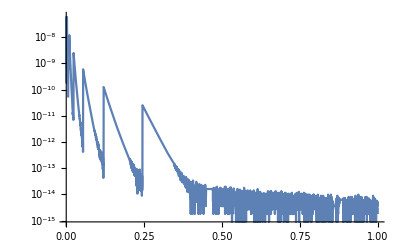

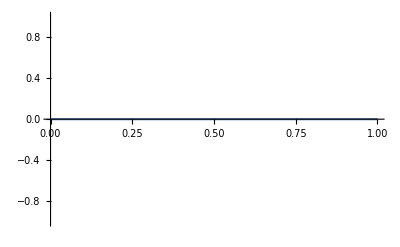

```mathematica
check=LogPlot[EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]-EllPiSol[1][δ]/.UnEvaluatedIntegral1[δ,e]->integration[integrandEllPi21[x],0.4,δ]/.e->0.4//Re,{δ,0,1}]
check=Plot[EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]-EllPiSol[1][δ]/.UnEvaluatedIntegral1[δ,e]->integration[integrandEllPi21[x],0.4,δ]/.e->0.4//Im,{δ,0,1}]
```

### Solution for EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]

```mathematica
Clear[Q]
```

```mathematica
$Assumptions={δ>0,1>e>0};
```

```mathematica
k=Function[{δ},(16 e)/((4+δ) (4 e+δ))];
m=Function[{δ},(4 e)/(4 e+δ)];
```

General solution of the ODE.

```mathematica
solδ2[1]=f/.DSolve[eqEllPi2[1]==0,f,δ][[1,1]]/.C[1]->Q[e]//Simplify;
solδ2[2]=f/.DSolve[eqEllPi2[1]==0,f,δ][[1,1]]/.C[1]->Q[e]//Simplify;
solδ2[1]-solδ2[2]//Simplify (*The solutions are the same*)
```

0

```mathematica
solδ2[1][δ]//FullSimplify
```

(√(δ+(16 e)/(4+4 e+δ)) (Q[e]+(2 EllipticK[(4 e)/(4 e+K[1])] (2+2 e+K[1])-EllipticE[(4 e)/(4 e+K[1])] (4 e+K[1]))/(2 √(4+K[1]) √(4 e+K[1]) √(4+4 e+K[1]))K[1]1δ))/δ

Definition of the constant of integration P[e]

```mathematica
Clear[Q]
(solδ2[1][1]//FullSimplify)/.(2 EllipticK[(4 e)/(4 e+K[1])] (2+2 e+K[1])-EllipticE[(4 e)/(4 e+K[1])] (4 e+K[1]))/(2 √(4+K[1]) √(4 e+K[1]) √(4+4 e+K[1]))K[1]11->0;
Q[e]=Solve[%==EllipticPi[k[1],m[1]],Q[e]][[1,1,2]]
```

(√((5+4 e)/(1+4 e)) EllipticPi[(16 e)/(5 (1+4 e)),(4 e)/(1+4 e)])/(√5)

Final solution and check

```mathematica
solδ2[1][δ]//FullSimplify
```

(√(δ+(16 e)/(4+4 e+δ)) (√(5+20/(1+4 e)) EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]+5 (2 EllipticK[(4 e)/(4 e+K[1])] (2+2 e+K[1])-EllipticE[(4 e)/(4 e+K[1])] (4 e+K[1]))/(2 √(4+K[1]) √(4 e+K[1]) √(4+4 e+K[1]))K[1]1δ))/(5 δ)

```mathematica
integration[f_,ee_,δ_]:=NIntegrate[f/.e->ee,{x,1,δ}]
integrandEllPi22[x_]:=(-((4 e+x) EllipticE[(4 e)/(4 e+x)])+2 (2+2 e+x) EllipticK[(4 e)/(4 e+x)])/(2 √(4+x) √(4 e+x) √(4+4 e+x));
EllPiSol[2][δ_]:=(√(δ+(16 e)/(4+4 e+δ)) (√(5+20/(1+4 e)) EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]+5 UnEvaluatedIntegral2[δ,e]))/(5 δ);
```

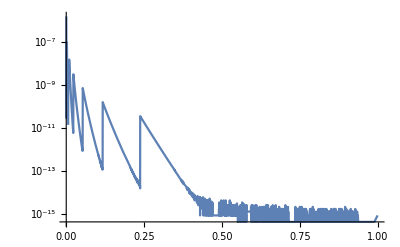

-Graphics-

```mathematica
check=LogPlot[EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]-EllPiSol[2][δ]/.UnEvaluatedIntegral2[δ,e]->integration[integrandEllPi22[x],0.4,δ]/.e->0.4//Re,{δ,0,1}]
check=Plot[EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]-EllPiSol[2][δ]/.UnEvaluatedIntegral2[δ,e]->integration[integrandEllPi22[x],0.4,δ]/.e->0.4//Im,{δ,0,1}]
```

## Deriving the leading order of elliptic functions of interest

The solutions we have derived are characterised by unevaluated integrals over the range [1 , δ]. Numerically, these integrals behaves well even if δ → 0. Thus leading order of the solutions are not difficult to derive

### Leading order of EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]

```mathematica
Series[EllPiSol[1][δ],{δ,0,-1}]/.UnEvaluatedIntegral1[0,e]->Λ[e]
```

(2 √2 √((e (1+e))/(3+14 e+8 e^2)) (EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]+√(3+14 e+8 e^2) Λ[e]))/δ+O[δ]^0

With  Λ[e] == ((1+e) EllipticK[(4 e)/(4 e+x)])/((2+2 e+x)^(3/2) √(4 e+x))x10

### Leading order of EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]

```mathematica
Series[EllPiSol[2][δ],{δ,0,-1}]/.UnEvaluatedIntegral2[0,e]->Τ[e]
```

(2 √(e/(1+e)) (√(5+20/(1+4 e)) EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]+5 Τ[e]))/(5 δ)+O[δ]^0

With Τ[e] == (-((4 e+x) EllipticE[(4 e)/(4 e+x)])+2 (2+2 e+x) EllipticK[(4 e)/(4 e+x)])/(2 √(4+x) √(4 e+x) √(4+4 e+x))x10

## Deriving the subleading order of the elliptic functions of interest

To understand the subleading order (and any other order if we wish)

So far, we have shown a way to write some elliptic functions when their 2 arguments are functions of δ. The algorithm works pretty well, but the final result involves unevaluated integrals. 

In general, we can check that via numerical computation the unevaluated integrals converge when δ->0. Actually, this is true for the integrals themselves, but not for their integrands and their derivatives, which diverge in the limit δ → 0. This implies that can’t proceed to a Taylor development of the unevaluated integrals. 

As an example, take  (2 EllipticK[(4 e)/(4 e+K[1])] (2+2 e+K[1])-EllipticE[(4 e)/(4 e+K[1])] (4 e+K[1]))/(2 √(4+K[1]) √(4 e+K[1]) √(4+4 e+K[1]))K[1]1δ.We can see that (2 EllipticK[(4 e)/(4 e+K[1])] (2+2 e+K[1])-EllipticE[(4 e)/(4 e+K[1])] (4 e+K[1]))/(2 √(4+K[1]) √(4 e+K[1]) √(4+4 e+K[1]))K[1]10is finite for any 1 > e > 0, but (-((4 e+δ) EllipticE[(4 e)/(4 e+δ)])+2 (2+2 e+δ) EllipticK[(4 e)/(4 e+δ)])/(2 √(4+δ) √(4 e+δ) √(4+4 e+δ)) diverges as δ → 0.
 
 The question is: how can we have access to the series expansion of the unevaluated integrals when δ is close to 0 ?
 
 This problem is similar to the problem of deriving the expansion of J[δ]=  Log[x]x1δ. Indeed, this integrals converges as δ → 0, but the Taylor developemnt of J[δ] does not exist since J’[0] = ∞.
 However, we know that J[δ] = 1-δ+δ Log[δ], and the computation that leads to this result is based on an integration by part: Log[x] = d/dx (x Log[x])  - 1.
 
 Then, to obtain the next-to-leading orders of the unevaluated integrals, the strategy is to proceed to integration by parts. Schematically, the kind of computation we do is 
 
   F[x]x =  d/dx( x F[x])x -  x F'[x]x1δ.1δ1δ
  
  With this, a series expansion is feasible.

```mathematica
Simplify[Series[((1+e) EllipticK[(4 e)/(4 e+x)] (4 e+x))/((2+2 e+x) (4 e+x))^(3/2),{x,0,2}],{1>e>0,1>x>0}]
```

Log[(64 e)/x]/(8 √2 √(e (1+e)))+(-((1+7 e) Log[(64 e)/x])/(64 √2 (e (1+e))^(3/2))+(2+Log[(64 e)/x])/(128 √2 e √(e (1+e)))) x+(((3+18 e+75 e^2) Log[(64 e)/x])/(1024 √2 (e (1+e))^(5/2))-((1+7 e) (2+Log[(64 e)/x]))/(1024 √2 e (e (1+e))^(3/2))+(-5-28 Log[2]+7 Log[1/(4 e)]+7 Log[x])/(8192 √2 e^2 √(e (1+e)))) x^2+O[x]^3

```mathematica
Simplify[Series[(-((4 e+x) EllipticE[(4 e)/(4 e+x)])+2 (2+2 e+x) EllipticK[(4 e)/(4 e+x)])/(2 √(4+x) √(4 e+x) √(4+4 e+x)),{x,0,2}],{1>e>0,1>x>0}]
```

(-4 e+8 e Log[2]+Log[4096]-2 e Log[1/(4 e)]+2 Log[e]-2 Log[x]-2 e Log[x])/(16 √(e (1+e)))+((2-4 e+28 e Log[2]-7 e Log[1/(4 e)]+Log[(64 e)/x]-7 e Log[x])/(128 e √(e (1+e)))+((-1-3 e-e^2) (-4 e+8 e Log[2]+Log[4096]-2 e Log[1/(4 e)]+2 Log[e]-2 Log[x]-2 e Log[x]))/(128 (e (1+e))^(3/2))) x+((-5+53 e-28 Log[2]+52 e Log[2]+7 Log[1/(4 e)]-13 e Log[1/(4 e)]+7 Log[x]-13 e Log[x])/(8192 e^2 √(e (1+e)))+((-1-3 e-e^2) (2-4 e+28 e Log[2]-7 e Log[1/(4 e)]+Log[(64 e)/x]-7 e Log[x]))/(1024 e (e (1+e))^(3/2))+((3+10 e+17 e^2+10 e^3+3 e^4) (-4 e+8 e Log[2]+Log[4096]-2 e Log[1/(4 e)]+2 Log[e]-2 Log[x]-2 e Log[x]))/(2048 (e (1+e))^(5/2))) x^2+O[x]^3

### General algorithm for one integration by part only.

Consider that the number n is the number of integration by parts that we do. If n =2, we integrate by part 2 times, if n=3, we integrate by part 3 times, etc...
In this section, n=1, and thanks to the procedure, we will have access to the order δ^1 of the unevaluated integral. If we want the order δ^m, we need n = m.

We consider a function G[x] such that the integral of G[x] from 1 to δ is convergent even if δ -> 0.  However, G[x] and its derivatives diverge in x = 0 but x G[x] converges in 0.

```mathematica
Clear[G]
```

```mathematica
ValueG=Solve[D[x^1 G[x],{x,1}]==TotalDerivative,G[x]][[1]][[1]]
```

G[x]→TotalDerivative-x G'[x]

```mathematica
II[1][δ_]:=1/Factorial[1]((D[x^1 G[x],{x,1-1}]/.x->δ)-(D[x^1 G[x],{x,1-1}]/.x->1))+Integrate[(G[x]/.ValueG)/.TotalDerivative->0,{x,1,δ}]
II[1][δ]
```

-G[1]+δ G[δ]+∫_1^δ -x G'[x]ⅆx

We want to expand this integral up to the order δ^1.

```mathematica
WillGiveDivergence[1]=II[1][δ][[3]]/.x->0 (*This will be generalized to x^n->0 if we consider any other n*)
ISOkay[1]=II[1][δ]/.G'[x]->0
```

Integrate::ilim: Invalid integration variable or limit(s) in {0,1,δ}.

∫_1^δ 0ⅆ0

-G[1]+δ G[δ]

Since n =1 is a simple case, WillGiveDivergence[1] = 0 and we don’t meet any other divergence. For other values of n, WillGiveDivergence[1] ≠0 and we need to iterate another integration by part, until the nth WillGiveDivergence[n] = 0.
We integrate by part WillGiveDivergence

```mathematica
WillGiveDivergence[1]=0;
```

II[1][δ] does not change when n=1.

```mathematica
IntegrandStaying[1][x_]=-x G'[x];
IINonIntegrand[1][δ_]=-G[1]+δ G[δ]//Simplify;
```

### (Example of higher n: algorithm for n=2)

We consider a function F[x] such that the integral of F[x] from 1 to δ is convergent even if δ->0.  However, F[x] and its derivatives diverge in x = 0, x F[x] converges in 0.

```mathematica
Clear[F]
```

```mathematica
ValueF=Solve[D[x^2 F[x],{x,2}]==TotalDerivative,F[x]][[1]][[1]]
```

F[x]→1/2 (TotalDerivative-4 x F'[x]-x^2 F''[x])

```mathematica
II[2][δ_]:=1/Factorial[2]((D[x^2 F[x],{x,2-1}]/.x->δ)-(D[x^2 F[x],{x,2-1}]/.x->1))+Integrate[(F[x]/.ValueF)/.TotalDerivative->0,{x,1,δ}]
```

```mathematica
II[2][δ]
```

∫_1^δ 1/2 (-4 x F'[x]-x^2 F''[x])ⅆx+1/2 (-2 F[1]+2 δ F[δ]-F'[1]+δ^2 F'[δ])

We want to expand this integral up to the order δ^2. This is not yet possible because of the term 4 x F'[x]. Indeed, the expansion of II[δ] would be  II[0] + δ Lim(δ → 0) ( integrand )  + 1/2 δ^2 ( integrand’[δ = 0] ), and integrand’[δ = 0] contains  the term 4 F’[δ] which diverges. 
We can nevertheless go beyond.

```mathematica
WillGiveDivergence[2]=II[2][δ][[1]]/.x^2->0 (*This will be generalized to x^n->0*)
ISOkay[2]=II[2][δ]/.F'[x]->0
```

∫_1^δ -2 x F'[x]ⅆx

∫_1^δ -1/2 x^2 F''[x]ⅆx+1/2 (-2 F[1]+2 δ F[δ]-F'[1]+δ^2 F'[δ])

We integrate by part WillGiveDivergence

The final result is (Check on paper)

```mathematica
II[2][δ_]=-(1/2)δ^2F'[δ]+(1/2)F'[1]+δ F[δ]-F[1]+Integrate[x^2/2 F''[x],{x,1,δ}]//Simplify
```

-F[1]+δ F[δ]+∫_1^δ 1/2 x^2 F''[x]ⅆx+F'[1]/2-1/2 δ^2 F'[δ]

```mathematica
IntegrandStaying[2][x_]=1/2 x^2 F''[x];
IINonIntegrand[2][δ_]=-F[1]+δ F[δ]+F'[1]/2-1/2 δ^2 F'[δ]//Simplify;
```

### Series expansion of ((1+e) EllipticK[(4 e)/(4 e+x)] (4 e+x))/((2+2 e+x) (4 e+x))^(3/2)x1δ up to order δ^1.

```mathematica
$Assumptions={δ>0,1>e>0};
```

```mathematica
Clear[G]
G=Function[x,((1+e) EllipticK[(4 e)/(4 e+x)])/((2+2 e+x)^(3/2) √(4 e+x))];
```

```mathematica
FirstPartExpansion[1][δ_]=Series[IINonIntegrand[1][δ],{δ,0,1}]//Simplify;
SecondPartExpansion[1][δ_]=Λ2[e]+δ Limit[-δ G'[δ],δ->0,Direction->"FromAbove"];
TotalExpansion[1][δ_]=FirstPartExpansion[1][δ]+SecondPartExpansion[1][δ]//Simplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(-((1+e) EllipticK[(4 e)/(1+4 e)])/((3+2 e)^(3/2) √(1+4 e))+Λ2[e])+(1/(8 √2 √(e (1+e)))+(6 Log[2]+Log[e]-Log[δ])/(8 √2 √(e (1+e)))) δ+O[δ]^2

```mathematica
FullSimplify[(1/(8 √2 √(e (1+e)))+(6 Log[2]+Log[e]-Log[δ])/(8 √2 √(e (1+e)))),{1>e>0,δ>0}]
```

(1+Log[(64 e)/δ])/(8 √2 √(e (1+e)))

Where Λ2[e] is defined by 

Λ2[e] = - x G'[x]x10. Namely

Λ2[e] == ((1+e) ((2+2 e+x) EllipticE[(4 e)/(4 e+x)]+3 x EllipticK[(4 e)/(4 e+x)]))/(2 (2+2 e+x)^(5/2) √(4 e+x))x10.

Note that we have -((1+e) EllipticK[(4 e)/(1+4 e)])/((3+2 e)^(3/2) √(1+4 e))+Λ2[e]==Λ[e].

The δ^1 order of ((1+e) EllipticK[(4 e)/(4 e+x)] (4 e+x))/((2+2 e+x) (4 e+x))^(3/2)x1δ is now provided!

### Series expansion of (-((4 e+x) EllipticE[(4 e)/(4 e+x)])+2 (2+2 e+x) EllipticK[(4 e)/(4 e+x)])/(2 √(4+x) √(4 e+x) √(4+4 e+x))x1δ up to order δ^1.

```mathematica
$Assumptions={δ>0,1>e>0};
```

```mathematica
Clear[G]
G=Function[x,(-((4 e+x) EllipticE[(4 e)/(4 e+x)])+2 (2+2 e+x) EllipticK[(4 e)/(4 e+x)])/(2 √(4+x) √(4 e+x) √(4+4 e+x))];
```

```mathematica
FirstPartExpansion2[1][δ_]=Series[IINonIntegrand[1][δ],{δ,0,1}]//Simplify;
SecondPartExpansion2[1][δ_]=Τ2[e]+δ Limit[-δ G'[δ],δ->0,Direction->"FromAbove"];
TotalExpansion2[1][δ_]=FirstPartExpansion2[1][δ]+SecondPartExpansion2[1][δ]//Simplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

((EllipticE[(4 e)/(1+4 e)]+4 e EllipticE[(4 e)/(1+4 e)]-6 EllipticK[(4 e)/(1+4 e)]-4 e EllipticK[(4 e)/(1+4 e)])/(2 √5 √(5+24 e+16 e^2))+Τ2[e])+(1/8 √(1+1/e)+(-2 e+6 Log[2]+e Log[16]-e Log[1/(4 e)]+Log[e]-Log[δ]-e Log[δ])/(8 √(e (1+e)))) δ+O[δ]^2

```mathematica
FullSimplify[1/8 √(1+1/e)+(-2 e+6 Log[2]+e Log[16]-e Log[1/(4 e)]+Log[e]-Log[δ]-e Log[δ])/(8 √(e (1+e))),{1>e>0,δ>0}]
```

(1-e+(1+e) Log[(64 e)/δ])/(8 √(e (1+e)))

Where Τ2[e] is defined by 

Τ2[e] = - x G'[x]x10.Namely :

Τ2[e] == (4 (16 (1+e)^2+4 (4+3 e) x+3 x^2) EllipticE[(4 e)/(4 e+x)]+x (-16+16 e^2+4 e x+x^2) EllipticK[(4 e)/(4 e+x)])/(4 √(4 e+x) ((4+x) (4+4 e+x))^(3/2))x10

Note that we have (EllipticE[(4 e)/(1+4 e)]+4 e EllipticE[(4 e)/(1+4 e)]-6 EllipticK[(4 e)/(1+4 e)]-4 e EllipticK[(4 e)/(1+4 e)])/(2 √5 √(5+24 e+16 e^2))+Τ2[e]==Τ[e].

The δ^1 order of (-((4 e+x) EllipticE[(4 e)/(4 e+x)])+2 (2+2 e+x) EllipticK[(4 e)/(4 e+x)])/(2 √(4+x) √(4 e+x) √(4+4 e+x))x1δ is now provided!

### Expansion of EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)] (up to order O(1))

```mathematica
EllPiSolSeries[1][δ_]=EllPiSol[1][δ]/.UnEvaluatedIntegral1[δ,e]->TotalExpansion[1][δ]//Simplify
```

(2 √2 √((e (1+e))/(3+14 e+8 e^2)) (EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]+(√((3+2 e) (1+4 e)) (-EllipticK[(4 e)/(1+4 e)]-e EllipticK[(4 e)/(1+4 e)]+(3+2 e)^(3/2) √(1+4 e) Λ2[e]))/((3+2 e)^(3/2) √(1+4 e))))/δ+((√((3+2 e) (1+4 e)) √((e (1+e))/(3+14 e+8 e^2)) (1+6 Log[2]+Log[e]-Log[δ]))/(4 √(e (1+e)))+((1+3 e) √((e (1+e))/(3+14 e+8 e^2)) (EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]+(√((3+2 e) (1+4 e)) (-EllipticK[(4 e)/(1+4 e)]-e EllipticK[(4 e)/(1+4 e)]+(3+2 e)^(3/2) √(1+4 e) Λ2[e]))/((3+2 e)^(3/2) √(1+4 e))))/(2 √2 e (1+e)))+O[δ]^1

### Expansion of EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)](up to order O(1))

```mathematica
EllPiSolSeries[2][δ_]=EllPiSol[2][δ]/.UnEvaluatedIntegral2[δ,e]->TotalExpansion2[1][δ]//Simplify
```

(2 √(e/(1+e)) (√(5+20/(1+4 e)) EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]+(√5 EllipticE[(4 e)/(1+4 e)]+4 √5 e EllipticE[(4 e)/(1+4 e)]-6 √5 EllipticK[(4 e)/(1+4 e)]-4 √5 e EllipticK[(4 e)/(1+4 e)]+10 √(5+24 e+16 e^2) Τ2[e])/(2 √(5+24 e+16 e^2))))/(5 δ)+((√(e/(1+e)) (-2 e+√((1+e)/e) √(e (1+e))+6 Log[2]+e Log[16]-e Log[1/(4 e)]+Log[e]-Log[δ]-e Log[δ]))/(4 √(e (1+e)))+(√(e/(1+e)) (1+e+e^2) (√(5+20/(1+4 e)) EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]+(√5 EllipticE[(4 e)/(1+4 e)]+4 √5 e EllipticE[(4 e)/(1+4 e)]-6 √5 EllipticK[(4 e)/(1+4 e)]-4 √5 e EllipticK[(4 e)/(1+4 e)]+10 √(5+24 e+16 e^2) Τ2[e])/(2 √(5+24 e+16 e^2))))/(20 e (1+e)))+O[δ]^1

## Graphic visualisation of the approximated elliptic integrals of interest

Load integrals for numerical evaluations and some value of the eccentricity (chosen to be es)

```mathematica
L[e_]:=NIntegrate[((1+e) (4 e+x) EllipticK[(4 e)/(4 e+x)])/((2+2 e+x) (4 e+x))^(3/2),{x,1,0}];
T[e_]:=NIntegrate[(-((4 e+x) EllipticE[(4 e)/(4 e+x)])+2 (2+2 e+x) EllipticK[(4 e)/(4 e+x)])/(2 √(4+x) √(4 e+x) √(4+4 e+x)),{x,1,0}];
```

```mathematica
L2[e_]:=NIntegrate[((1+e) ((2+2 e+x) EllipticE[(4 e)/(4 e+x)]+3 x EllipticK[(4 e)/(4 e+x)]))/(2 (2+2 e+x)^(5/2) √(4 e+x)),{x,1,0}];
T2[e_]:=NIntegrate[(4 (16 (1+e)^2+4 (4+3 e) x+3 x^2) EllipticE[(4 e)/(4 e+x)]+x (-16+16 e^2+4 e x+x^2) EllipticK[(4 e)/(4 e+x)])/(4 √(4 e+x) ((4+x) (4+4 e+x))^(3/2)),{x,1,0}];
```

```mathematica
es=0.267274722370204471306266679001108662534850177806303129347095243706763759745090466255130201033649`80.;
```

Specific values for e = 0

```mathematica
Integrate[((1+e) (4 e+x) EllipticK[(4 e)/(4 e+x)])/((2+2 e+x) (4 e+x))^(3/2)/.e->0,{x,1,0}]
Integrate[(-((4 e+x) EllipticE[(4 e)/(4 e+x)])+2 (2+2 e+x) EllipticK[(4 e)/(4 e+x)])/(2 √(4+x) √(4 e+x) √(4+4 e+x))/.e->0,{x,1,0}]
```

-π/(2 √3)

-π/2

```mathematica
Integrate[Simplify[((1+e) ((2+2 e+x) EllipticE[(4 e)/(4 e+x)]+3 x EllipticK[(4 e)/(4 e+x)]))/(2 (2+2 e+x)^(5/2) √(4 e+x))/.e->0,{1>x>0}],{x,1,0}]
Integrate[Simplify[(4 (16 (1+e)^2+4 (4+3 e) x+3 x^2) EllipticE[(4 e)/(4 e+x)]+x (-16+16 e^2+4 e x+x^2) EllipticK[(4 e)/(4 e+x)])/(4 √(4 e+x) ((4+x) (4+4 e+x))^(3/2))/.e->0,{1>x>0}],{x,1,0}]
```

-π/(3 √3)

-π/4

Specific values for e = 1

```mathematica
Integrate[Simplify[((1+e) (4 e+x) EllipticK[(4 e)/(4 e+x)])/((2+2 e+x) (4 e+x))^(3/2)/.e->1,{1>x>0}],{x,1,0}]
Integrate[Simplify[(-((4 e+x) EllipticE[(4 e)/(4 e+x)])+2 (2+2 e+x) EllipticK[(4 e)/(4 e+x)])/(2 √(4+x) √(4 e+x) √(4+4 e+x))/.e->1,{1>x>0}],{x,1,0}]
```

-1+EllipticE[4/5]-1/5 EllipticK[4/5]

∫_1^0 (-EllipticE[4/(4+x)]+2 EllipticK[4/(4+x)])/(2 √(8+x))ⅆx

```mathematica
Integrate[Simplify[((1+e) ((2+2 e+x) EllipticE[(4 e)/(4 e+x)]+3 x EllipticK[(4 e)/(4 e+x)]))/(2 (2+2 e+x)^(5/2) √(4 e+x))/.e->1,{1>x>0}],{x,1,0}]
Integrate[Simplify[(4 (16 (1+e)^2+4 (4+3 e) x+3 x^2) EllipticE[(4 e)/(4 e+x)]+x (-16+16 e^2+4 e x+x^2) EllipticK[(4 e)/(4 e+x)])/(4 √(4 e+x) ((4+x) (4+4 e+x))^(3/2))/.e->1,{1>x>0}],{x,1,0}]
```

-1+EllipticE[4/5]-3/25 EllipticK[4/5]

∫_1^0 (4 (16+3 x) EllipticE[4/(4+x)]+x^2 EllipticK[4/(4+x)])/(4 (4+x) (8+x)^(3/2))ⅆx

How EllPiSolSeries[1][δ] is close to EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]

```mathematica
δLimit1=δ/.FindRoot[0.1-Abs[(Normal[EllPiSolSeries[1][δ]]-EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)])/EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]]/.e->es/.{Λ2->L2,Τ2->T2},{δ,1,3}][[1]]
```

1.63835

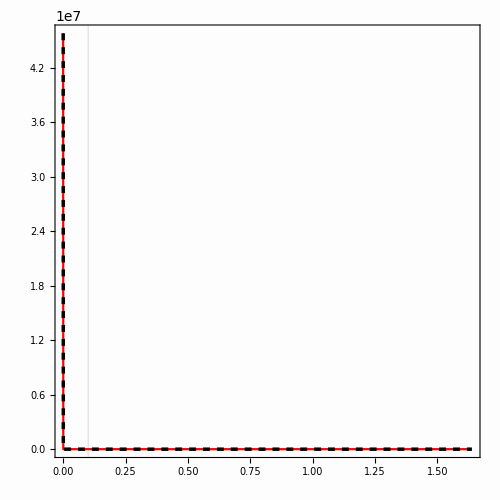

```mathematica
SetDirectory[NotebookDirectory[]];
{EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)],Normal[EllPiSolSeries[1][δ]]}/.e->es/.{Λ2->L2,Τ2->T2}/.δ->DELTA;

Show[
Plot[%,{DELTA,0,δLimit1},PlotStyle->{Red,{Directive[AbsoluteThickness[2.5],Dashed],Black}},PlotRange->All,
PlotLegends->Placed[LineLegend[{MaTeX["\\Pi\\Big( \\frac{2 e (2+2e+\\delta)}{(1+e)(4e + \\delta)} , \\frac{4 e}{4 e +\\delta} \\Big)"],MaTeX["\\text{Asymptotic approximation}"]}],{0.75,0.75}]],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\Pi","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["EllPi1 vs approx RANGE ALL.png",%];
```

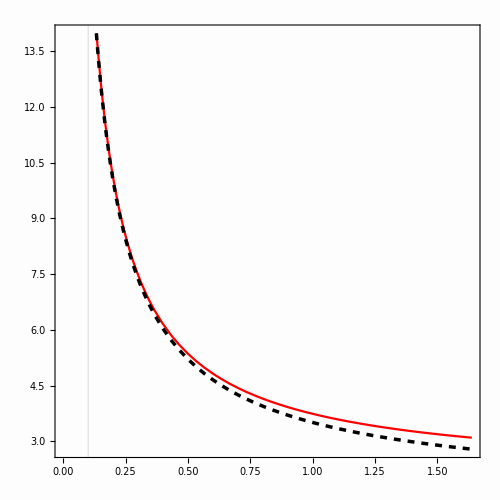

```mathematica
SetDirectory[NotebookDirectory[]];
{EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)],Normal[EllPiSolSeries[1][δ]]}/.e->es/.{Λ2->L2,Τ2->T2}/.δ->DELTA;

Show[
Plot[%,{DELTA,0,δLimit1},PlotStyle->{Red,{Directive[AbsoluteThickness[2.5],Dashed],Black}},
PlotLegends->Placed[LineLegend[{MaTeX["\\Pi\\Big( \\frac{2 e (2+2e+\\delta)}{(1+e)(4e + \\delta)} , \\frac{4 e}{4 e +\\delta} \\Big)"],MaTeX["\\text{Asymptotic approximation}"]}],{0.75,0.75}]],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\Pi","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["EllPi1 vs approx.png",%];
```

How EllPiSolSeries[2][δ] is close to EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]

```mathematica
δLimit2=δ/.FindRoot[0.1-Abs[(Normal[EllPiSolSeries[2][δ]]-EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)])/EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]]/.e->es/.{Τ2->T2},{δ,0.1,5}][[1]]
```

0.887371

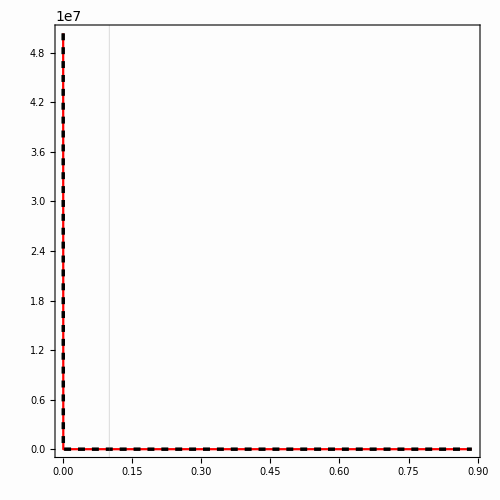

```mathematica
SetDirectory[NotebookDirectory[]];
{EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)],Normal[EllPiSolSeries[2][δ]]}/.e->es/.{Τ2->T2}/.δ->DELTA;

Show[
Plot[%,{DELTA,0,δLimit2},PlotStyle->{Red,{Directive[AbsoluteThickness[2.5],Dashed],Black}},PlotRange->All,
PlotLegends->Placed[LineLegend[{MaTeX["\\Pi\\Big( \\frac{16 e}{(4+ \\delta)(4e + \\delta)} , \\frac{4 e}{4 e +\\delta} \\Big)"],MaTeX["\\text{Asymptotic approximation}"]}],{0.75,0.75}]],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\Pi","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["EllPi2 vs approx RANGE ALL.png",%];
```

```mathematica
δLimit2=δ/.FindRoot[0.1-Abs[(Normal[EllPiSolSeries[2][δ]]-EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)])/EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]]/.e->es/.{Τ2->T2},{δ,0.1,5}][[1]]
```

0.887371

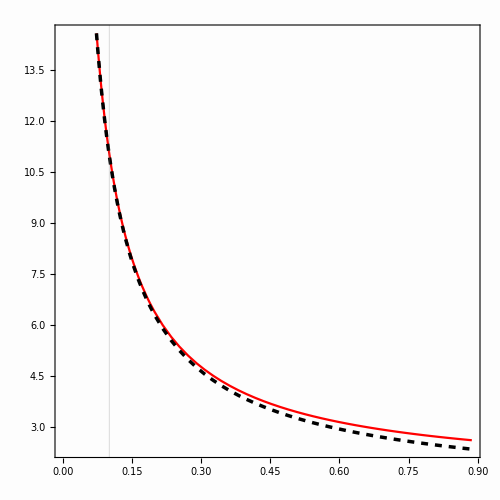

```mathematica
SetDirectory[NotebookDirectory[]];
{EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)],Normal[EllPiSolSeries[2][δ]]}/.e->es/.{Τ2->T2}/.δ->DELTA;

Show[
Plot[%,{DELTA,0,δLimit2},PlotStyle->{Red,{Directive[AbsoluteThickness[2.5],Dashed],Black}},
PlotLegends->Placed[LineLegend[{MaTeX["\\Pi\\Big( \\frac{16 e}{(4+ \\delta)(4e + \\delta)} , \\frac{4 e}{4 e +\\delta} \\Big)"],MaTeX["\\text{Asymptotic approximation}"]}],{0.75,0.75}]],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\Pi","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["EllPi2 vs approx.png",%];
```

## Bilan: Rules of replacement of several elliptic functions

The 0PA equations contain a lot of elliptic integrals of several kind.
It is necessary to replace those elliptic functions by their series expansions. This replacement takes the form

First thing first, we can proceed to the following replacement because, in the 0PA equations (real functions of e and δ), the contributions of  EllipticE[ArcSin[√(δ/(4 e+δ))],(4 e+δ)/δ], EllipticF[ArcSin[√(δ/(4 e+δ))],(4 e+δ)/δ] and EllipticPi[(4 e+δ)/(2+2 e+δ),ArcSin[√(δ/(4 e+δ))],(4 e+δ)/δ] are pure complex numbers.

```mathematica
ReplacementSuchThatRealPartIsPreserved={
EllipticE[ArcSin[√(δ/(4 e+δ))],(4 e+δ)/δ]->0,
EllipticF[ArcSin[√(δ/(4 e+δ))],(4 e+δ)/δ]->0,
EllipticPi[(4 e+δ)/(2+2 e+δ),ArcSin[√(δ/(4 e+δ))],(4 e+δ)/δ]->0
};
```

Then the following replacement allows to finally obtain the expansion of the 0PA equations of the slow and fast variables up to order O(δ^0).

```mathematica
ReplacementEllipticFunctions={
EllipticPi[(4 e+δ)/(2+2 e+δ),(4 e+δ)/δ]->Simplify[Normal[Simplify[Series[Simplify[Normal[Series[EllipticPi[(4 e+Δ)/(2+2 e+Δ),(4 e+δ)/δ],{δ,0,2}]]],{Δ,0,2}]/.Δ->δ]]],
EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]->(2 √2 √((e (1+e))/(3+14 e+8 e^2)) (EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]+√(3+14 e+8 e^2) Λ[e]))/δ+1/(4 e (1+e) (3+2 e)^2 (1+4 e))(√2 (3+11 e) √(e (3+17 e+22 e^2+8 e^3)) EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]+6 e^(5/2) √(6+34 e+44 e^2+16 e^3) EllipticPi[(2 e (3+2 e))/(1+5 e+4 e^2),(4 e)/(1+4 e)]+e (3+2 e)^2 (1+5 e+4 e^2) (1+Log[(64 e)/δ])+√2 (9 √(e (1+e))+75 e √(e (1+e))+196 √(e^5 (1+e))+172 √(e^7 (1+e))+48 √(e^9 (1+e))) Λ[e]),


EllipticPi[(16 e)/(12+8 e-4 e^2-8 (6+2 e+δ)+(6+2 e+δ)^2),(4 e)/(4 e+δ)]->1/(20 e (1+e)^2 (5+24 e+16 e^2) δ)(√(e (5+29 e+40 e^2+16 e^3)) (√5 (5+4 e) (δ+e (8+δ)+e^2 (8+δ)) EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]+5 δ (√(e (5+29 e+40 e^2+16 e^3))-√(e^3 (5+29 e+40 e^2+16 e^3))+√(e^3 (5+29 e+40 e^2+16 e^3)) Log[16]+√(e (5+29 e+40 e^2+16 e^3)) Log[64]-e^(3/2) √(5+29 e+40 e^2+16 e^3) Log[1/(4 e)]+√(e (5+29 e+40 e^2+16 e^3)) Log[e]-√(e (5+29 e+40 e^2+16 e^3)) Log[δ]-√(e^3 (5+29 e+40 e^2+16 e^3)) Log[δ]))+5 √(e/(1+e)) (5+29 e+40 e^2+16 e^3) (δ+e (8+δ)+e^2 (8+δ)) Τ[e]),
EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]->1/(20 e (1+e)^2 (5+24 e+16 e^2) δ)(√(e (5+29 e+40 e^2+16 e^3)) (√5 (5+4 e) (δ+e (8+δ)+e^2 (8+δ)) EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]+5 δ (√(e (5+29 e+40 e^2+16 e^3))-√(e^3 (5+29 e+40 e^2+16 e^3))+√(e^3 (5+29 e+40 e^2+16 e^3)) Log[16]+√(e (5+29 e+40 e^2+16 e^3)) Log[64]-e^(3/2) √(5+29 e+40 e^2+16 e^3) Log[1/(4 e)]+√(e (5+29 e+40 e^2+16 e^3)) Log[e]-√(e (5+29 e+40 e^2+16 e^3)) Log[δ]-√(e^3 (5+29 e+40 e^2+16 e^3)) Log[δ]))+5 √(e/(1+e)) (5+29 e+40 e^2+16 e^3) (δ+e (8+δ)+e^2 (8+δ)) Τ[e]),
EllipticK[(4 e)/(4 e+δ)]->Normal[Series[EllipticK[(4 e)/(4 e+δ)],{δ,0,1}]],
EllipticK[(4 e)/(4 e+δ)]->Normal[Series[EllipticK[1+(4 e)/δ],{δ,0,1}]],
EllipticPi[(2 e)/(1+e),-(4 e)/δ]->Normal[Series[EllipticPi[(2 e)/(1+e),-(4 e)/δ],{δ,0,1}]],
EllipticE[(4 e)/(4 e+δ)]->Normal[Series[EllipticE[(4 e)/(4 e+δ)],{δ,0,1}]],
EllipticE[(4 e)/(4 e+δ)]->Normal[Series[EllipticE[1+(4 e)/δ],{δ,0,1}]]
};
```

We can Write the Elliptic integrals in an ever better way

For EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]:

```mathematica
FullSimplify[1/δ((2 Sqrt[2 e(1+e)])/Sqrt[8 e^2+14e+3])(EllipticPi[(2 e (3+2 e))/(1+5 e+4 e^2),(4 e)/(1+4 e)]+Sqrt[(3+2e)(1+4e)]Λ[e])-1/δ Simplify[SeriesCoefficient[EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]/.ReplacementEllipticFunctions,{δ,0,-1}],{1>e>0}],{1>e>0,δ>0}]/.e->es
```

(0. Λ[0.26727472237020447130626667900110866253485017780630312934709524370676375974509047])/δ

```mathematica
FullSimplify[(1+Log[64 e]-Log[δ])/4+(1+3e)/(2 Sqrt[2] Sqrt[e (1+e)(3+2e)(1+4e) ])(EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]+√(3+14 e+8 e^2) Λ[e])-(Simplify[SeriesCoefficient[EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]/.ReplacementEllipticFunctions,{δ,0,0}],{1>e>0}]),{1>e>0}]/.Log[1/δ]->-Log[δ]
```

0

For EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]

```mathematica
SeriesCoefficient[EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]/.ReplacementEllipticFunctions,{δ,0,-1}]
```

(2 (√5 √(e (5+29 e+40 e^2+16 e^3)) EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]+5 √(e/(1+e)) Τ[e]+25 e √(e/(1+e)) Τ[e]+20 e^2 √(e/(1+e)) Τ[e]))/(5 (1+e) (1+4 e))

```mathematica
FullSimplify[1/δ((2(√5 √(e (1+4 e) (5+4 e)) EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]+5 √e (1+4 e) Τ[e]))/(5 √(1+e) (1+4 e)))-1/δ Simplify[SeriesCoefficient[EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]/.ReplacementEllipticFunctions,{δ,0,-1}],{1>e>0}],{1>e>0,δ>0}]
```

0

```mathematica
(1-e)/(4+4 e)+(Log[64 e]-Log[δ])/4 +((1+e+e^2) Τ[e])/(4 √(e (1+e)^3))+(EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]Sqrt[(1+e) (1+4 e) (5+4 e)](5 e^(1/2) + 9 e^(3/2) + 9 e^(5/2) + 4 e^(7/2)))/(4 √5 e (1+e)^2 (1+4 e) (5+4 e))
```

(1-e)/(4+4 e)+(√((1+e) (1+4 e) (5+4 e)) (5 √e+9 e^(3/2)+9 e^(5/2)+4 e^(7/2)) EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)])/(4 √5 e (1+e)^2 (1+4 e) (5+4 e))+1/4 (Log[64 e]-Log[δ])+((1+e+e^2) Τ[e])/(4 √(e (1+e)^3))

```mathematica
FullSimplify[((1-e)/(4+4 e)+(Log[64 e]-Log[δ])/4 +((1+e+e^2) Τ[e])/(4 √(e (1+e)^3))+(EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]Sqrt[(1+e) (1+4 e) (5+4 e)](5 e^(1/2) + 9 e^(3/2) + 9 e^(5/2) + 4 e^(7/2)))/(4 √5 e (1+e)^2 (1+4 e) (5+4 e)))-(Simplify[SeriesCoefficient[EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]/.ReplacementEllipticFunctions,{δ,0,0}],{1>e>0}]),{1>e>0}]
```

0

## checks

We check that the constructions of the asymptotic formulae of the elliptic functions match with the calculi made in the appendix B of the paper.

```mathematica
O2=Series[δ^2,{δ,0,1}]
```

O[δ]^2

```mathematica
ξ1[x_,e_]=((1+e) (4 e+x) EllipticK[(4 e)/(4 e+x)])/((2+2 e+x) (4 e+x))^(3/2);
ξ2[x_,e_]=(-((4 e+x) EllipticE[(4 e)/(4 e+x)])+2 (2+2 e+x) EllipticK[(4 e)/(4 e+x)])/(2 √(4+x) √(4 e+x) √(4+4 e+x));
```

```mathematica
series1=Simplify[Series[ξ1[x,e],{x,0,2}],{1>x>0,1>e>0}]/.Log[(64 e)/x]->Log[64 e]-Log[x];
series2=Simplify[Series[ξ2[x,e],{x,0,2}],{1>x>0,1>e>0}]/.Log[(64 e)/x]->Log[64 e]-Log[x];
```

```mathematica
seriesder1=Simplify[Series[D[ξ1[x,e],x],{x,0,3}],{1>x>0,1>e>0}]/.Log[(64 e)/x]->Log[64 e]-Log[x]/.Log[x/(4 e)]->Log[x]-Log[4e]/.Log[x/(64 e)]->Log[x]-Log[64 e];
seriesder2=Simplify[Series[D[ξ2[x,e],x],{x,0,3}],{1>x>0,1>e>0}]/.Log[(64 e)/x]->Log[64 e]-Log[x]/.Log[x/(4 e)]->Log[x]-Log[4e]/.Log[x/(64 e)]->Log[x]-Log[64 e];
```

```mathematica
{ζ01,ζ11}=Simplify[CoefficientList[Coefficient[Normal[x series1],x],Log[x]],1>e>0];
{ζ21,ζ31}=Simplify[CoefficientList[Coefficient[Normal[series1],x],Log[x]],1>e>0];

{ζ02,ζ12}=Simplify[CoefficientList[Coefficient[Normal[x series2],x],Log[x]],1>e>0];
{ζ22,ζ32}=Simplify[CoefficientList[Coefficient[Normal[series2],x],Log[x]],1>e>0];
```

```mathematica
ζhm11=Simplify[Coefficient[Normal[x^2 seriesder1],x],1>e>0];
{ζh01,ζh11}=Simplify[CoefficientList[Coefficient[Normal[x seriesder1],x],Log[x]],1>e>0];
{ζh21,ζh31}=Simplify[CoefficientList[Coefficient[Normal[seriesder1],x],Log[x]],1>e>0];

ζhm12=Simplify[Coefficient[Normal[x^2 seriesder2],x],1>e>0];
{ζh02,ζh12}=Simplify[CoefficientList[Coefficient[Normal[x seriesder2],x],Log[x]],1>e>0];
{ζh22,ζh32}=Simplify[CoefficientList[Coefficient[Normal[seriesder2],x],Log[x]],1>e>0];
```

```mathematica
Clear[I1,I2]
```

```mathematica
I2[1][δ_]:=ζ01+ζ11 Log[δ]+SeriesCoefficient[Simplify[Series[-x D[ξ1[x,e],x],{x,0,0}],{1>e>0,x>0}],{x,0,0}];
I2[2][δ_]:=ζ02+ζ12 Log[δ]+SeriesCoefficient[Simplify[Series[-x D[ξ2[x,e],x],{x,0,0}],{1>e>0,x>0}],{x,0,0}];
```

EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)] (involves Λ)

```mathematica
ΠδFull1Orderδ0[δ_,e_]=Series[(√(((2+2 e+δ) (4 e+δ))/((3+2 e) (1+4 e))) (EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]+√((3+2 e) (1+4 e)) Ιntegral1[δ]))/δ /.Ιntegral1[δ]->Normal[I1[1][e]+I2[1][δ] δ+O2],{δ,0,0}];(*This is EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)] up to some order*)
ToCompare[δ_,e_]=EllipticPi[(2 e (2+2 e+δ))/((1+e) (4 e+δ)),(4 e)/(4 e+δ)]/.ReplacementEllipticFunctions;
```

```mathematica
check=Simplify[SeriesCoefficient[ToCompare[δ,e],{δ,0,-1}],{1>e>0,δ>0}]-SeriesCoefficient[ΠδFull1Orderδ0[δ,e],{δ,0,-1}]/.I1[1][e]->Λ[e]
check=Simplify[SeriesCoefficient[ToCompare[δ,e],{δ,0,0}]-SeriesCoefficient[ΠδFull1Orderδ0[δ,e],{δ,0,0}]/.I1[1][e]->Λ[e],{1>e>0,δ>0}]
```

0

0

```mathematica
Table[Normal[ΠδFull1Orderδ0[δ,e]]/.e->EE/.I1[1]->Function[e,NIntegrate[ξ1[x,e],{x,1,0}]]/.δ->0.1,{EE,0.1,.9,0.1}]
Table[ToCompare[δ,e]/.e->EE/.Λ->L/.δ->0.1,{EE,0.1,0.9,0.1}]
```

{6.5331,12.7785,20.6381,30.7076,43.9115,61.8953,88.026,130.849,223.605}

{6.5331,12.7785,20.6381,30.7076,43.9115,61.8953,88.026,130.849,223.605}

EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)] (involves Τ)

```mathematica
ΠδFull2Orderδ0[δ_,e_]=Series[(√(δ+(16 e)/(4+4 e+δ)) (√(5+20/(1+4 e)) EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]+5 Ιntegral2[δ]))/(5 δ)/.Ιntegral2[δ]->Normal[I1[2][e]+I2[2][δ] δ+O2],{δ,0,0}]; (*This is EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]*)
```

```mathematica
ToCompare2[δ_,e_]=EllipticPi[(16 e)/((4+δ) (4 e+δ)),(4 e)/(4 e+δ)]/.ReplacementEllipticFunctions;
```

```mathematica
check=FullSimplify[SeriesCoefficient[ToCompare2[δ,e],{δ,0,-1}]-SeriesCoefficient[ΠδFull2Orderδ0[δ,e],{δ,0,-1}]/.I1[2][e]->Τ[e],{1>e>0,δ>0}]
check=Table[FullSimplify[Simplify[SeriesCoefficient[ToCompare2[δ,e],{δ,0,0}],{1>e>0,δ>0}]-Simplify[SeriesCoefficient[ΠδFull2Orderδ0[δ,e],{δ,0,0}]/.I1[2][e]->Τ[e],{1>e>0,δ>0}],{1>e>0,δ>0}],{e,0.1,0.9,0.1}]/.Τ->T/.δ->0.12//Simplify
```

0

{-4.47692×10^-16,-1.17698×10^-16,-1.36323×10^-15,-2.35397×10^-16,5.61787×10^-16,1.13987×10^-15,0.,-1.2448×10^-15,1.08235×10^-15}

```mathematica
Table[Normal[ΠδFull2Orderδ0[δ,e]]/.e->EE/.I1[2]->Function[e,NIntegrate[ξ2[x,e],{x,1,0}]]/.δ->0.1,{EE,0.1,.9,0.1}]
Table[Normal[ToCompare2[δ,e]]/.e->EE/.Τ->T/.δ->0.1,{EE,0.1,0.9,0.1}]
```

{5.47064,8.91601,11.9561,14.6903,17.1759,19.4534,21.5537,23.501,25.315}

{5.47064,8.91601,11.9561,14.6903,17.1759,19.4534,21.5537,23.501,25.315}

## For information: Elliptic integrals of interest at order O(δ^1)

The subsubLeading order involves the following integrals (which can be computed analytically as a function of Λ[e] and Τ[e]). 

Λ3[e] == 1/(4 (2+2 e+x)^(7/2) (4 e+x)^(3/2))(1+e) ((2+2 e+x) (8 e (1+e)+4 (1+5 e) x+5 x^2) EllipticE[(4 e)/(4 e+x)]+x (-2 (1+e)^2+2 (-1+14 e) x+7 x^2) EllipticK[(4 e)/(4 e+x)])x10, 


Τ3[e] == ((8192 e (1+e)^3+1024 (1+e)^2 (4+e (13+6 e)) x+256 (21+e (72+e (3+e) (25+e))) x^2+64 (4+3 e) (12+e (16+e)) x^3+32 (25+e (25+2 e)) x^4+4 (20+3 e) x^5+x^6) EllipticE[(4 e)/(4 e+x)]+2 x (-512 (1+e)^3+384 (1+e) (-2-4 e+e^3) x+64 (1+e) (-9+e (-6+5 e)) x^2+80 (-2+e) (1+e) x^3+10 (-1+e) x^4+x^5) EllipticK[(4 e)/(4 e+x)])/(16 (4 e+x)^(3/2) ((4+x) (4+4 e+x))^(5/2))x10

```mathematica
L3[e_]:=NIntegrate[1/(4 (2+2 e+x)^(7/2) (4 e+x)^(3/2))(1+e) ((2+2 e+x) (8 e (1+e)+4 (1+5 e) x+5 x^2) EllipticE[(4 e)/(4 e+x)]+x (-2 (1+e)^2+2 (-1+14 e) x+7 x^2) EllipticK[(4 e)/(4 e+x)]),{x,1,0}];
T3[e_]:=NIntegrate[((8192 e (1+e)^3+1024 (1+e)^2 (4+e (13+6 e)) x+256 (21+e (72+e (3+e) (25+e))) x^2+64 (4+3 e) (12+e (16+e)) x^3+32 (25+e (25+2 e)) x^4+4 (20+3 e) x^5+x^6) EllipticE[(4 e)/(4 e+x)]+2 x (-512 (1+e)^3+384 (1+e) (-2-4 e+e^3) x+64 (1+e) (-9+e (-6+5 e)) x^2+80 (-2+e) (1+e) x^3+10 (-1+e) x^4+x^5) EllipticK[(4 e)/(4 e+x)])/(16 (4 e+x)^(3/2) ((4+x) (4+4 e+x))^(5/2)),{x,1,0}];
```

```mathematica
$Assumptions=True;
```

## 5) Asymptotic expansions of the 0PA equations (for δ → 0). Results up to subleading order

Now, we have all the tools we need to proceed to the expansion when δ -> 0.

We will go up to the subleading term in δ.

I have done the computation for the modes from k= -2 to k= +2.

```mathematica
$Assumptions=True;
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Load data

### Integrals

For numerical evaluations, we need to definite integrals which depend on eS only (eccentricity at the separatrix).

```mathematica
L[e_]:=NIntegrate[((1+e) (4 e+x) EllipticK[(4 e)/(4 e+x)])/((2+2 e+x) (4 e+x))^(3/2),{x,1,0}];
T[e_]:=NIntegrate[(-((4 e+x) EllipticE[(4 e)/(4 e+x)])+2 (2+2 e+x) EllipticK[(4 e)/(4 e+x)])/(2 √(4+x) √(4 e+x) √(4+4 e+x)),{x,1,0}];
```

```mathematica
L2[e_]:=NIntegrate[((1+e) ((2+2 e+x) EllipticE[(4 e)/(4 e+x)]+3 x EllipticK[(4 e)/(4 e+x)]))/(2 (2+2 e+x)^(5/2) √(4 e+x)),{x,1,0}];
T2[e_]:=NIntegrate[(4 (16 (1+e)^2+4 (4+3 e) x+3 x^2) EllipticE[(4 e)/(4 e+x)]+x (-16+16 e^2+4 e x+x^2) EllipticK[(4 e)/(4 e+x)])/(4 √(4 e+x) ((4+x) (4+4 e+x))^(3/2)),{x,1,0}];
```

```mathematica
L3[e_]:=NIntegrate[1/(4 (2+2 e+x)^(7/2) (4 e+x)^(3/2))(1+e) ((2+2 e+x) (8 e (1+e)+4 (1+5 e) x+5 x^2) EllipticE[(4 e)/(4 e+x)]+x (-2 (1+e)^2+2 (-1+14 e) x+7 x^2) EllipticK[(4 e)/(4 e+x)]),{x,1,0}];
T3[e_]:=NIntegrate[((8192 e (1+e)^3+1024 (1+e)^2 (4+e (13+6 e)) x+256 (21+e (72+e (3+e) (25+e))) x^2+64 (4+3 e) (12+e (16+e)) x^3+32 (25+e (25+2 e)) x^4+4 (20+3 e) x^5+x^6) EllipticE[(4 e)/(4 e+x)]+2 x (-512 (1+e)^3+384 (1+e) (-2-4 e+e^3) x+64 (1+e) (-9+e (-6+5 e)) x^2+80 (-2+e) (1+e) x^3+10 (-1+e) x^4+x^5) EllipticK[(4 e)/(4 e+x)])/(16 (4 e+x)^(3/2) ((4+x) (4+4 e+x))^(5/2)),{x,1,0}];
```

```mathematica
KNum[e_,kk_]:=NIntegrate[(Sin[ψr] (Cos[kk ψr]-ⅈ Sin[kk ψr]))/(1+e Cos[ψr])^2,{ψr,0,2π}];
KAnalytic[ee_,kk_]:={
int=Integrate[(Sin[ψr] (Cos[kk ψr]-ⅈ Sin[kk ψr]))/(1+e Cos[ψr])^2,ψr],
(Limit[int,ψr->π,Direction->1]-Limit[int,ψr->0,Direction->-1]+Limit[int,ψr->2π,Direction->1]-Limit[int,ψr->π,Direction->-1])/.e->ee}
```

### Self-force modes

We use data provided by Maarten Van de Meent. He gave us values of the self-force at the separatrix as a function of φr that we can express as a function of ψr.  This is done for eS =  0.267274722370204471306266679001108662534850177806303129347095243706763759745090466255130201033649`80..

With that data, I extracted the Fourier modes

```mathematica
es=0.267274722370204471306266679001108662534850177806303129347095243706763759745090466255130201033649`80.;

Fr[0]=Function[{α,β},0.00571048749227473333156535062471448327414691448211669921875`100.];
Fϕ[0]=Function[{α,β},-0.0015674146198596584401985243317767526605166494846343994140625`100.]; 

Fr[-1]=Function[{α,β},-8.123159531866127876058303325379483794677071273326873779296875`100.*^-6+4.9870295868317658296371531838862833918568640001467429101467132568359375`96.93863187828894*^-9 ⅈ];
Fϕ[-1]=Function[{α,β},1.038420246731476314638333534323688667200258350931107997894287109375`100.*^-6+8.24616216880369907270124409104372631418300443328917026519775390625`97.0503935850198*^-10 ⅈ]; 


Fr[1]=Function[{α,β},-8.123159531866127876058303325379483794677071273326873779296875`100.*^-6-4.9870295868317658296371531838862833918568640001467429101467132568359375`96.93863187828894*^-9 ⅈ];
Fϕ[1]=Function[{α,β},1.038420246731476314638333534323688667200258350931107997894287109375`100.*^-6-8.24616216880369907270124409104372631418300443328917026519775390625`97.0503935850198*^-10 ⅈ]; 


Fr[-2]=Function[{α,β},-8.11593857695887924987541983679051327271736226975917816162109375`100.*^-6+9.0521358628992629739327683744375130370229953769012354314327239990234375`97.19792703978014*^-9 ⅈ];
Fϕ[-2]=Function[{α,β},1.037392548281354995366753714292062937829541624523699283599853515625`100.*^-6+1.510573788884982676348019795821951694048124181790626607835292816162109375`97.31371335798947*^-9 ⅈ]; 

Fr[2]=Function[{α,β},-8.11593857695887924987541983679051327271736226975917816162109375`100.*^-6-9.0521358628992629739327683744375130370229953769012354314327239990234375`97.19792703978014*^-9 ⅈ];
Fϕ[2]=Function[{α,β},1.037392548281354995366753714292062937829541624523699283599853515625`100.*^-6-1.510573788884982676348019795821951694048124181790626607835292816162109375`97.31371335798947*^-9 ⅈ];
```

### Coefficients

We load the coefficients Aδ, Ae, B, Jϕ, Nϕ, Jr, Eδ, Ee, Fδ, Fe, Gδ, Ge, but also Pϕ, Qϕ and Rϕ.

Coefficients that appear in the equations at the leading order

```mathematica
Get["Aδ short.m"];
Get["Ae short.m"];
Get["B.m"];
Get["JPHI.m"];
Get["NPHI.m"];
Get["Jr.m"];
```

The other coefficients that arrive at the subleading terms

```mathematica
Get["Eδ short.m"];
Get["Ee short.m"];
Get["Fδ short.m"];
Get["Fe short.m"];
Get["Gδ short.m"];
Get["Ge short.m"];
Get["PPHI.m"];
Get["QPHI.m"];
Get["RPHI.m"];
Get["Mr.m"];
Get["Nr.m"];
```

### Some identity

```mathematica
FullSimplify[8Ge+Gδ-e Gδ,{1>e>0}]
```

1/(√(1+e))2 √2 (-3+e)^2 e (3+e)^(3/2) M^2 (Fϕ1[-2][0,e]+Fϕ1[-1][0,e]+Fϕ1[0][0,e]+Fϕ1[1][0,e]+Fϕ1[2][0,e])

### Define a function “replacement” for numerical evaluations

```mathematica
replacement1={𝒜[eS]->Aδ,
ℬ[eS]->B,
𝒥r[eS]->Jr,
𝒩ϕ[eS]->Nϕ,
𝒥ϕ[eS]->Jϕ,
ℰe[eS]->Ee,
ℱe[eS]->Fe,
𝒢e[eS]->Ge,
ℰδ[eS]->Eδ,
ℱδ[eS]->Fδ,
𝒢δ[eS]->Gδ,
𝒫ϕ[eS]->Pϕ,
𝒬ϕ[eS]->Qϕ,
ℛϕ[eS]->Rϕ,
ℳr[eS]->Mr,
𝒩r[eS]->Nr,
tS->0,e->es}/.{e->es,Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]};
```

```mathematica
replacement2={𝒜[e]->Aδ,
ℬ[e]->B,
𝒥r[e]->Jr,
𝒩ϕ[e]->Nϕ,
𝒥ϕ[e]->Jϕ,
ℰe[e]->Ee,
ℱe[e]->Fe,
𝒢e[e]->Ge,
ℰδ[e]->Eδ,
ℱδ[e]->Fδ,
𝒢δ[e]->Gδ,
𝒫ϕ[e]->Pϕ,
𝒬ϕ[e]->Qϕ,
ℛϕ[e]->Rϕ,
ℳr[e]->Mr,
𝒩r[e]->Nr,
tS->0,e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]};
```

## Properties of Roots of ℬ[e]: asymptotic behaviour, roots and plots

What ℬ looks like

```mathematica
B/.e->eS
```

1/(5 (3+eS)^2 (-1+eS^2))eS (60 eS+80 eS^2+20 eS^3+110 √2 √((eS (1+eS))/(3+14 eS+8 eS^2)) EllipticPi[(2 eS (3+2 eS))/((1+eS) (1+4 eS)),(4 eS)/(1+4 eS)]-√5 √((eS (5+4 eS))/(1+5 eS+4 eS^2)) EllipticPi[(16 eS)/(5+20 eS),(4 eS)/(1+4 eS)]-2 √5 eS √((eS (5+4 eS))/(1+5 eS+4 eS^2)) EllipticPi[(16 eS)/(5+20 eS),(4 eS)/(1+4 eS)]+2 √5 √((eS^7 (5+4 eS))/(1+5 eS+4 eS^2)) EllipticPi[(16 eS)/(5+20 eS),(4 eS)/(1+4 eS)]+√5 √((eS^9 (5+4 eS))/(1+5 eS+4 eS^2)) EllipticPi[(16 eS)/(5+20 eS),(4 eS)/(1+4 eS)]-30 √2 √((eS^5 (1+eS))/(3+14 eS+8 eS^2)) EllipticPi[(2 eS (3+2 eS))/(1+5 eS+4 eS^2),(4 eS)/(1+4 eS)]+180 Log[2]+120 eS Log[2]-160 eS^2 Log[2]-120 eS^3 Log[2]-20 eS^4 Log[2]-45 Log[1/(4 eS)]-30 eS Log[1/(4 eS)]+40 eS^2 Log[1/(4 eS)]+30 eS^3 Log[1/(4 eS)]+5 eS^4 Log[1/(4 eS)]+10 √2 (11 √(eS (1+eS))-3 √(eS^5 (1+eS))) Λ[eS]+5 (-1+eS) √eS (1+eS)^(5/2) Τ[eS])

Behaviour of ℬ[e] as e → 0

```mathematica
Simplify[B/.EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]->(Series[Series[EllipticPi[(16 e)/(5+20 e),(4 EE)/(1+4 EE)],{e,0,1}],{EE,0,0}]/.EE->e)/.EllipticPi[(2 e (3+2 e))/(1+5 e+4 e^2),(4 e)/(1+4 e)]->(Series[Series[EllipticPi[(2 e (3+2 e))/(1+5 e+4 e^2),(4 EE)/(1+4EE)],{e,0,0}],{EE,0,0}]/.EE->e)/.EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]->(Series[Series[EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 EE)/(1+4 EE)],{e,0,0}],{EE,0,0}]/.EE->e)/.Λ[0]->-π/(2 Sqrt[3])/.Τ[0]->-π/2,{1>e>0}]
```

Log[1/(64 e)] e-(4 e^2)/3+O[e]^3

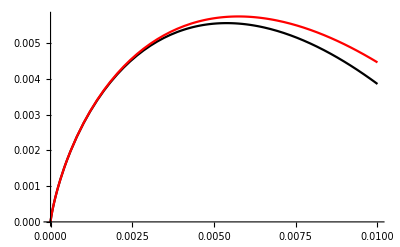

```mathematica
Plot[{B/.{Λ->L,Τ->T},Log[1/(64 e)] e},{e,0,0.01},PlotStyle->{Black,Red}]
```

Behaviour of ℬ[e] as e → 1

```mathematica
FullSimplify[B/.EllipticPi[(16 e)/(5+20 e),(4 e)/(1+4 e)]->(Series[Series[EllipticPi[(16 e)/(5+20 e),(4 EE)/(1+4 EE)],{e,1,0}],{EE,1,0}]/.EE->e)/.EllipticPi[(2 e (3+2 e))/(1+5 e+4 e^2),(4 e)/(1+4 e)]->(Series[Series[EllipticPi[(2 e (3+2 e))/(1+5 e+4 e^2),(4 EE)/(1+4EE)],{e,1,0}],{EE,1,0}]/.EE->e)/.EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 e)/(1+4 e)]->(Series[Series[EllipticPi[(2 e (3+2 e))/((1+e) (1+4 e)),(4 EE)/(1+4 EE)],{e,1,0}],{EE,1,0}]/.EE->e),{-1<e-1<0}]/.Λ->L/.Τ->T
```

(ⅈ π)/(√2 (e-1)^(3/2))+(2.77556×10^-16)/(e-1)+1/(√O[e-1])

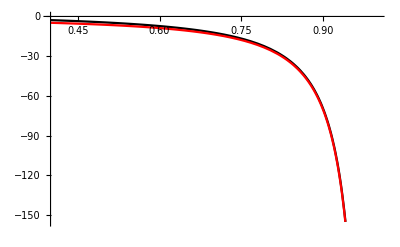

```mathematica
Plot[{B/.{Λ->L,Τ->T},(ⅈ π)/(√2 (e-1)^(3/2))},{e,0.4,1},PlotStyle->{Black,Red}]
```

Find the root of ℬ[e]

```mathematica
emin=0.01;
emax=0.02;
accuracy=10^(-10);
root=(emin + emax)/2;
While[Abs[(B/.e->root/.Λ->L/.Τ->T)]>accuracy,
If[(B/.e->emin/.Λ->L/.Τ->T)(B/.e->root/.Λ->L/.Τ->T)<0,
emax=root;root=(emin+root)/2,
emin=root;root=(emax+root)/2]
]
```

```mathematica
NumberForm[root,20]
```

0.01432602226734161

Graphs

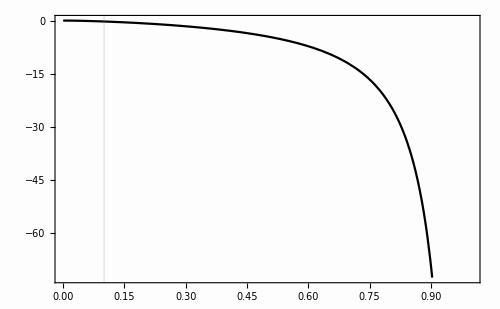

```mathematica
SetDirectory[NotebookDirectory[]];
res=Show[Plot[B/.{Λ->L,Τ->T},{e,0,1},PlotStyle->Black],
ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["e","FontSize"->18],MaTeX["\\mathcal{B}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["B(e) plot.png",%];
```

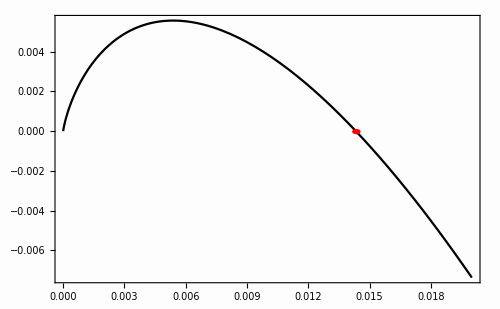

```mathematica
SetDirectory[NotebookDirectory[]];
res=Show[Plot[B/.{Λ->L,Τ->T},{e,0,0.02},PlotStyle->Black],
Graphics[{Red,Disk[{0.014326,0},Scaled[0.0100]]}],
ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["e","FontSize"->18],MaTeX["\\mathcal{B}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["B(e) plot shorter range.png",%];
```

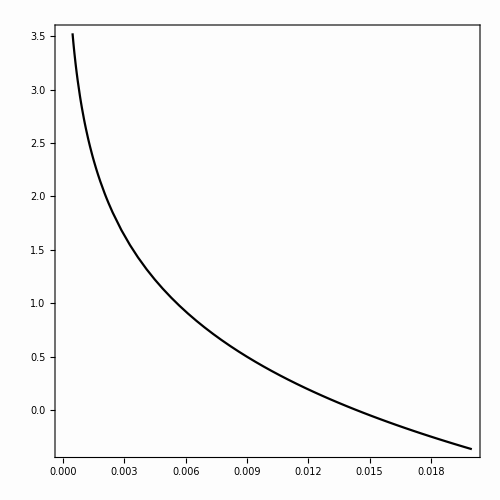

```mathematica
SetDirectory[NotebookDirectory[]];
res=Show[Plot[B/e/.{Λ->L,Τ->T},{e,0,0.02},PlotStyle->Black],
ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["e","FontSize"->18],MaTeX["\\frac{\\mathcal{B}}{e}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["B over e plot.png",%];
```

The equations of motion we have developed here are valid for 0 < δ < Exp[-B/e]. Let us plot this in phase space

```mathematica
BornMax=Interpolation[Table[{ee,Exp[-B/e]/.e->ee/.{Λ->L,Τ->T}},{ee,0.001,0.999,0.001}]];
```

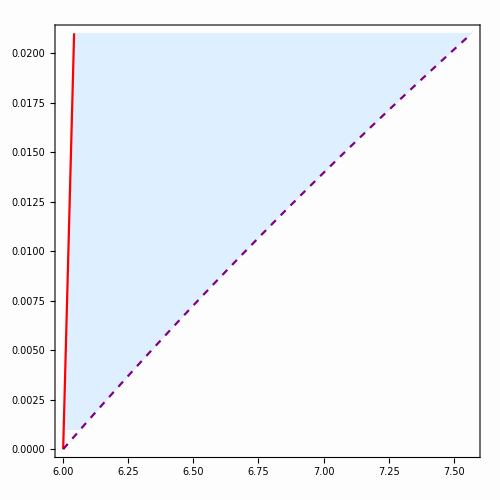

```mathematica
SetDirectory[NotebookDirectory[]];
Show[RegionPlot[6+2ee<=x<=6+2ee+BornMax[ee],{x,6,8},{ee,0.001,0.021},PlotStyle->LightBlue,BoundaryStyle->None],
ParametricPlot[{6+2ee,ee},{ee,0,0.021},AspectRatio->1,AxesLabel->{"p","e"},PlotStyle->Red],
ParametricPlot[{6+2ee+Exp[-B/e]/.e->ee/.{Λ->L,Τ->T},ee},{ee,0,0.021},AspectRatio->1,PlotStyle->{Purple,Dashed}],

ImageSize->500,
PlotRange->All,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["p","FontSize"->18],MaTeX["e","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["Validity domain.png",%];
```

## 0PA Equations when δ → 0; up to the subleading term

```mathematica
O1=Series[δ,{δ,0,0}];
O2=Series[δ^2,{δ,0,0}];
```

The structures of the equations are 

dδ/dt=(𝒜 [e])/(δ(ℬ[e]+ e Log[δ]))+(ℰδ[e] +ℱδ[e] Log[δ]+𝒢δ[e] Log[δ]^2)/(ℬ[e]+ e Log[δ])^2+O[δ]

de/dt=((e-1)/8)𝒜[e]/(δ(ℬ[e]+e Log[δ]))+(ℰe[e] + ℱe[e] Log[δ]+ 𝒢e[e] Log[δ]^2)/(ℬ[e]+ e Log[δ])^2+O[δ]

Ωr=dφr/dt=𝒥r[e]/(ℬ[e]+e Log[δ])+(δ(ℳr[e] +𝒩r[e] Log[δ]))/(ℬ[e]+ e Log[δ])^2+O[δ^2]

Ωϕ=dφϕ/dt= (𝒥ϕ[e]+Log[δ] 𝒩ϕ[e])/(ℬ[e]+ e Log[δ]) +(δ(𝒫ϕ[e]+𝒬ϕ[e] Log[δ]+ ℛϕ[e] Log[δ]^2))/(ℬ[e]+ e Log[δ])^2+O[δ^2].

Here, t is always the slowtime ϵ t.

We first Note that de/dδ(0) == (eS-1)/8

The eccentricity e is a function of δ such that the leading order is e = eS + O[δ]. This means that the complete subleading terms of the equation dδ/dt are given by what we can read above, but with e replace by eS, + the contributions due to the subleading terms of e[δ] (basically, coefficients e’[0] will appear, with e'[0]==(eS-1)/8).
We will develop the full equations of motion of e[δ], φ[δ] up to subleading order , but we will only solve the leading order of dδ/dt.

### Equations at subleading order in δ: equations for δ’[t], e’[t] and φα’[t].

```mathematica
dδdt=𝒜[e]/(δ(ℬ[e]+ e Log[δ]))+(ℰδ[e] +ℱδ[e] Log[δ]+𝒢δ[e] Log[δ]^2)/(ℬ[e]+ e Log[δ])^2+O1;
dedt=(e-1)/8 𝒜[e]/(δ(ℬ[e]+ e Log[δ])) + (ℰe[e] +ℱe[e] Log[δ]+𝒢e[e] Log[δ]^2)/(ℬ[e]+ e Log[δ])^2+O1;

dφrdt=-((e(1+e))^(3/2)π)/(2(3+e)^2)(1/(ℬ[e]+ e Log[δ]))+(δ(ℳr[e] +𝒩r[e] Log[δ]))/(ℬ[e]+ e Log[δ])^2+O2;
dφϕdt=e/(2 Sqrt[2])((1+e)/(3+e))^(3/2)(Log[δ]-Log[64 e])/(ℬ[e]+e Log[δ])+ ((𝒫ϕ[e] + 𝒬ϕ[e] Log[δ] + ℛϕ[e] Log[δ]^2)δ)/(ℬ[e] + e Log[δ])^2+O2;
```

```mathematica
dδdtLeading=𝒜[eS]/(δ(ℬ[eS]+ eS Log[δ]));
```

```mathematica
Gooddδdt=Simplify[dδdt/.e->e[δ]/.e[0]->eS/.e'[0]->(eS-1)/8,{1>eS>0,δ>0}]
Gooddedt=Simplify[dedt/.e->e[δ]/.e[0]->eS/.e'[0]->(eS-1)/8,{1>eS>0,δ>0}]
Gooddφrdt=Simplify[dφrdt/.e->e[δ]/.e[0]->eS/.e'[0]->(eS-1)/8,{1>eS>0,δ>0}]
Gooddφϕdt=Simplify[dφϕdt/.e->e[δ]/.e[0]->eS/.e'[0]->(eS-1)/8,{1>eS>0,δ>0}]
GooddδdtLeading=Simplify[dδdtLeading/.e->e[δ]/.e[0]->eS/.e'[0]->(eS-1)/8,{1>eS>0,δ>0}]
```

𝒜[eS]/((eS Log[δ]+ℬ[eS]) δ)+(Log[δ] 𝒜[eS]-eS Log[δ] 𝒜[eS]+8 ℰδ[eS]+8 Log[δ] ℱδ[eS]+8 Log[δ]^2 𝒢δ[eS]-eS Log[δ] 𝒜'[eS]+eS^2 Log[δ] 𝒜'[eS]-ℬ[eS] 𝒜'[eS]+eS ℬ[eS] 𝒜'[eS]+𝒜[eS] ℬ'[eS]-eS 𝒜[eS] ℬ'[eS])/(8 (eS Log[δ]+ℬ[eS])^2)+O[δ]^1

((-1+eS) 𝒜[eS])/(8 (eS Log[δ]+ℬ[eS]) δ)+1/(64 (eS Log[δ]+ℬ[eS])^2)(-Log[δ] 𝒜[eS]+eS Log[δ] 𝒜[eS]-𝒜[eS] ℬ[eS]+eS 𝒜[eS] ℬ[eS]+64 ℰe[eS]+64 Log[δ] ℱe[eS]+64 Log[δ]^2 𝒢e[eS]+eS Log[δ] 𝒜'[eS]-2 eS^2 Log[δ] 𝒜'[eS]+eS^3 Log[δ] 𝒜'[eS]+ℬ[eS] 𝒜'[eS]-2 eS ℬ[eS] 𝒜'[eS]+eS^2 ℬ[eS] 𝒜'[eS]-𝒜[eS] ℬ'[eS]+2 eS 𝒜[eS] ℬ'[eS]-eS^2 𝒜[eS] ℬ'[eS])+O[δ]^1

-((eS (1+eS))^(3/2) π)/(2 ((3+eS)^2 (eS Log[δ]+ℬ[eS])))+1/(32 (3+eS)^3 (eS Log[δ]+ℬ[eS])^2)(3 eS √(eS (1+eS)) π Log[δ]+6 √(eS^5 (1+eS)) π Log[δ]-9 √(eS^7 (1+eS)) π Log[δ]+9 √(eS (1+eS)) π ℬ[eS]+8 eS √(eS (1+eS)) π ℬ[eS]-15 √(eS^5 (1+eS)) π ℬ[eS]-2 √(eS^7 (1+eS)) π ℬ[eS]+864 ℳr[eS]+864 eS ℳr[eS]+288 eS^2 ℳr[eS]+32 eS^3 ℳr[eS]+864 Log[δ] 𝒩r[eS]+864 eS Log[δ] 𝒩r[eS]+288 eS^2 Log[δ] 𝒩r[eS]+32 eS^3 Log[δ] 𝒩r[eS]-6 eS √(eS (1+eS)) π ℬ'[eS]-2 √(eS^5 (1+eS)) π ℬ'[eS]+6 √(eS^7 (1+eS)) π ℬ'[eS]+2 √(eS^9 (1+eS)) π ℬ'[eS]) δ+O[δ]^2

-(eS ((1+eS)/(3+eS))^(3/2) (6 Log[2]+Log[eS]-Log[δ]))/(2 (√2 (eS Log[δ]+ℬ[eS])))+1/(32 (3+eS)^(5/2) (eS Log[δ]+ℬ[eS])^2)(3 √2 eS √(1+eS) Log[δ]+√2 eS^2 √(1+eS) Log[δ]-3 √2 eS^3 √(1+eS) Log[δ]-√2 eS^4 √(1+eS) Log[δ]+18 √2 eS^2 √(1+eS) Log[2] Log[δ]-18 √2 eS^3 √(1+eS) Log[2] Log[δ]+3 √2 eS^2 √(1+eS) Log[eS] Log[δ]-3 √2 eS^3 √(1+eS) Log[eS] Log[δ]-3 √2 eS^2 √(1+eS) Log[δ]^2+3 √2 eS^3 √(1+eS) Log[δ]^2+3 √2 √(1+eS) ℬ[eS]+√2 eS √(1+eS) ℬ[eS]-3 √2 eS^2 √(1+eS) ℬ[eS]-√2 eS^3 √(1+eS) ℬ[eS]+18 √2 √(1+eS) Log[2] ℬ[eS]+24 √2 eS √(1+eS) Log[2] ℬ[eS]-36 √2 eS^2 √(1+eS) Log[2] ℬ[eS]-6 √2 eS^3 √(1+eS) Log[2] ℬ[eS]+3 √2 √(1+eS) Log[eS] ℬ[eS]+4 √2 eS √(1+eS) Log[eS] ℬ[eS]-6 √2 eS^2 √(1+eS) Log[eS] ℬ[eS]-√2 eS^3 √(1+eS) Log[eS] ℬ[eS]-3 √2 √(1+eS) Log[δ] ℬ[eS]-4 √2 eS √(1+eS) Log[δ] ℬ[eS]+6 √2 eS^2 √(1+eS) Log[δ] ℬ[eS]+√2 eS^3 √(1+eS) Log[δ] ℬ[eS]+32 (3+eS)^(5/2) 𝒫ϕ[eS]+32 (3+eS)^(5/2) Log[δ] 𝒬ϕ[eS]+32 (3+eS)^(5/2) Log[δ]^2 ℛϕ[eS]-18 √2 eS √(1+eS) Log[2] ℬ'[eS]-6 √2 eS^2 √(1+eS) Log[2] ℬ'[eS]+18 √2 eS^3 √(1+eS) Log[2] ℬ'[eS]+6 √2 eS^4 √(1+eS) Log[2] ℬ'[eS]-3 √2 eS √(1+eS) Log[eS] ℬ'[eS]-√2 eS^2 √(1+eS) Log[eS] ℬ'[eS]+3 √2 eS^3 √(1+eS) Log[eS] ℬ'[eS]+√2 eS^4 √(1+eS) Log[eS] ℬ'[eS]+3 √2 eS √(1+eS) Log[δ] ℬ'[eS]+√2 eS^2 √(1+eS) Log[δ] ℬ'[eS]-3 √2 eS^3 √(1+eS) Log[δ] ℬ'[eS]-√2 eS^4 √(1+eS) Log[δ] ℬ'[eS]) δ+O[δ]^2

𝒜[eS]/(eS δ Log[δ]+δ ℬ[eS])

### Comparison with the complete 0PA equations via graphs.

For convenience, we the functions we are dX/dt (where X represents δ, e, φr and φϕ) are 

dδdt=𝒜[e]/(δ(ℬ[e]+ e Log[δ]))+(ℰδ[e] +ℱδ[e] Log[δ]+𝒢δ[e] Log[δ]^2)/(ℬ[e]+ e Log[δ])^2+O1;
dedt=(e-1)/8 𝒜[e]/(δ(ℬ[e]+ e Log[δ])) + (ℰe[e] +ℱe[e] Log[δ]+𝒢e[e] Log[δ]^2)/(ℬ[e]+ e Log[δ])^2+O1;

dφrdt=-((e(1+e))^(3/2)π)/(2(3+e)^2)(1/(ℬ[e]+ e Log[δ]))+(δ(ℳr[e] +𝒩r[e] Log[δ]))/(ℬ[e]+ e Log[δ])^2+O2;
dφϕdt=e/(2 Sqrt[2])((1+e)/(3+e))^(3/2)(Log[δ]-Log[64 e])/(ℬ[e]+e Log[δ])+ ((𝒫ϕ[e] + 𝒬ϕ[e] Log[δ] + ℛϕ[e] Log[δ]^2)δ)/(ℬ[e] + e Log[δ])^2+O2;

with e replaced by eS. This is because we can’t plot properly  Gooddδdt, Gooddedt, Gooddφrdt, Gooddφϕt, GooddδdtLeading because we don’t know the values of 𝒜’[eS] or ℬ’[eS].

Slow variables

```mathematica
Get["0PA Slow variables Simplified.m"];
```

```mathematica
δmax=0.4;
100 Abs[(dδdt0PA-Normal[dδdt])/dδdt0PA]/.replacement2/.e->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.δ->δmax//Re
100 Abs[(dedt0PA-Normal[dedt])/dδdt0PA]/.replacement2/.e->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.δ->δmax//Re
```

3.67247

0.348856

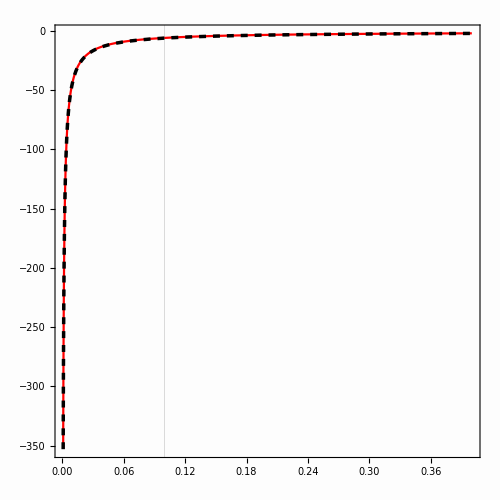

```mathematica
SetDirectory[NotebookDirectory[]];
{dδdt0PA/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.δ->DELTA//Re,Normal[dδdt]/.replacement2/.e->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.δ->DELTA};

Show[
Plot[%,{DELTA,0.001,δmax},PlotStyle->{Red,{Directive[AbsoluteThickness[2.5],Dashed],Black}},PlotRange->All,
PlotLegends->Placed[LineLegend[{MaTeX["\\text{0PA equation}"],MaTeX["\\text{Asymptotic approximation}"]}],{0.7,0.2}]],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\frac{d\\delta}{d\\tilde{t}}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["ddeltadt plot 0PA vs approx RANGE ALL.png",%];
```

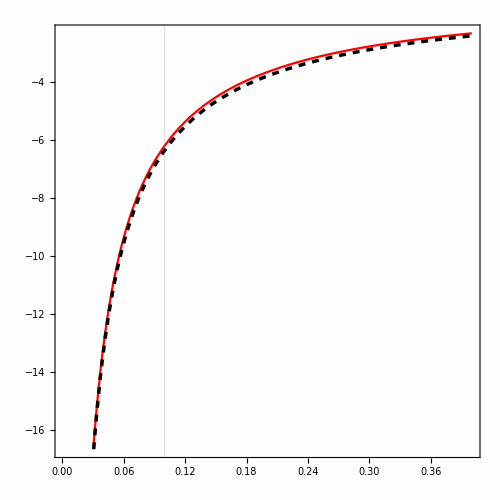

```mathematica
SetDirectory[NotebookDirectory[]];
{dδdt0PA/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.δ->DELTA//Re,Normal[dδdt]/.replacement2/.e->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.δ->DELTA};

Show[
Plot[%,{DELTA,0.001,δmax},PlotStyle->{Red,{Directive[AbsoluteThickness[2.5],Dashed],Black}},
PlotLegends->Placed[LineLegend[{MaTeX["\\text{0PA equation}"],MaTeX["\\text{Asymptotic approximation}"]}],{0.7,0.2}]],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\frac{d\\delta}{d\\tilde{t}}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["ddeltadt plot 0PA vs approx.png",%];
```

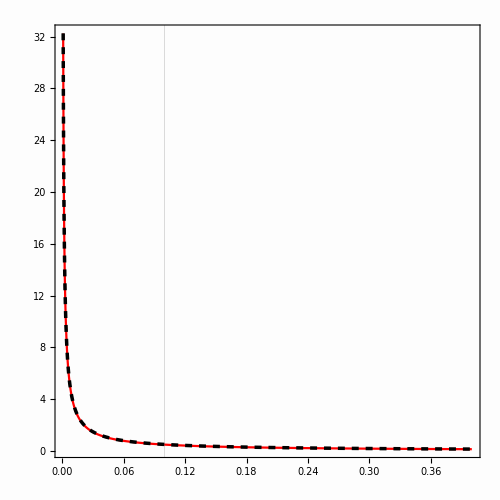

```mathematica
SetDirectory[NotebookDirectory[]];
{dedt0PA/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.δ->DELTA//Re,Normal[dedt]/.replacement2/.e->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.δ->DELTA};

Show[
Plot[%,{DELTA,0.001,δmax},PlotStyle->{Red,{Directive[AbsoluteThickness[2.5],Dashed],Black}},PlotRange->All,
PlotLegends->Placed[LineLegend[{MaTeX["\\text{0PA equation}"],MaTeX["\\text{Asymptotic approximation}"]}],{0.7,0.2}]],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\frac{d e_{(0)}}{d\\tilde{t}}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["dedt plot 0PA vs approx RANGE ALL.png",%];
```

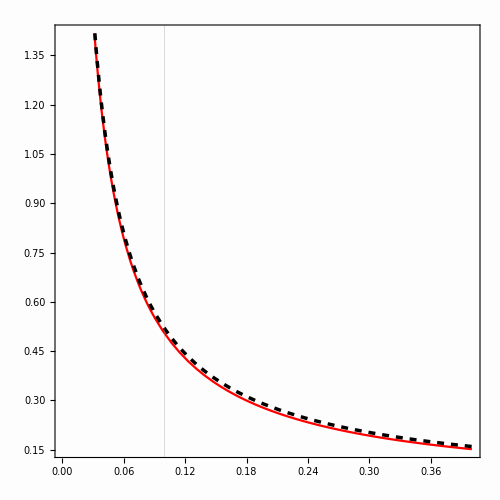

```mathematica
SetDirectory[NotebookDirectory[]];
{dedt0PA/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.δ->DELTA//Re,Normal[dedt]/.replacement2/.e->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.δ->DELTA};

Show[
Plot[%,{DELTA,0.001,δmax},PlotStyle->{Red,{Directive[AbsoluteThickness[2.5],Dashed],Black}},
PlotLegends->Placed[LineLegend[{MaTeX["\\text{0PA equation}"],MaTeX["\\text{Asymptotic approximation}"]}],{0.75,0.75}]],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\frac{d e_{(0)}}{d\\tilde{t}}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["dedt plot 0PA vs approx.png",%];
```

Fast variables

```mathematica
OMEGAR=KerrGeoFrequencies[0,6+2e+δ,e,1][[1]];
OMEGAϕ=KerrGeoFrequencies[0,6+2e+δ,e,1][[3]];
```

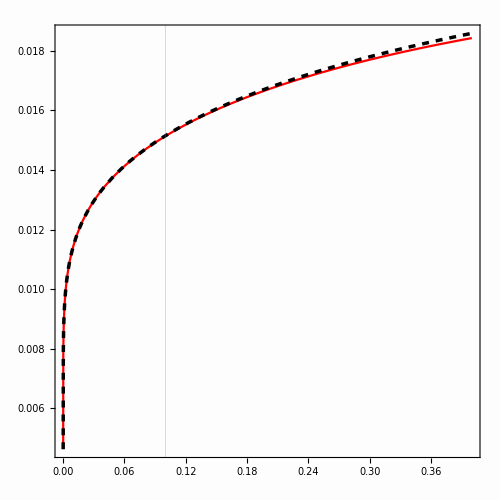

```mathematica
SetDirectory[NotebookDirectory[]];
{OMEGAR/.{e->es}/.δ->DELTA,Normal[dφrdt]/.replacement2/.e->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.δ->DELTA};

Show[
Plot[%,{DELTA,0,δmax},PlotStyle->{Red,{Directive[AbsoluteThickness[2.5],Dashed],Black}},PlotRange->All,
PlotLegends->Placed[LineLegend[{MaTeX["\\text{0PA equation}"],MaTeX["\\text{Asymptotic approximation}"]}],{0.7,0.2}]],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\frac{d \\varphi_{r(0)}}{d \\tilde{t}}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["dPHIRdt plot vs OMEGAR.png",%];
```

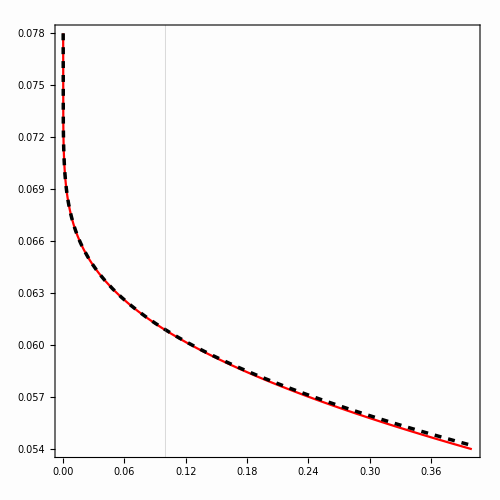

```mathematica
SetDirectory[NotebookDirectory[]];
{OMEGAϕ/.{e->es}/.δ->DELTA,Normal[dφϕdt]/.replacement2/.e->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.δ->DELTA};

Show[
Plot[%,{DELTA,0,δmax},PlotStyle->{Red,{Directive[AbsoluteThickness[2.5],Dashed],Black}},PlotRange->All,
PlotLegends->Placed[LineLegend[{MaTeX["\\text{0PA equation}"],MaTeX["\\text{Asymptotic approximation}"]}],{0.75,0.75}]],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\frac{d \\varphi_{\\phi(0)}}{d \\tilde{t}}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["dPHIPHIdt plot vs OMEGAPHI.png",%];
```

### Equations for e’[δ], φα’[δ], ψr’[δ], δ’[ψr] and t’[δ]

```mathematica
dedδ=Simplify[Series[Simplify[(dedt/.e->e[δ])/(dδdt/.e->e[δ])/.e[0]->eS/.e'[0]->(eS-1)/8,1>eS>0],{δ,0,1}],1>eS>0]
```

1/8 (-1+eS)+((-eS Log[δ] 𝒜[eS]+eS^2 Log[δ] 𝒜[eS]-𝒜[eS] ℬ[eS]+eS 𝒜[eS] ℬ[eS]+64 ℰe[eS]+8 ℰδ[eS]-8 eS ℰδ[eS]+64 Log[δ] ℱe[eS]+8 Log[δ] ℱδ[eS]-8 eS Log[δ] ℱδ[eS]+64 Log[δ]^2 𝒢e[eS]+8 Log[δ]^2 𝒢δ[eS]-8 eS Log[δ]^2 𝒢δ[eS]) δ)/(64 𝒜[eS] (eS Log[δ]+ℬ[eS]))+O[δ]^2

```mathematica
dφrdδ=Simplify[Series[Simplify[(dφrdt/.e->e[δ])/(dδdt/.e->e[δ])/.e[0]->eS/.e'[0]->(eS-1)/8,1>eS>0],{δ,0,2}],1>eS>0]
```

-(((eS (1+eS))^(3/2) π) δ)/(2 ((3+eS)^2 𝒜[eS]))+1/(32 (3+eS)^3 𝒜[eS]^2 (eS Log[δ]+ℬ[eS]))(9 eS √(eS (1+eS)) π Log[δ] 𝒜[eS]+8 √(eS^5 (1+eS)) π Log[δ] 𝒜[eS]-15 √(eS^7 (1+eS)) π Log[δ] 𝒜[eS]-2 √(eS^9 (1+eS)) π Log[δ] 𝒜[eS]+9 √(eS (1+eS)) π 𝒜[eS] ℬ[eS]+8 eS √(eS (1+eS)) π 𝒜[eS] ℬ[eS]-15 √(eS^5 (1+eS)) π 𝒜[eS] ℬ[eS]-2 √(eS^7 (1+eS)) π 𝒜[eS] ℬ[eS]+48 eS √(eS (1+eS)) π ℰδ[eS]+64 √(eS^5 (1+eS)) π ℰδ[eS]+16 √(eS^7 (1+eS)) π ℰδ[eS]+48 eS √(eS (1+eS)) π Log[δ] ℱδ[eS]+64 √(eS^5 (1+eS)) π Log[δ] ℱδ[eS]+16 √(eS^7 (1+eS)) π Log[δ] ℱδ[eS]+48 eS √(eS (1+eS)) π Log[δ]^2 𝒢δ[eS]+64 √(eS^5 (1+eS)) π Log[δ]^2 𝒢δ[eS]+16 √(eS^7 (1+eS)) π Log[δ]^2 𝒢δ[eS]+864 𝒜[eS] ℳr[eS]+864 eS 𝒜[eS] ℳr[eS]+288 eS^2 𝒜[eS] ℳr[eS]+32 eS^3 𝒜[eS] ℳr[eS]+864 Log[δ] 𝒜[eS] 𝒩r[eS]+864 eS Log[δ] 𝒜[eS] 𝒩r[eS]+288 eS^2 Log[δ] 𝒜[eS] 𝒩r[eS]+32 eS^3 Log[δ] 𝒜[eS] 𝒩r[eS]-6 √(eS^5 (1+eS)) π Log[δ] 𝒜'[eS]-2 √(eS^7 (1+eS)) π Log[δ] 𝒜'[eS]+6 √(eS^9 (1+eS)) π Log[δ] 𝒜'[eS]+2 √(eS^11 (1+eS)) π Log[δ] 𝒜'[eS]-6 eS √(eS (1+eS)) π ℬ[eS] 𝒜'[eS]-2 √(eS^5 (1+eS)) π ℬ[eS] 𝒜'[eS]+6 √(eS^7 (1+eS)) π ℬ[eS] 𝒜'[eS]+2 √(eS^9 (1+eS)) π ℬ[eS] 𝒜'[eS]) δ^2+O[δ]^3

```mathematica
dφϕdδ=Series[Simplify[(dφϕdt/.e->e[δ])/(dδdt/.e->e[δ])/.e[0]->eS/.e'[0]->(eS-1)/8,1>eS>0],{δ,0,2}]
```

-((eS ((1+eS)/(3+eS))^(3/2) (Log[64]+Log[eS]-Log[δ])) δ)/(2 (√2 𝒜[eS]))+1/(32 (3+eS)^(5/2) 𝒜[eS]^2 (eS Log[δ]+ℬ[eS]))(3 √2 eS √(1+eS) Log[δ] 𝒜[eS]+√2 eS^2 √(1+eS) Log[δ] 𝒜[eS]-3 √2 eS^3 √(1+eS) Log[δ] 𝒜[eS]-√2 eS^4 √(1+eS) Log[δ] 𝒜[eS]+18 √2 eS √(1+eS) Log[2] Log[δ] 𝒜[eS]+24 √2 eS^2 √(1+eS) Log[2] Log[δ] 𝒜[eS]-42 √2 eS^3 √(1+eS) Log[2] Log[δ] 𝒜[eS]+√2 eS^3 √(1+eS) Log[64] Log[δ] 𝒜[eS]-√2 eS^4 √(1+eS) Log[64] Log[δ] 𝒜[eS]+3 √2 eS √(1+eS) Log[eS] Log[δ] 𝒜[eS]+4 √2 eS^2 √(1+eS) Log[eS] Log[δ] 𝒜[eS]-6 √2 eS^3 √(1+eS) Log[eS] Log[δ] 𝒜[eS]-√2 eS^4 √(1+eS) Log[eS] Log[δ] 𝒜[eS]-3 √2 eS √(1+eS) Log[δ]^2 𝒜[eS]-4 √2 eS^2 √(1+eS) Log[δ]^2 𝒜[eS]+6 √2 eS^3 √(1+eS) Log[δ]^2 𝒜[eS]+√2 eS^4 √(1+eS) Log[δ]^2 𝒜[eS]+3 √2 √(1+eS) 𝒜[eS] ℬ[eS]+√2 eS √(1+eS) 𝒜[eS] ℬ[eS]-3 √2 eS^2 √(1+eS) 𝒜[eS] ℬ[eS]-√2 eS^3 √(1+eS) 𝒜[eS] ℬ[eS]+18 √2 √(1+eS) Log[2] 𝒜[eS] ℬ[eS]+24 √2 eS √(1+eS) Log[2] 𝒜[eS] ℬ[eS]-42 √2 eS^2 √(1+eS) Log[2] 𝒜[eS] ℬ[eS]+√2 eS^2 √(1+eS) Log[64] 𝒜[eS] ℬ[eS]-√2 eS^3 √(1+eS) Log[64] 𝒜[eS] ℬ[eS]+3 √2 √(1+eS) Log[eS] 𝒜[eS] ℬ[eS]+4 √2 eS √(1+eS) Log[eS] 𝒜[eS] ℬ[eS]-6 √2 eS^2 √(1+eS) Log[eS] 𝒜[eS] ℬ[eS]-√2 eS^3 √(1+eS) Log[eS] 𝒜[eS] ℬ[eS]-3 √2 √(1+eS) Log[δ] 𝒜[eS] ℬ[eS]-4 √2 eS √(1+eS) Log[δ] 𝒜[eS] ℬ[eS]+6 √2 eS^2 √(1+eS) Log[δ] 𝒜[eS] ℬ[eS]+√2 eS^3 √(1+eS) Log[δ] 𝒜[eS] ℬ[eS]+24 √2 eS √(1+eS) Log[64] ℰδ[eS]+32 √2 eS^2 √(1+eS) Log[64] ℰδ[eS]+8 √2 eS^3 √(1+eS) Log[64] ℰδ[eS]+24 √2 eS √(1+eS) Log[eS] ℰδ[eS]+32 √2 eS^2 √(1+eS) Log[eS] ℰδ[eS]+8 √2 eS^3 √(1+eS) Log[eS] ℰδ[eS]-24 √2 eS √(1+eS) Log[δ] ℰδ[eS]-32 √2 eS^2 √(1+eS) Log[δ] ℰδ[eS]-8 √2 eS^3 √(1+eS) Log[δ] ℰδ[eS]+24 √2 eS √(1+eS) Log[64] Log[δ] ℱδ[eS]+32 √2 eS^2 √(1+eS) Log[64] Log[δ] ℱδ[eS]+8 √2 eS^3 √(1+eS) Log[64] Log[δ] ℱδ[eS]+24 √2 eS √(1+eS) Log[eS] Log[δ] ℱδ[eS]+32 √2 eS^2 √(1+eS) Log[eS] Log[δ] ℱδ[eS]+8 √2 eS^3 √(1+eS) Log[eS] Log[δ] ℱδ[eS]-24 √2 eS √(1+eS) Log[δ]^2 ℱδ[eS]-32 √2 eS^2 √(1+eS) Log[δ]^2 ℱδ[eS]-8 √2 eS^3 √(1+eS) Log[δ]^2 ℱδ[eS]+24 √2 eS √(1+eS) Log[64] Log[δ]^2 𝒢δ[eS]+32 √2 eS^2 √(1+eS) Log[64] Log[δ]^2 𝒢δ[eS]+8 √2 eS^3 √(1+eS) Log[64] Log[δ]^2 𝒢δ[eS]+24 √2 eS √(1+eS) Log[eS] Log[δ]^2 𝒢δ[eS]+32 √2 eS^2 √(1+eS) Log[eS] Log[δ]^2 𝒢δ[eS]+8 √2 eS^3 √(1+eS) Log[eS] Log[δ]^2 𝒢δ[eS]-24 √2 eS √(1+eS) Log[δ]^3 𝒢δ[eS]-32 √2 eS^2 √(1+eS) Log[δ]^3 𝒢δ[eS]-8 √2 eS^3 √(1+eS) Log[δ]^3 𝒢δ[eS]+32 (3+eS)^(5/2) 𝒜[eS] 𝒫ϕ[eS]+32 (3+eS)^(5/2) Log[δ] 𝒜[eS] 𝒬ϕ[eS]+32 (3+eS)^(5/2) Log[δ]^2 𝒜[eS] ℛϕ[eS]-3 √2 eS^2 √(1+eS) Log[64] Log[δ] 𝒜'[eS]-√2 eS^3 √(1+eS) Log[64] Log[δ] 𝒜'[eS]+3 √2 eS^4 √(1+eS) Log[64] Log[δ] 𝒜'[eS]+√2 eS^5 √(1+eS) Log[64] Log[δ] 𝒜'[eS]-3 √2 eS^2 √(1+eS) Log[eS] Log[δ] 𝒜'[eS]-√2 eS^3 √(1+eS) Log[eS] Log[δ] 𝒜'[eS]+3 √2 eS^4 √(1+eS) Log[eS] Log[δ] 𝒜'[eS]+√2 eS^5 √(1+eS) Log[eS] Log[δ] 𝒜'[eS]+3 √2 eS^2 √(1+eS) Log[δ]^2 𝒜'[eS]+√2 eS^3 √(1+eS) Log[δ]^2 𝒜'[eS]-3 √2 eS^4 √(1+eS) Log[δ]^2 𝒜'[eS]-√2 eS^5 √(1+eS) Log[δ]^2 𝒜'[eS]-3 √2 eS √(1+eS) Log[64] ℬ[eS] 𝒜'[eS]-√2 eS^2 √(1+eS) Log[64] ℬ[eS] 𝒜'[eS]+3 √2 eS^3 √(1+eS) Log[64] ℬ[eS] 𝒜'[eS]+√2 eS^4 √(1+eS) Log[64] ℬ[eS] 𝒜'[eS]-3 √2 eS √(1+eS) Log[eS] ℬ[eS] 𝒜'[eS]-√2 eS^2 √(1+eS) Log[eS] ℬ[eS] 𝒜'[eS]+3 √2 eS^3 √(1+eS) Log[eS] ℬ[eS] 𝒜'[eS]+√2 eS^4 √(1+eS) Log[eS] ℬ[eS] 𝒜'[eS]+3 √2 eS √(1+eS) Log[δ] ℬ[eS] 𝒜'[eS]+√2 eS^2 √(1+eS) Log[δ] ℬ[eS] 𝒜'[eS]-3 √2 eS^3 √(1+eS) Log[δ] ℬ[eS] 𝒜'[eS]-√2 eS^4 √(1+eS) Log[δ] ℬ[eS] 𝒜'[eS]) δ^2+O[δ]^3

```mathematica
dψrdδ=-(((1+eS Cos[ψr])^2 (-2-eS+eS Cos[ψr]) √((eS Sin[ψr/2]^2)/(1+eS)) (eS Log[δ]+ℬ[eS])) δ)/(4 ((3+eS)^2 M ϵ 𝒜[eS]))+O[δ]^2;
dδdψr=Simplify[1/dψrdδ,{1>eS>0,δ[ψr]>0}];
```

```mathematica
dtdδ=1/dδdtLeading;
```

```mathematica
$Assumptions=True;
```

```mathematica
FullSimplify[Normal[dδdψr],{1>eS>0,δ>0,π>ψr>0}]//FullSimplify
FullSimplify[Normal[dδdψr],{1>eS>0,δ>0,2π>ψr>π}]//FullSimplify
```

-(4 √(1+1/eS) (3+eS)^2 M ϵ Csc[ψr/2] 𝒜[eS])/(δ (1+eS Cos[ψr])^2 (-2-eS+eS Cos[ψr]) (eS Log[δ]+ℬ[eS]))

-(4 √(1+1/eS) (3+eS)^2 M ϵ Csc[ψr/2] 𝒜[eS])/(δ (1+eS Cos[ψr])^2 (-2-eS+eS Cos[ψr]) (eS Log[δ]+ℬ[eS]))

### Equations involving the proper time (redshift, δ’[τ], etc)

```mathematica
dδdτ=-(√(9-eS^2) (-2-eS+eS Cos[ψrS]) 𝒜[eS])/(2 (√2 (3+eS) (eS Log[δ]+ℬ[eS])) δ)-1/(16 (√2 (3+eS) (eS Log[δ]+ℬ[eS])^2))√(9-eS^2) (-2 Log[δ] 𝒜[eS]+eS^2 Log[δ] 𝒜[eS]-eS^2 Cos[ψrS] Log[δ] 𝒜[eS]-𝒜[eS] ℬ[eS]-Cos[ψrS] 𝒜[eS] ℬ[eS]-16 ℰδ[eS]-8 eS ℰδ[eS]+8 eS Cos[ψrS] ℰδ[eS]-16 Log[δ] ℱδ[eS]-8 eS Log[δ] ℱδ[eS]+8 eS Cos[ψrS] Log[δ] ℱδ[eS]-16 Log[δ]^2 𝒢δ[eS]-8 eS Log[δ]^2 𝒢δ[eS]+8 eS Cos[ψrS] Log[δ]^2 𝒢δ[eS]+2 eS Log[δ] 𝒜'[eS]-eS^2 Log[δ] 𝒜'[eS]-eS^3 Log[δ] 𝒜'[eS]-eS^2 Cos[ψrS] Log[δ] 𝒜'[eS]+eS^3 Cos[ψrS] Log[δ] 𝒜'[eS]+2 ℬ[eS] 𝒜'[eS]-eS ℬ[eS] 𝒜'[eS]-eS^2 ℬ[eS] 𝒜'[eS]-eS Cos[ψrS] ℬ[eS] 𝒜'[eS]+eS^2 Cos[ψrS] ℬ[eS] 𝒜'[eS]-2 𝒜[eS] ℬ'[eS]+eS 𝒜[eS] ℬ'[eS]+eS^2 𝒜[eS] ℬ'[eS]+eS Cos[ψrS] 𝒜[eS] ℬ'[eS]-eS^2 Cos[ψrS] 𝒜[eS] ℬ'[eS])+O[δ]^1;
dtdτ=EnS/(1-2 M/rS)-((3+eS)Cos[ψrS/2]^2)/(Sqrt[2 (9-eS^2)](2+eS-eS Cos[ψrS])^2)δ+O[δ]^2;
```

## 6) First things we can learn thanks to the asymptotic 0PA differential equations

We define Δϕ to be the change of ϕ after the realisation of a complete orbit. Thus Δϕ := ϕ[ψr=2π] - ϕ[ψr=0]. This depends on the fundamental BL frequencies via Δϕ = 2π Ωϕ/Ωr.
Then we define Nw : = Δϕ/(2π)to be the instantaneous number of whirls that are realised around the primary black hole after a complete orbit.

Thanks to the asymptotic differential equations, we can compute the analytical behaviour of Δϕ and Nr close to the separatrix.

The results that we obtain in this chapter can be compared with the paper of Kennefick:   https://arxiv.org/abs/gr-qc/0203086.

## initialization

We want to compare with the results of Glampedakis. This guy uses eccentricity values of 0.3 and 0.9, thus we define for this chapter new replacement functions that are adapted with Glampedakis.

```mathematica
eGlampedakis1=0.3;
eGlampedakis2=0.9;
```

```mathematica
replacementForNw1={𝒜[eS]->Aδ,
ℬ[eS]->B,
𝒥r[eS]->Jr,
𝒩ϕ[eS]->Nϕ,
𝒥ϕ[eS]->Jϕ,
ℰe[eS]->Ee,
ℱe[eS]->Fe,
𝒢e[eS]->Ge,
ℰδ[eS]->Eδ,
ℱδ[eS]->Fδ,
𝒢δ[eS]->Gδ,
𝒫ϕ[eS]->Pϕ,
𝒬ϕ[eS]->Qϕ,
ℛϕ[eS]->Rϕ,
ℳr[eS]->Mr,
𝒩r[eS]->Nr,
tS->0,e->eGlampedakis1}/.{e->eGlampedakis1};

replacementForNw2={𝒜[eS]->Aδ,
ℬ[eS]->B,
𝒥r[eS]->Jr,
𝒩ϕ[eS]->Nϕ,
𝒥ϕ[eS]->Jϕ,
ℰe[eS]->Ee,
ℱe[eS]->Fe,
𝒢e[eS]->Ge,
ℰδ[eS]->Eδ,
ℱδ[eS]->Fδ,
𝒢δ[eS]->Gδ,
𝒫ϕ[eS]->Pϕ,
𝒬ϕ[eS]->Qϕ,
ℛϕ[eS]->Rϕ,
ℳr[eS]->Mr,
𝒩r[eS]->Nr,
tS->0,e->eGlampedakis2}/.{e->eGlampedakis2};
```

## Instantaneous Δϕ and Nw

```mathematica
Δϕ[δ_]=Simplify[Series[2π(dφϕdt/dφrdt)/.e->e[δ],{δ,0,1}]/.{e[0]->eS,e'[0]->(eS-1)/8},{1>eS>0,δ>0}];
```

```mathematica
Nw[Δ_]=Δϕ[Δ]/(2π);
```

```mathematica
Nw[δ]
```

(√((3+eS)/eS) Log[(64 eS)/δ])/(√2 π)+1/(32 eS^(5/2) (1+eS)^2 √(3+eS) π^2 (eS Log[δ]+ℬ[eS]))(-6 √2 eS^2 π Log[δ]-8 √2 eS^3 π Log[δ]+4 √2 eS^4 π Log[δ]+8 √2 eS^5 π Log[δ]+2 √2 eS^6 π Log[δ]+18 √2 eS^2 π Log[2] Log[δ]+18 √2 eS^3 π Log[2] Log[δ]-18 √2 eS^4 π Log[2] Log[δ]-18 √2 eS^5 π Log[2] Log[δ]+3 √2 eS^2 π Log[eS] Log[δ]+3 √2 eS^3 π Log[eS] Log[δ]-3 √2 eS^4 π Log[eS] Log[δ]-3 √2 eS^5 π Log[eS] Log[δ]-3 √2 eS^2 π Log[δ]^2-3 √2 eS^3 π Log[δ]^2+3 √2 eS^4 π Log[δ]^2+3 √2 eS^5 π Log[δ]^2-6 √2 eS π ℬ[eS]-8 √2 eS^2 π ℬ[eS]+4 √2 eS^3 π ℬ[eS]+8 √2 eS^4 π ℬ[eS]+2 √2 eS^5 π ℬ[eS]+18 √2 eS π Log[2] ℬ[eS]+18 √2 eS^2 π Log[2] ℬ[eS]-18 √2 eS^3 π Log[2] ℬ[eS]-18 √2 eS^4 π Log[2] ℬ[eS]+3 √2 eS π Log[eS] ℬ[eS]+3 √2 eS^2 π Log[eS] ℬ[eS]-3 √2 eS^3 π Log[eS] ℬ[eS]-3 √2 eS^4 π Log[eS] ℬ[eS]-3 √2 eS π Log[δ] ℬ[eS]-3 √2 eS^2 π Log[δ] ℬ[eS]+3 √2 eS^3 π Log[δ] ℬ[eS]+3 √2 eS^4 π Log[δ] ℬ[eS]+5184 √2 √(eS (1+eS)) Log[2] ℳr[eS]+5184 √2 eS √(eS (1+eS)) Log[2] ℳr[eS]+1728 √2 eS^2 √(eS (1+eS)) Log[2] ℳr[eS]+32 √2 √(eS^7 (1+eS)) Log[64] ℳr[eS]+864 √2 √(eS (1+eS)) Log[eS] ℳr[eS]+864 √2 eS √(eS (1+eS)) Log[eS] ℳr[eS]+288 √2 √(eS^5 (1+eS)) Log[eS] ℳr[eS]+32 √2 √(eS^7 (1+eS)) Log[eS] ℳr[eS]-864 √2 √(eS (1+eS)) Log[δ] ℳr[eS]-864 √2 eS √(eS (1+eS)) Log[δ] ℳr[eS]-288 √2 √(eS^5 (1+eS)) Log[δ] ℳr[eS]-32 √2 √(eS^7 (1+eS)) Log[δ] ℳr[eS]+5184 √2 √(eS (1+eS)) Log[2] Log[δ] 𝒩r[eS]+5184 √2 eS √(eS (1+eS)) Log[2] Log[δ] 𝒩r[eS]+1728 √2 eS^2 √(eS (1+eS)) Log[2] Log[δ] 𝒩r[eS]+192 √2 eS^3 √(eS (1+eS)) Log[2] Log[δ] 𝒩r[eS]+864 √2 √(eS (1+eS)) Log[eS] Log[δ] 𝒩r[eS]+864 √2 eS √(eS (1+eS)) Log[eS] Log[δ] 𝒩r[eS]+288 √2 √(eS^5 (1+eS)) Log[eS] Log[δ] 𝒩r[eS]+32 √2 √(eS^7 (1+eS)) Log[eS] Log[δ] 𝒩r[eS]-864 √2 √(eS (1+eS)) Log[δ]^2 𝒩r[eS]-864 √2 eS √(eS (1+eS)) Log[δ]^2 𝒩r[eS]-288 √2 √(eS^5 (1+eS)) Log[δ]^2 𝒩r[eS]-32 √2 √(eS^7 (1+eS)) Log[δ]^2 𝒩r[eS]-576 eS √(3+4 eS+eS^2) π 𝒫ϕ[eS]-384 eS^2 √(3+4 eS+eS^2) π 𝒫ϕ[eS]-64 eS^3 √(3+4 eS+eS^2) π 𝒫ϕ[eS]-576 eS √(3+4 eS+eS^2) π Log[δ] 𝒬ϕ[eS]-384 eS^2 √(3+4 eS+eS^2) π Log[δ] 𝒬ϕ[eS]-64 eS^3 √(3+4 eS+eS^2) π Log[δ] 𝒬ϕ[eS]-576 eS √(3+4 eS+eS^2) π Log[δ]^2 ℛϕ[eS]-384 eS^2 √(3+4 eS+eS^2) π Log[δ]^2 ℛϕ[eS]-64 eS^3 √(3+4 eS+eS^2) π Log[δ]^2 ℛϕ[eS]) δ+O[δ]^2

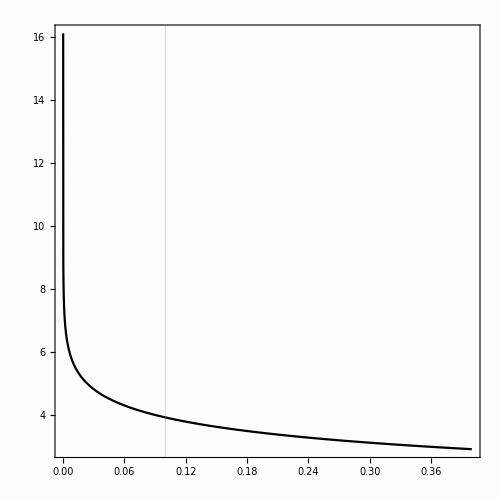

```mathematica
SetDirectory[NotebookDirectory[]];

Normal[Nw[δ]]/.replacementForNw1/.eS->eGlampedakis1/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.δ->Δ;
Show[
Plot[%,{Δ,0,δmax},PlotStyle->Black,PlotRange->All],

PlotRange->All,
ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["N_w","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}
]
Export["Plot of Nw of delta format square 03.png",%];
```

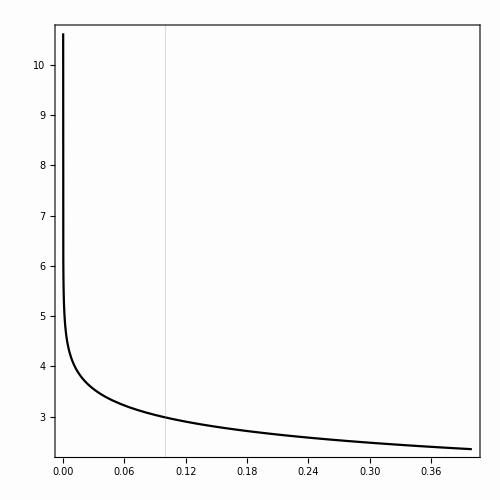

```mathematica
SetDirectory[NotebookDirectory[]];

Normal[Nw[δ]]/.replacementForNw2/.eS->eGlampedakis2/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.δ->Δ;
Show[
Plot[%,{Δ,0,δmax},PlotStyle->Black,PlotRange->All],

PlotRange->All,
ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["N_w","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}
]
Export["Plot of Nw of delta format square 09.png",%];
```

```mathematica
Normal[Nw[δ]]/.replacementForNw1/.eS->eGlampedakis1/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.δ->0.01
Normal[Nw[δ]]/.replacementForNw2/.eS->eGlampedakis2/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.δ->0.01
```

5.64455

4.05752

The number Nw = 5,859 is really close to what has been derived by Kennefick few years ago  https://arxiv.org/abs/gr-qc/0203086. See page 9, bottom graph at the page, curve for a = 0.  In this paper, the curve for δ = 0.01 M, a=0 and es =0.3 shows a number of cycle of about 7.

## 7) Solutions of the adiabatic equations and consequences

We can solve analytically the equations of the late inspiral. 
Basically, what we do is to express variables as a function of δ, and then we derive δ as a function of t. 
Th solution δ[t] is invertible: we can express t as a function of δ.
Recall that t, here, is always the slow time.

```mathematica
ϵValue=10^(-4);
```

## Solution e[δ]

Implementation of the solution

```mathematica
eSol=Function[{δ},eS+1/64 (-8 δ+8 eS δ-δ^2/2+(eS δ^2)/2-(4 δ^2 Log[δ] (-8 𝒢e[eS]-𝒢δ[eS]+eS 𝒢δ[eS]))/(eS 𝒜[eS])+(2 δ^2 (16 eS ℱe[eS]+2 eS ℱδ[eS]-2 eS^2 ℱδ[eS]-8 eS 𝒢e[eS]-16 ℬ[eS] 𝒢e[eS]-eS 𝒢δ[eS]+eS^2 𝒢δ[eS]-2 ℬ[eS] 𝒢δ[eS]+2 eS ℬ[eS] 𝒢δ[eS]))/(eS^2 𝒜[eS])-1/(eS^3 𝒜[eS])8 ⅇ^(-(2 ℬ[eS])/eS) ExpIntegralEi[2 Log[δ]+(2 ℬ[eS])/eS] (-8 eS^2 ℰe[eS]-eS^2 ℰδ[eS]+eS^3 ℰδ[eS]+8 eS ℬ[eS] ℱe[eS]+eS ℬ[eS] ℱδ[eS]-eS^2 ℬ[eS] ℱδ[eS]-8 ℬ[eS]^2 𝒢e[eS]-ℬ[eS]^2 𝒢δ[eS]+eS ℬ[eS]^2 𝒢δ[eS]))];
```

```mathematica
eSolSeries=Function[δ,eS+1/8 (-1+eS) δ+1/(128 𝒜[eS] (eS Log[δ]+ℬ[eS])^3)(-eS^3 Log[δ]^3 𝒜[eS]+eS^4 Log[δ]^3 𝒜[eS]-3 eS^2 Log[δ]^2 𝒜[eS] ℬ[eS]+3 eS^3 Log[δ]^2 𝒜[eS] ℬ[eS]-3 eS Log[δ] 𝒜[eS] ℬ[eS]^2+3 eS^2 Log[δ] 𝒜[eS] ℬ[eS]^2-𝒜[eS] ℬ[eS]^3+eS 𝒜[eS] ℬ[eS]^3+32 eS^2 ℰe[eS]+32 eS^2 Log[δ] ℰe[eS]+64 eS^2 Log[δ]^2 ℰe[eS]+32 eS ℬ[eS] ℰe[eS]+128 eS Log[δ] ℬ[eS] ℰe[eS]+64 ℬ[eS]^2 ℰe[eS]+4 eS^2 ℰδ[eS]-4 eS^3 ℰδ[eS]+4 eS^2 Log[δ] ℰδ[eS]-4 eS^3 Log[δ] ℰδ[eS]+8 eS^2 Log[δ]^2 ℰδ[eS]-8 eS^3 Log[δ]^2 ℰδ[eS]+4 eS ℬ[eS] ℰδ[eS]-4 eS^2 ℬ[eS] ℰδ[eS]+16 eS Log[δ] ℬ[eS] ℰδ[eS]-16 eS^2 Log[δ] ℬ[eS] ℰδ[eS]+8 ℬ[eS]^2 ℰδ[eS]-8 eS ℬ[eS]^2 ℰδ[eS]+64 eS^2 Log[δ]^3 ℱe[eS]-32 eS ℬ[eS] ℱe[eS]-32 eS Log[δ] ℬ[eS] ℱe[eS]+128 eS Log[δ]^2 ℬ[eS] ℱe[eS]-32 ℬ[eS]^2 ℱe[eS]+64 Log[δ] ℬ[eS]^2 ℱe[eS]+8 eS^2 Log[δ]^3 ℱδ[eS]-8 eS^3 Log[δ]^3 ℱδ[eS]-4 eS ℬ[eS] ℱδ[eS]+4 eS^2 ℬ[eS] ℱδ[eS]-4 eS Log[δ] ℬ[eS] ℱδ[eS]+4 eS^2 Log[δ] ℬ[eS] ℱδ[eS]+16 eS Log[δ]^2 ℬ[eS] ℱδ[eS]-16 eS^2 Log[δ]^2 ℬ[eS] ℱδ[eS]-4 ℬ[eS]^2 ℱδ[eS]+4 eS ℬ[eS]^2 ℱδ[eS]+8 Log[δ] ℬ[eS]^2 ℱδ[eS]-8 eS Log[δ] ℬ[eS]^2 ℱδ[eS]-32 eS^2 Log[δ]^3 𝒢e[eS]+64 eS^2 Log[δ]^4 𝒢e[eS]-96 eS Log[δ]^2 ℬ[eS] 𝒢e[eS]+128 eS Log[δ]^3 ℬ[eS] 𝒢e[eS]+32 ℬ[eS]^2 𝒢e[eS]-64 Log[δ] ℬ[eS]^2 𝒢e[eS]+64 Log[δ]^2 ℬ[eS]^2 𝒢e[eS]-4 eS^2 Log[δ]^3 𝒢δ[eS]+4 eS^3 Log[δ]^3 𝒢δ[eS]+8 eS^2 Log[δ]^4 𝒢δ[eS]-8 eS^3 Log[δ]^4 𝒢δ[eS]-12 eS Log[δ]^2 ℬ[eS] 𝒢δ[eS]+12 eS^2 Log[δ]^2 ℬ[eS] 𝒢δ[eS]+16 eS Log[δ]^3 ℬ[eS] 𝒢δ[eS]-16 eS^2 Log[δ]^3 ℬ[eS] 𝒢δ[eS]+4 ℬ[eS]^2 𝒢δ[eS]-4 eS ℬ[eS]^2 𝒢δ[eS]-8 Log[δ] ℬ[eS]^2 𝒢δ[eS]+8 eS Log[δ] ℬ[eS]^2 𝒢δ[eS]+8 Log[δ]^2 ℬ[eS]^2 𝒢δ[eS]-8 eS Log[δ]^2 ℬ[eS]^2 𝒢δ[eS]) δ^2+O[δ]^3];
```

Check that eSol is solution of the asymptotic equations

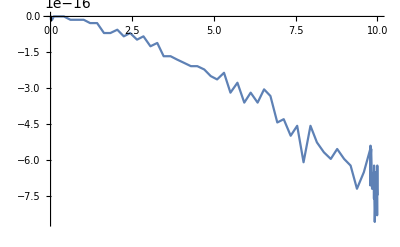

```mathematica
Normal[dedδ]-eSol'[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.δ->DELTA//Re;
checkPlot=Plot[%,{DELTA,0,10}]
```

Save Plots.

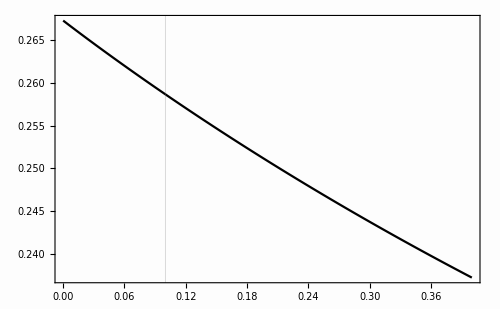

```mathematica
SetDirectory[NotebookDirectory[]];

eSol[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.δ->DELTA//Re;

Show[

Plot[%,{DELTA,0,δmax},PlotStyle->Black],

ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["e_{(0)}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["eSol plot.png",%];
```

```mathematica
eSol[δ]//FullSimplify
```

eS+1/128 (-1+eS) δ (16+δ)-1/(32 eS^3 𝒜[eS])(eS δ^2 (-16 eS ℱe[eS]+2 (-1+eS) eS ℱδ[eS]+(-eS+2 eS Log[δ]-2 ℬ[eS]) (-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS]))+4 ⅇ^(-(2 ℬ[eS])/eS) ExpIntegralEi[2 (Log[δ]+ℬ[eS]/eS)] (-8 eS^2 ℰe[eS]+(-1+eS) eS^2 ℰδ[eS]+ℬ[eS] (8 eS ℱe[eS]-(-1+eS) eS ℱδ[eS]+ℬ[eS] (-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS]))))

```mathematica
Collect[Normal[Simplify[Series[Normal[eSolSeries[δ]/.Log[δ]->LOG],{LOG,-∞,2}]]],{δ,LOG}]
```

eS+(-1/8+eS/8) δ+δ^2 (-1/128+eS/128+(LOG (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))/(16 eS 𝒜[eS])-(-16 eS ℱe[eS]+2 (-1+eS) eS ℱδ[eS]-(eS+2 ℬ[eS]) (-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS]))/(32 eS^2 𝒜[eS])-(-8 eS^2 ℰe[eS]+(-1+eS) eS^2 ℰδ[eS]+ℬ[eS] (8 eS ℱe[eS]-(-1+eS) eS ℱδ[eS]-ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS])))/(16 eS^3 LOG 𝒜[eS])-((eS-2 ℬ[eS]) (-8 eS^2 ℰe[eS]+(-1+eS) eS^2 ℰδ[eS]+ℬ[eS] (8 eS ℱe[eS]-(-1+eS) eS ℱδ[eS]-ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))))/(32 eS^4 LOG^2 𝒜[eS]))

## Solution φϕ[δ]

Implementation of the solution

```mathematica
φϕSol=Function[{δ},φϕS+1/(864 eS^3 (3+eS)^(5/2) 𝒜[eS]^2)ⅇ^(-(3 ℬ[eS])/eS) (-3 𝒜[eS] (54 √2 ⅇ^((3 ℬ[eS])/eS) eS^4 √((1+eS)/(3+eS)) √(3+eS) δ^2+72 √2 ⅇ^((3 ℬ[eS])/eS) eS^5 √((1+eS)/(3+eS)) √(3+eS) δ^2+18 √2 ⅇ^((3 ℬ[eS])/eS) eS^6 √((1+eS)/(3+eS)) √(3+eS) δ^2-12 √2 ⅇ^((3 ℬ[eS])/eS) eS^3 √(1+eS) δ^3-7 √2 ⅇ^((3 ℬ[eS])/eS) eS^4 √(1+eS) δ^3+15 √2 ⅇ^((3 ℬ[eS])/eS) eS^5 √(1+eS) δ^3+4 √2 ⅇ^((3 ℬ[eS])/eS) eS^6 √(1+eS) δ^3-54 √2 ⅇ^((3 ℬ[eS])/eS) eS^3 √(1+eS) δ^3 Log[2]-72 √2 ⅇ^((3 ℬ[eS])/eS) eS^4 √(1+eS) δ^3 Log[2]+126 √2 ⅇ^((3 ℬ[eS])/eS) eS^5 √(1+eS) δ^3 Log[2]+108 √2 ⅇ^((3 ℬ[eS])/eS) eS^4 √((1+eS)/(3+eS)) √(3+eS) δ^2 Log[64]+144 √2 ⅇ^((3 ℬ[eS])/eS) eS^5 √((1+eS)/(3+eS)) √(3+eS) δ^2 Log[64]+36 √2 ⅇ^((3 ℬ[eS])/eS) eS^6 √((1+eS)/(3+eS)) √(3+eS) δ^2 Log[64]-3 √2 ⅇ^((3 ℬ[eS])/eS) eS^5 √(1+eS) δ^3 Log[64]+3 √2 ⅇ^((3 ℬ[eS])/eS) eS^6 √(1+eS) δ^3 Log[64]+108 √2 ⅇ^((3 ℬ[eS])/eS) eS^4 √((1+eS)/(3+eS)) √(3+eS) δ^2 Log[eS]+144 √2 ⅇ^((3 ℬ[eS])/eS) eS^5 √((1+eS)/(3+eS)) √(3+eS) δ^2 Log[eS]+36 √2 ⅇ^((3 ℬ[eS])/eS) eS^6 √((1+eS)/(3+eS)) √(3+eS) δ^2 Log[eS]-9 √2 ⅇ^((3 ℬ[eS])/eS) eS^3 √(1+eS) δ^3 Log[eS]-12 √2 ⅇ^((3 ℬ[eS])/eS) eS^4 √(1+eS) δ^3 Log[eS]+18 √2 ⅇ^((3 ℬ[eS])/eS) eS^5 √(1+eS) δ^3 Log[eS]+3 √2 ⅇ^((3 ℬ[eS])/eS) eS^6 √(1+eS) δ^3 Log[eS]-108 √2 ⅇ^((3 ℬ[eS])/eS) eS^4 √((1+eS)/(3+eS)) √(3+eS) δ^2 Log[δ]-144 √2 ⅇ^((3 ℬ[eS])/eS) eS^5 √((1+eS)/(3+eS)) √(3+eS) δ^2 Log[δ]-36 √2 ⅇ^((3 ℬ[eS])/eS) eS^6 √((1+eS)/(3+eS)) √(3+eS) δ^2 Log[δ]+9 √2 ⅇ^((3 ℬ[eS])/eS) eS^3 √(1+eS) δ^3 Log[δ]+12 √2 ⅇ^((3 ℬ[eS])/eS) eS^4 √(1+eS) δ^3 Log[δ]-18 √2 ⅇ^((3 ℬ[eS])/eS) eS^5 √(1+eS) δ^3 Log[δ]-3 √2 ⅇ^((3 ℬ[eS])/eS) eS^6 √(1+eS) δ^3 Log[δ]-288 eS^2 (3+eS)^(5/2) ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] 𝒫ϕ[eS]-96 eS (3+eS)^(5/2) (ⅇ^((3 ℬ[eS])/eS) eS δ^3-3 ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] ℬ[eS]) 𝒬ϕ[eS]+288 ⅇ^((3 ℬ[eS])/eS) eS^2 √(3+eS) δ^3 ℛϕ[eS]+192 ⅇ^((3 ℬ[eS])/eS) eS^3 √(3+eS) δ^3 ℛϕ[eS]+32 ⅇ^((3 ℬ[eS])/eS) eS^4 √(3+eS) δ^3 ℛϕ[eS]-864 ⅇ^((3 ℬ[eS])/eS) eS^2 √(3+eS) δ^3 Log[δ] ℛϕ[eS]-576 ⅇ^((3 ℬ[eS])/eS) eS^3 √(3+eS) δ^3 Log[δ] ℛϕ[eS]-96 ⅇ^((3 ℬ[eS])/eS) eS^4 √(3+eS) δ^3 Log[δ] ℛϕ[eS]+864 ⅇ^((3 ℬ[eS])/eS) eS √(3+eS) δ^3 ℬ[eS] ℛϕ[eS]+576 ⅇ^((3 ℬ[eS])/eS) eS^2 √(3+eS) δ^3 ℬ[eS] ℛϕ[eS]+96 ⅇ^((3 ℬ[eS])/eS) eS^3 √(3+eS) δ^3 ℬ[eS] ℛϕ[eS]-2592 √(3+eS) ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] ℬ[eS]^2 ℛϕ[eS]-1728 eS √(3+eS) ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] ℬ[eS]^2 ℛϕ[eS]-288 eS^2 √(3+eS) ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] ℬ[eS]^2 ℛϕ[eS])+√2 √(1+eS) (3+4 eS+eS^2) (-72 eS^2 (ⅇ^((3 ℬ[eS])/eS) eS δ^3-3 eS ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] Log[64 eS]-3 ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] ℬ[eS]) ℰδ[eS]+24 eS (ⅇ^((3 ℬ[eS])/eS) eS^2 δ^3 (1+3 Log[64]+3 Log[eS]-3 Log[δ])+3 eS (ⅇ^((3 ℬ[eS])/eS) δ^3-3 ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] Log[64 eS]) ℬ[eS]-9 ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] ℬ[eS]^2) ℱδ[eS]-16 ⅇ^((3 ℬ[eS])/eS) eS^3 δ^3 𝒢δ[eS]-24 ⅇ^((3 ℬ[eS])/eS) eS^3 δ^3 Log[64] 𝒢δ[eS]-24 ⅇ^((3 ℬ[eS])/eS) eS^3 δ^3 Log[eS] 𝒢δ[eS]+48 ⅇ^((3 ℬ[eS])/eS) eS^3 δ^3 Log[δ] 𝒢δ[eS]+72 ⅇ^((3 ℬ[eS])/eS) eS^3 δ^3 Log[64] Log[δ] 𝒢δ[eS]+72 ⅇ^((3 ℬ[eS])/eS) eS^3 δ^3 Log[eS] Log[δ] 𝒢δ[eS]-72 ⅇ^((3 ℬ[eS])/eS) eS^3 δ^3 Log[δ]^2 𝒢δ[eS]-24 ⅇ^((3 ℬ[eS])/eS) eS^2 δ^3 ℬ[eS] 𝒢δ[eS]-72 ⅇ^((3 ℬ[eS])/eS) eS^2 δ^3 Log[64] ℬ[eS] 𝒢δ[eS]-72 ⅇ^((3 ℬ[eS])/eS) eS^2 δ^3 Log[eS] ℬ[eS] 𝒢δ[eS]+72 ⅇ^((3 ℬ[eS])/eS) eS^2 δ^3 Log[δ] ℬ[eS] 𝒢δ[eS]-72 ⅇ^((3 ℬ[eS])/eS) eS δ^3 ℬ[eS]^2 𝒢δ[eS]+216 eS ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] Log[64] ℬ[eS]^2 𝒢δ[eS]+216 eS ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] Log[eS] ℬ[eS]^2 𝒢δ[eS]+216 ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] ℬ[eS]^3 𝒢δ[eS]-3 ⅇ^((3 ℬ[eS])/eS) eS^4 δ^3 𝒜'[eS]+3 ⅇ^((3 ℬ[eS])/eS) eS^5 δ^3 𝒜'[eS]-9 ⅇ^((3 ℬ[eS])/eS) eS^4 δ^3 Log[64] 𝒜'[eS]+9 ⅇ^((3 ℬ[eS])/eS) eS^5 δ^3 Log[64] 𝒜'[eS]-9 ⅇ^((3 ℬ[eS])/eS) eS^4 δ^3 Log[eS] 𝒜'[eS]+9 ⅇ^((3 ℬ[eS])/eS) eS^5 δ^3 Log[eS] 𝒜'[eS]+9 ⅇ^((3 ℬ[eS])/eS) eS^4 δ^3 Log[δ] 𝒜'[eS]-9 ⅇ^((3 ℬ[eS])/eS) eS^5 δ^3 Log[δ] 𝒜'[eS]))];
```

```mathematica
{Simplify[Floor[-Arg[Log[δ]+ℬ[eS]/eS]/(2 π)],Log[δ]+ℬ[eS]/eS<0],
Simplify[Floor[Arg[Log[δ]+ℬ[eS]/eS]/(2 π)],Log[δ]+ℬ[eS]/eS<0],
Simplify[Floor[1/2+Arg[Log[δ]+ℬ[eS]/eS]/(2 π)],Log[δ]+ℬ[eS]/eS<0],
Simplify[Floor[-Arg[-eS/(eS LOG+ℬ[eS])]/(2 π)],eS/(eS LOG+ℬ[eS])<0],
Simplify[Floor[Arg[ℬ[eS]/(eS LOG+ℬ[eS])]/(2 π)],ℬ[eS]/(eS LOG+ℬ[eS])>0],
Simplify[Floor[-Arg[-LOG-ℬ[eS]/eS]/(2 π)],-LOG-ℬ[eS]/eS>0],
Simplify[Floor[-Arg[LOG+ℬ[eS]/eS]/(2 π)],LOG+ℬ[eS]/eS<0],
Simplify[Floor[-Arg[eS/(eS LOG+ℬ[eS])]/(2 π)],eS/(eS LOG+ℬ[eS])<0],
Simplify[Floor[Arg[ℬ[eS]/eS]/(2 π)],Element[ℬ[eS]/eS,Reals]]}
```

{-1,0,1,0,0,0,-1,-1,0}

Asymptotic expansion of the solution up to order δ^3 LOG^2

```mathematica
Series[φϕSol[δ],{δ,0,2}]/.Floor[1/2+Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->1/.Floor[Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->0/.Floor[-Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->-1;
```

```mathematica
Clear[φϕSolSeries]
φϕSolSeries=Function[δ,φϕS-((eS √((1+eS)/(3+eS)) (3+4 eS+eS^2) (1+2 Log[64]+2 Log[eS]-2 Log[δ])) δ^2)/(8 (√2 (3+eS)^2 𝒜[eS]))-(((1+eS)/(3+eS))^(3/2) Log[δ]^2 𝒢δ[eS])/(6 √2 𝒜[eS]^2)δ^3+O[δ]^3];
```

Check that φϕSol is solution of the asymptotic equations

```mathematica
Simplify[Normal[Series[dφϕdδ,{δ,0,1}]]-Normal[φϕSolSeries'[δ]],{1>eS>0,δ>0}]
```

0

Save Plots

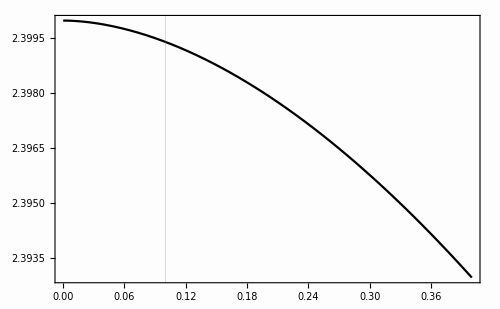

```mathematica
SetDirectory[NotebookDirectory[]];

Normal[φϕSolSeries[δ]]/.replacement1/.eS->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.φϕS->GoldenAngle/.δ->DELTA//Re;

Show[

Plot[%,{DELTA,0,δmax},PlotStyle->Black],

ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\varphi_{\\phi(0)}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["phiPHISol plot.png",%];
```

## Solution φr[δ]

Implementation of the solution

```mathematica
φrSol=Function[{δ},φrS+1/(288 eS^3 (3+eS)^3 𝒜[eS]^2)(-72 eS^4 √(eS (1+eS)) (3+4 eS+eS^2) π δ^2 𝒜[eS]+48 eS^2 (3 eS √(eS (1+eS))+4 √(eS^5 (1+eS))+√(eS^7 (1+eS))) π δ^3 Log[δ] 𝒢δ[eS]+eS δ^3 (3 eS 𝒜[eS] ((9 eS √(eS (1+eS))+8 √(eS^5 (1+eS))-15 √(eS^7 (1+eS))-2 √(eS^9 (1+eS))) π+32 (3+eS)^3 𝒩r[eS])+2 π (24 eS (3 eS √(eS (1+eS))+4 √(eS^5 (1+eS))+√(eS^7 (1+eS))) ℱδ[eS]-8 (3 eS √(eS (1+eS))+4 √(eS^5 (1+eS))+√(eS^7 (1+eS))) (eS+3 ℬ[eS]) 𝒢δ[eS]+3 eS (-3 √(eS^5 (1+eS))-√(eS^7 (1+eS))+3 √(eS^9 (1+eS))+√(eS^11 (1+eS))) 𝒜'[eS]))+9 ⅇ^(-(3 ℬ[eS])/eS) ExpIntegralEi[3 (Log[δ]+ℬ[eS]/eS)] (eS 𝒜[eS] (32 eS (3+eS)^3 ℳr[eS]-ℬ[eS] ((-8 eS^2 √(eS (1+eS))+8 √(eS^5 (1+eS))+15 eS √(eS^5 (1+eS))-15 √(eS^7 (1+eS))+2 eS √(eS^7 (1+eS))-2 √(eS^9 (1+eS))) π+32 (3+eS)^3 𝒩r[eS]))+2 π (8 eS^2 (3 eS √(eS (1+eS))+4 √(eS^5 (1+eS))+√(eS^7 (1+eS))) ℰδ[eS]+ℬ[eS] (-8 eS (3 eS √(eS (1+eS))+4 √(eS^5 (1+eS))+√(eS^7 (1+eS))) ℱδ[eS]+8 (3 eS √(eS (1+eS))+4 √(eS^5 (1+eS))+√(eS^7 (1+eS))) ℬ[eS] 𝒢δ[eS]+eS (-3 eS^2 √(eS (1+eS))+3 √(eS^5 (1+eS))+√(eS^7 (1+eS))-3 √(eS^9 (1+eS))-√(eS^11 (1+eS))+eS (-√(eS^5 (1+eS))+3 √(eS^7 (1+eS))+√(eS^9 (1+eS)))) 𝒜'[eS]))))];
```

Series expansion of the solution

```mathematica
Series[φrSol[δ],{δ,0,2}]/.Floor[1/2+Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->1/.Floor[Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->0/.Floor[-Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->-1
```

φrS-((eS √(eS (1+eS)) (3+4 eS+eS^2) π) δ^2)/(4 ((3+eS)^3 𝒜[eS]))+O[δ]^3

```mathematica
(*Series[φrSol[δ]/.Log[δ]->LOG,{δ,0,3}]/.Floor[1/2+Arg[LOG+ℬ[eS]/eS]/(2 π)]->1/.Floor[Arg[LOG+ℬ[eS]/eS]/(2 π)]->0/.Floor[-Arg[LOG+ℬ[eS]/eS]/(2 π)]->-1;
Series[Normal[%],{LOG,-∞,2}]/.Floor[-Arg[-eS/(eS LOG+ℬ[eS])]/(2 π)]->0/.Floor[Arg[ℬ[eS]/(eS LOG+ℬ[eS])]/(2 π)]->0/.Floor[-Arg[-LOG-ℬ[eS]/eS]/(2 π)]->0/.Floor[-Arg[LOG+ℬ[eS]/eS]/(2 π)]->-1/.Floor[-Arg[eS/(eS LOG+ℬ[eS])]/(2 π)]->-1/.Floor[Arg[ℬ[eS]/eS]/(2 π)]->0;
Simplify[%,{1>eS>0}];
Collect[Normal[%]/.ⅇ^(3 LOG)->δ^3/.LOG->Log[δ],{δ,Log[δ]}]*)
```

```mathematica
φrSolSeries=Function[δ,φrS-((eS √(eS (1+eS)) (3+4 eS+eS^2) π) δ^2)/(4 ((3+eS)^3 𝒜[eS]))+((3 eS √(eS (1+eS))+4 √(eS^5 (1+eS))+√(eS^7 (1+eS))) π δ^3 Log[δ] 𝒢δ[eS])/(6 eS (3+eS)^3 𝒜[eS]^2)+O[δ]^3];
```

Check that φrSol is solution of the asymptotic equations

```mathematica
check=Simplify[Normal[Series[dφrdδ,{δ,0,1}]]-Normal[φrSolSeries'[δ]],{1>eS>0,δ>0}]
```

0

Save Plots

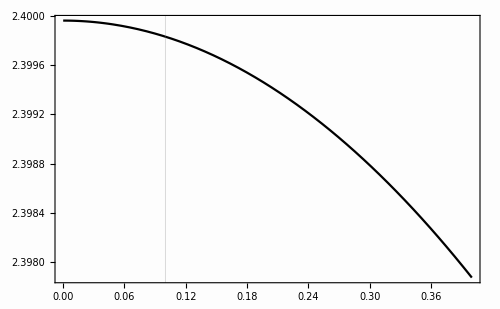

```mathematica
SetDirectory[NotebookDirectory[]];

Normal[φrSolSeries[δ]]/.replacement1/.eS->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.φrS->GoldenAngle/.δ->DELTA//Re;

Show[

Plot[%,{DELTA,0,δmax},PlotStyle->Black],

ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\varphi_{r(0)}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["phiRSol plot.png",%];
```

## Solution δ[ψr]

The solution δ[ψr] has the structure:

Function[ψr,Exp[1/2 ProductLog[-1,XX]  + Log[ Sqrt[1/ⅇ^(-1+(2 ℬ[eS])/eS)]] ]]

Where 

XX = 1/eS 4 ⅇ^(-1+(2 ℬ[eS])/eS) (CONST[ψS]𝒜[eS]-1/(√(eS/(1+eS)))4 (3+eS)^2 M  ϵ((√eS ArcTan[(√eS-ⅈ Tan[ψr/4])/(√(-1-eS))])/(√(-1-eS) (3+eS)^2)+(√eS ArcTan[(√eS+ⅈ Tan[ψr/4])/(√(-1-eS))])/(√(-1-eS) (3+eS)^2)-(√2 √eS (-11+3 eS^2) ArcTan[(2 √eS-√2 √(1+eS) Tan[ψr/4])/(√(2-2 eS))])/((1-eS)^(3/2) (1+eS)^2 (3+eS)^2)-(√2 √eS (-11+3 eS^2) ArcTan[(2 √eS+√2 √(1+eS) Tan[ψr/4])/(√(2-2 eS))])/((1-eS)^(3/2) (1+eS)^2 (3+eS)^2)-(2 eS Cos[ψr/2])/((-1+eS) (1+eS) (3+eS) (1+eS Cos[ψr]))+Log[Cos[ψr/4]]/(1+eS)^2-Log[Sin[ψr/4]]/(1+eS)^2) 𝒜[eS]);

Implementation of the solution

```mathematica
δSolψr=Function[{ψr},ⅇ^(1/2 ProductLog[-1,(4 ⅇ^(-1+(2 ℬ[eS])/eS) (CONST[ψS]𝒜[eS]-(4 (3+eS)^2 M ϵ ((√eS ArcTan[(√eS-ⅈ Tan[ψr/4])/(√(-1-eS))])/(√(-1-eS) (3+eS)^2)+(√eS ArcTan[(√eS+ⅈ Tan[ψr/4])/(√(-1-eS))])/(√(-1-eS) (3+eS)^2)-(√2 √eS (-11+3 eS^2) ArcTan[(2 √eS-√2 √(1+eS) Tan[ψr/4])/(√(2-2 eS))])/((1-eS)^(3/2) (1+eS)^2 (3+eS)^2)-(√2 √eS (-11+3 eS^2) ArcTan[(2 √eS+√2 √(1+eS) Tan[ψr/4])/(√(2-2 eS))])/((1-eS)^(3/2) (1+eS)^2 (3+eS)^2)-(2 eS Cos[ψr/2])/((-1+eS) (1+eS) (3+eS) (1+eS Cos[ψr]))+Log[Cos[ψr/4]]/(1+eS)^2-Log[Sin[ψr/4]]/(1+eS)^2) 𝒜[eS])/(√(eS/(1+eS)))))/eS]) √(ⅇ^(1-(2 ℬ[eS])/eS))];
```

```mathematica
constant=CONST[ψS]->-1/((-1+eS)^(3/2) √eS (1+eS)^2 (1+eS Cos[ψS]))4 M ϵ(11 √2 √(-eS (1+eS)) ArcTan[(√2 √eS-√(1+eS) Tan[ψS/4])/(√(1-eS))]+ⅈ √2 (11 √(eS (1+eS))-3 √(eS^5 (1+eS))) ArcTan[(√2 √eS+√(1+eS) Tan[ψS/4])/(√(1-eS))]+3 ⅈ √2 eS^(5/2) √(1+eS) ArcTan[(-2 √eS+√2 √(1+eS) Tan[ψS/4])/(√(2-2 eS))]+11 ⅈ √2 eS^(3/2) √(1+eS) ArcTan[(√2 √eS-√(1+eS) Tan[ψS/4])/(√(1-eS))] Cos[ψS]+11 ⅈ √2 eS^(3/2) √(1+eS) ArcTan[(√2 √eS+√(1+eS) Tan[ψS/4])/(√(1-eS))] Cos[ψS]-3 ⅈ √2 eS^(7/2) √(1+eS) ArcTan[(√2 √eS+√(1+eS) Tan[ψS/4])/(√(1-eS))] Cos[ψS]+3 ⅈ √2 eS^(7/2) √(1+eS) ArcTan[(-2 √eS+√2 √(1+eS) Tan[ψS/4])/(√(2-2 eS))] Cos[ψS]+ArcTan[(√eS-ⅈ Tan[ψS/4])/(√(-1-eS))] (√(-((-1+eS) eS))+√(-((-1+eS) eS^3))-√((1-eS) eS^5)-√((1-eS) eS^7)+(√(-((-1+eS) eS^3))+√(-((-1+eS) eS^5))-√((1-eS) eS^7)-√((1-eS) eS^9)) Cos[ψS])+ArcTan[(-ⅈ √eS+Tan[ψS/4])/(√(1+eS))] (√(-((-1+eS) eS))+√(-((-1+eS) eS^3))-√((1-eS) eS^5)-√((1-eS) eS^7)+(√(-((-1+eS) eS^3))+√(-((-1+eS) eS^5))-√((1-eS) eS^7)-√((1-eS) eS^9)) Cos[ψS])-3 eS √(-1+eS^2) Log[Cos[ψS/4]]-5 eS^2 √(-1+eS^2) Log[Cos[ψS/4]]-eS^3 √(-1+eS^2) Log[Cos[ψS/4]]+9 eS √(-1+eS^2) Cos[ψS] Log[Cos[ψS/4]]-3 eS^2 √(-1+eS^2) Cos[ψS] Log[Cos[ψS/4]]-5 eS^3 √(-1+eS^2) Cos[ψS] Log[Cos[ψS/4]]-eS^4 √(-1+eS^2) Cos[ψS] Log[Cos[ψS/4]]+√(-1+eS^2) (2 eS (1+eS) (3+eS) Cos[ψS/2]+9 Log[Cos[ψS/4]])-9 √(-1+eS^2) Log[Sin[ψS/4]]+3 eS √(-1+eS^2) Log[Sin[ψS/4]]+5 eS^2 √(-1+eS^2) Log[Sin[ψS/4]]+eS^3 √(-1+eS^2) Log[Sin[ψS/4]]-9 eS √(-1+eS^2) Cos[ψS] Log[Sin[ψS/4]]+3 eS^2 √(-1+eS^2) Cos[ψS] Log[Sin[ψS/4]]+5 eS^3 √(-1+eS^2) Cos[ψS] Log[Sin[ψS/4]]+eS^4 √(-1+eS^2) Cos[ψS] Log[Sin[ψS/4]]);
```

Check that δSolψr is solution of the asymptotic equations

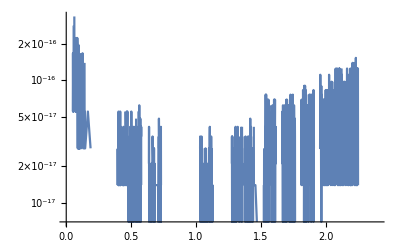

```mathematica
Normal[dδdψr]-δSolψr'[ψr]/.δ->δSolψr[ψr]/.constant/.replacement1/.{eS->es,M->1,ϵ->ϵValue}/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψS->GoldenAngle;
LogPlot[%//Re,{ψr,0,GoldenAngle}]
```

Save Plots

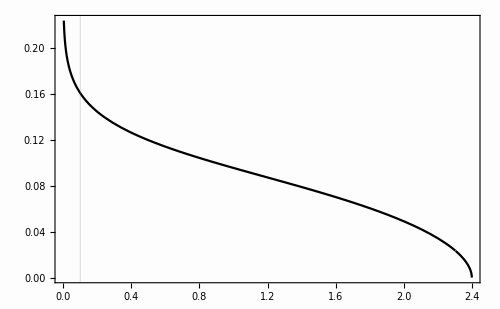

```mathematica
SetDirectory[NotebookDirectory[]];

δSolψr[ψr]/.constant/.replacement1/.{eS->es,M->1,ϵ->ϵValue}/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψS->GoldenAngle/.ψr->Ψ;

Show[

Plot[%,{Ψ,0,GoldenAngle},PlotStyle->Black],

ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\psi_r","FontSize"->18],MaTeX["\\delta","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["DeltaSol(PSI) plot.png",%];
```

## Solution δ[t]

Implementation of the solution

```mathematica
δSol=Function[{t},ⅇ^(1/2-ℬ[eS]/eS+1/2 ProductLog[-1,(4 ⅇ^(-1+(2 ℬ[eS])/eS) (t-tS) 𝒜[eS])/eS])];
```

This is valid for t < tS only. Typically, we set tS = 0.

Check that δSol is solution of the asymptotic equations

```mathematica
timeMax=t/.FindRoot[δmax-δSol[t]/.replacement1/.eS->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.φrS->GoldenAngle,{t,-10,-0.1}][[1]]
```

-0.121297

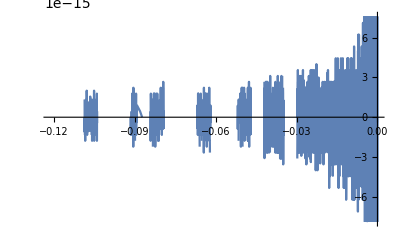

```mathematica
δSol'[t]-dδdtLeading/.δ->δSol[t]/.replacement1/.eS->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.φrS->GoldenAngle/.t->u;
Plot[%,{u,timeMax,0}]
```

This is zero everywhere !

Save Plots

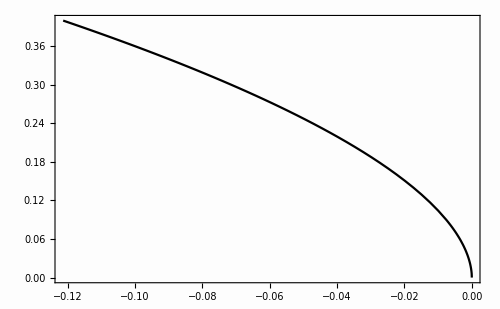

```mathematica
SetDirectory[NotebookDirectory[]];

Normal[δSol[t]]/.replacement1/.eS->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.t->U;

Show[

Plot[%,{U,timeMax,0},PlotStyle->Black],

ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\tilde{t} - \\tilde{t}_\\star","FontSize"->18],MaTeX["\\delta","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["delta of t plot.png",%];
```

## Solution δ[τ]

Implementation of the solution

```mathematica
δSolτ=Function[{τ},ⅇ^(1/2 (1+ProductLog[-1,(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]-(2 ℬ[eS])/eS))];
```

Check that δSolτ is solution of the asymptotic equations (leading order)

```mathematica
dδdτLeading=Normal[Series[dδdτ,{δ,0,-1}]]
```

-(√(9-eS^2) (-2-eS+eS Cos[ψrS]) 𝒜[eS])/(2 √2 (3+eS) δ (eS Log[δ]+ℬ[eS]))

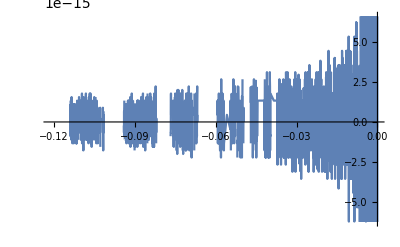

```mathematica
δSolτ'[τ]-dδdτLeading/.δ->δSolτ[τ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψrS->GoldenAngle/.τS->0/.τ->u;
Plot[%,{u,timeMax,0}]
```

This is zero everywhere !

## Solution t[δ]

Implementation of the solution

```mathematica
tSolFirstOrder=Function[δ,tS+eS/(4 𝒜[eS])δ^2 Log[δ^2 ⅇ^(-1+(2 ℬ[eS])/eS)]];
```

```mathematica
tSolNextOrder=Function[δ,tS+δ^2 ((eS Log[δ])/(2 𝒜[eS])-(eS-2 ℬ[eS])/(4 𝒜[eS]))+δ^3 (-(Log[δ]^2 𝒢δ[eS])/(3 𝒜[eS]^2)+(Log[δ] (24 𝒢δ[eS]-9/2 (-((-1+eS) 𝒜[eS])+8 ℱδ[eS]+(-1+eS) eS 𝒜'[eS])))/(108 𝒜[eS]^2)-1/(27 𝒜[eS]^2)(3/8 (-1+eS) 𝒜[eS]+9 ℰδ[eS]-3 ℱδ[eS]+2 𝒢δ[eS]-3/8 (-1+eS) eS 𝒜'[eS]+9/8 (-1+eS) (ℬ[eS] 𝒜'[eS]-𝒜[eS] ℬ'[eS])))];
```

```mathematica
Series[tSolFirstOrder[δ]-tSolNextOrder[δ],{δ,0,2}]
```

-((-eS+2 eS Log[δ]-eS Log[ⅇ^(-1+(2 ℬ[eS])/eS) δ^2]+2 ℬ[eS]) δ^2)/(4 𝒜[eS])+O[δ]^3

This is valid for t < tS only. Typically, we set tS = 0.
In this section, we deal with tSolFirstOrder s. This is just for convenience.
Actually, tSolNextOrder solves the equation t’[δ] == 1/dδdtup to the order O(δ^3 Log[δ]^2).

Check that tSol is solution of the asymptotic equations

```mathematica
FullSimplify[tSolFirstOrder'[δ]-1/dδdtLeading,{1>eS>0,δ>0}]/.Log[ⅇ^((2 ℬ[eS])/eS)]->(2 ℬ[eS])/eS
```

0

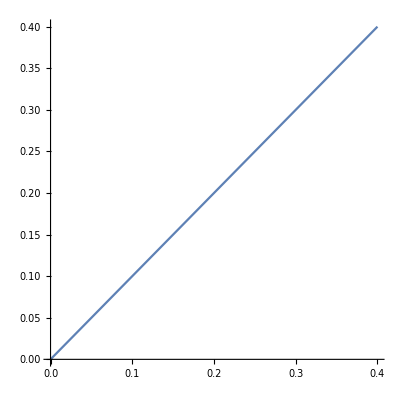

```mathematica
δSol[tSolFirstOrder[δ]]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.δ->DELTA;
Plot[%,{DELTA,0,δmax},AspectRatio->1]
```

We recover δ = δ as expected.

Save Plots

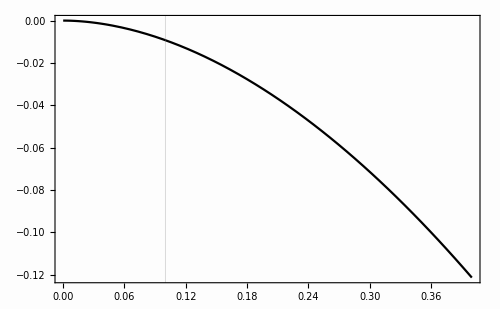

```mathematica
SetDirectory[NotebookDirectory[]];

tSolFirstOrder[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.δ->DELTA;

Show[

Plot[%,{DELTA,0,δmax},PlotStyle->Black],

ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\tilde{t}-\\tilde{t}_\\star","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["t of delta plot.png",%];
```

Higher order

```mathematica
Series[tSolNextOrder[δ],{δ,0,3}]
```

tS+((-eS+2 eS Log[δ]+2 ℬ[eS]) δ^2)/(4 𝒜[eS])+1/(216 𝒜[eS]^2)(3 𝒜[eS]-3 eS 𝒜[eS]-9 Log[δ] 𝒜[eS]+9 eS Log[δ] 𝒜[eS]-72 ℰδ[eS]+24 ℱδ[eS]-72 Log[δ] ℱδ[eS]-16 𝒢δ[eS]+48 Log[δ] 𝒢δ[eS]-72 Log[δ]^2 𝒢δ[eS]-3 eS 𝒜'[eS]+3 eS^2 𝒜'[eS]+9 eS Log[δ] 𝒜'[eS]-9 eS^2 Log[δ] 𝒜'[eS]+9 ℬ[eS] 𝒜'[eS]-9 eS ℬ[eS] 𝒜'[eS]-9 𝒜[eS] ℬ'[eS]+9 eS 𝒜[eS] ℬ'[eS]) δ^3+O[δ]^4

## Solution τ[t]

Implementation

```mathematica
τSolt=Function[t,τS+1/((3+eS) (1+Cos[ψrS])^2 𝒜[eS])√2 eS √(9-eS^2) (2+eS-eS Cos[ψrS])^2 (ⅇ^(1/2 (1+ProductLog[-1,(4 ⅇ^(-1+(2 ℬ[eS])/eS) (t-tS) 𝒜[eS])/eS]-(2 ℬ[eS])/eS)) (1+Cos[ψrS])+8 (-2-eS+eS Cos[ψrS]) Log[1+(ⅇ^(1/2 (1+ProductLog[-1,(4 ⅇ^(-1+(2 ℬ[eS])/eS) (t-tS) 𝒜[eS])/eS]-(2 ℬ[eS])/eS)) (1+Cos[ψrS]))/(8 (-2-eS+eS Cos[ψrS]))]+16 (-2-eS+eS Cos[ψrS]) PolyLog[2,-(ⅇ^(1/2 (1+ProductLog[-1,(4 ⅇ^(-1+(2 ℬ[eS])/eS) (t-tS) 𝒜[eS])/eS]-(2 ℬ[eS])/eS)) (1+Cos[ψrS]))/(8 (-2-eS+eS Cos[ψrS]))]-ⅇ^(1/2 (1+ProductLog[-1,(4 ⅇ^(-1+(2 ℬ[eS])/eS) (t-tS) 𝒜[eS])/eS]-(2 ℬ[eS])/eS)) (1+Cos[ψrS]) ProductLog[-1,(4 ⅇ^(-1+(2 ℬ[eS])/eS) (t-tS) 𝒜[eS])/eS]+8 (-2-eS+eS Cos[ψrS]) Log[1+(ⅇ^(1/2 (1+ProductLog[-1,(4 ⅇ^(-1+(2 ℬ[eS])/eS) (t-tS) 𝒜[eS])/eS]-(2 ℬ[eS])/eS)) (1+Cos[ψrS]))/(8 (-2-eS+eS Cos[ψrS]))] ProductLog[-1,(4 ⅇ^(-1+(2 ℬ[eS])/eS) (t-tS) 𝒜[eS])/eS])];
```

```mathematica
dτdt=Simplify[1/(Normal[dtdτ]/.δ->δSol[t])/.EnS->KerrGeoEnergy[0,6+2eS,eS,1]/.rS->((6+2eS)M)/(1+eS Cos[ψrS]),{1>eS>0,t<tS}];
```

Check that the τSolt is solution of the diff equation

```mathematica
Simplify[τSolt'[t]-dτdt]
```

0

Expansion of τSolt[t] for small t

```mathematica
(*We define the new coefficients α, β1 and β2 for the sake of readibility.*)
Replacementα=α->(4 ⅇ^(-1+(2 ℬ[eS])/eS) 𝒜[eS])/eS;
Replacementβ={β1->-(2 √2 (3+eS))/(√(9-eS^2) (-2-eS+eS Cos[ψrS])),β2->-(ⅇ^(1/2-ℬ[eS]/eS) (3+eS) (1+Cos[ψrS]))/(2 √2 √(9-eS^2) (2+eS-eS Cos[ψrS])^2)};
```

```mathematica
τSoltScheme=(2 (-ⅇ^(1/2 ProductLog[α Δt]) β2-β1 Log[1+(ⅇ^(1/2 ProductLog[α Δt]) β2)/β1]-2 β1 PolyLog[2,-(ⅇ^(1/2 ProductLog[α Δt]) β2)/β1]+ⅇ^(1/2 ProductLog[α Δt]) β2 ProductLog[α Δt]-β1 Log[1+(ⅇ^(1/2 ProductLog[α Δt]) β2)/β1] ProductLog[α Δt]))/(α β2^2)/.ProductLog[Δt α]->ProductLog[-1,Δt α]/.ⅇ^(1/2 ProductLog[-1,Δt α])->Sqrt[(α Δt)/ProductLog[-1,α Δt]] (*Δt stands for t - tS*)(*This is a schematic version of the solution τ[t]*)
```

(2 (-β1 Log[1+(β2 √((α Δt)/ProductLog[-1,α Δt]))/β1]-2 β1 PolyLog[2,-(β2 √((α Δt)/ProductLog[-1,α Δt]))/β1]-β2 √((α Δt)/ProductLog[-1,α Δt])-β1 Log[1+(β2 √((α Δt)/ProductLog[-1,α Δt]))/β1] ProductLog[-1,α Δt]+β2 √((α Δt)/ProductLog[-1,α Δt]) ProductLog[-1,α Δt]))/(α β2^2)

The argument -(β2 √((α Δt)/ProductLog[-1,α Δt]))/β1 , that we call XXX , is small and we can expand for XXX -> 0.

```mathematica
ReplacementXXX=XXX->-(β2 √((α Δt)/ProductLog[-1,α Δt]))/β1;
replacementPolyLog=PolyLog[2,-(β2 √((α Δt)/ProductLog[-1,α Δt]))/β1]->Series[PolyLog[2,XXX],{XXX,0,5}];
replacementLOG=Log[1+(β2 √((α Δt)/ProductLog[-1,α Δt]))/β1]->Series[Log[1-XXX],{XXX,0,5}];
replacementW=ProductLog[-1,α Δt]->(L1-L2+L2/L1+(L2(L2-2))/(2 L1^2)+(L2(6-9 L2+2 L2^2))/(6 L1^3)/.L2->Log[-L1]);(*L1 is for Log[-α Δt]*)
```

```mathematica
dev1=Series[τSoltScheme/.replacementPolyLog/.replacementLOG/.ProductLog[-1,α Δt]->(α β2^2 Δt)/(XXX^2 β1^2)//FullSimplify,{XXX,0,1}]//Simplify;
τAsymptot=Simplify[Series[Simplify[Normal[dev1]/.ReplacementXXX]/.replacementW,{L1,-∞,2}],{1>eS>0,Δt<0,α>0}] (*L1 is Log[-α (t-tS)]*)
```

Δt/β1-(2 (√L1 β2 Δt √((α Δt)/L1)) √(1/L1))/(3 β1^2)-((√L1 β2 Δt √((α Δt)/L1) Log[-L1]) (1/L1)^(3/2))/(3 β1^2)+O[1/L1]^(5/2)

```mathematica
FullExpressionτAsymptot=Simplify[Series[Normal[τAsymptot],{Δt,0,2}]/.L1->Log[-α Δt],Log[-α Δt]<0]/.Replacementα/.Replacementβ
```

-((√(9-eS^2) (-2-eS+eS Cos[ψrS])) Δt)/(2 (√2 (3+eS)))+(ⅇ^(3/2-(3 ℬ[eS])/eS) eS √(9-eS^2) (1+Cos[ψrS]) (Log[-Log[-(4 ⅇ^(-1+(2 ℬ[eS])/eS) Δt 𝒜[eS])/eS]]+2 Log[-(4 ⅇ^(-1+(2 ℬ[eS])/eS) Δt 𝒜[eS])/eS]) ((ⅇ^(-1+(2 ℬ[eS])/eS) 𝒜[eS])/(eS Log[-(4 ⅇ^(-1+(2 ℬ[eS])/eS) Δt 𝒜[eS])/eS]))^(3/2) Δt^(3/2))/(24 √2 (3+eS) 𝒜[eS])+O[Δt]^(5/2)

## Solution t[τ]

We can find t[τ] by inverting the asymptotic expression of τ[t]. The following result is valid up to order (τ-τS)^(3/2).

Asymptotic solution t[τ]

```mathematica
tAsymptot=Function[τ,tS+β1 (τ-τS+(β2 (β1 (τ-τS))^(3/2) (α/Log[-α β1 (τ-τS)])^(3/2) (2 Log[-α β1 (τ-τS)]+Log[-Log[-α β1 (τ-τS)]]))/(3 α β1^2))];
```

check

```mathematica
(*Compute the expansion for τ close to τS: define Δτ := τ-τS and expand for Δτ close to 0.*)
```

```mathematica
Simplify[Series[Simplify[Normal[τAsymptot]/.L1->Log[-α Δt]/.Δt->tAsymptot[τ]-tS/.Log[-α β1 (τ-τS)]->LOG/.τ->Δτ+τS],{Δτ,0,2}]/.Log[-α β1 Δτ]->LOG,LOG<0]/.√(α/LOG) √β1-√((α β1)/LOG)->0
```

Δτ-((√(α/LOG) √((α β1)/LOG) β2^2 (4 LOG (1-LOG+3 LOG^2)+2 (1-4 LOG+6 LOG^2) Log[-LOG]+3 (-1+LOG) Log[-LOG]^2)) Δτ^2)/(18 (LOG^3 β1^(3/2)))-((((α β1)/LOG)^(3/2) β2^3 (2 LOG+Log[-LOG])^2 (2 (-8+7 LOG-4 LOG^2+3 LOG^3)+3 (5-4 LOG+LOG^2) Log[-LOG])) Δτ^(5/2))/(216 (LOG^5 β1^3))+O[Δτ]^3

We obtain that Δτ = Δτ up to order Δτ^2, as expected by the fact that tAsymptot[τ] is valid up to order Δτ^(3/2).

## Solution ψr[t]

The solution δ[ψr] is compatible with the following solution

```mathematica
ψrSol=Function[t,ψS+((t-tS) (2+eS-eS Cos[ψS]) (1+eS Cos[ψS])^2 Sin[ψS/2])/(4 √(1+1/eS) (3+eS)^2 M ϵ)];
```

This solution is nothing but the first two terms of the Taylor development of ψr accross the separatrix (t → tS).

```mathematica
𝒻rSlow[δ_,e_,ψr_]:=1/ϵ(√(2 e+δ-2 e Cos[ψr]) (4+2 e+δ-2 e Cos[ψr]) (1+e Cos[ψr])^2)/(M (6+2 e+δ)^2 √((4+δ) (4+4 e+δ)))(*This is this is dψr/d\tilde{t}, slow time *)
```

```mathematica
Simplify[ψrSol[t]-(ψS+𝒻rSlow[0,eS,ψS](t-tS)),{1>eS>0,2π>ψS>0}] /.(√2 √((1+eS) (1-Cos[ψS]))-2 √(1+eS) Sin[ψS/2])->0    (*t is the slow time*)
```

0

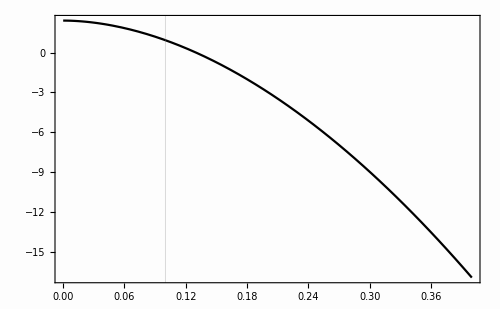

```mathematica
SetDirectory[NotebookDirectory[]];

ψrSol[tSolFirstOrder[δ]]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψS->GoldenAngle/.{M->1,ϵ->ϵValue}/.δ->DELTA;

Show[

Plot[%,{DELTA,0,δmax},PlotStyle->Black],

ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["\\psi_r","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["psi of delta plot.png",%];
```

```mathematica
Simplify[Series[ψrSol[t],{t,tS,1}],{1>eS>0}]//Simplify
```

ψS+((2+eS-eS Cos[ψS]) (1+eS Cos[ψS])^2 Sin[ψS/2] (t-tS))/(4 √(1+1/eS) (3+eS)^2 M ϵ)+O[t-tS]^2

```mathematica
𝒻rSlow[0,eS,ψS](t-tS)//Simplify
```

((t-tS) (4+2 eS-2 eS Cos[ψS]) √(eS-eS Cos[ψS]) (1+eS Cos[ψS])^2)/(8 √2 √(1+eS) (3+eS)^2 M ϵ)

```mathematica
Simplify[Normal[1/dδdψr/.ψr->ψr[δ]],{1>eS>0,δ>0,2π>ψr>0}];
Simplify[DSolve[%==ψr'[δ],ψr,δ]/.C[1]->ψS/.ψr[0]->ψS,{1>eS>0,δ>0,2π>ψS>0}]
```

{{ψr→Function[{δ},ψS-(δ^2 (1+eS Cos[ψS])^2 (-2-eS+eS Cos[ψS]) √((eS Sin[ψS/2]^2)/(1+eS)) (eS (-1+2 Log[δ])+2 ℬ[eS]))/(16 (3+eS)^2 M ϵ 𝒜[eS])]}}

```mathematica
ψrSol[tSolFirstOrder[δ]]/.Log[ⅇ^(-1+(2 ℬ[eS])/eS) δ^2]->2Log[δ]-1+(2 ℬ[eS])/eS//Simplify
```

ψS-((-2-eS+eS Cos[ψS]) (δ+eS δ Cos[ψS])^2 Sin[ψS/2] (eS (-1+2 Log[δ])+2 ℬ[eS]))/(16 √(1+1/eS) (3+eS)^2 M ϵ 𝒜[eS])

## Construction of the critical function C

We refer to the article 10.1103/PhysRevD.50.3816 and define the critical function by 

C := (d Log[e])/(d Log[p]) = (6+2 e[δ]+δ)/e[δ]((2 e'[δ]+1)/e'[δ])^(-1) 

Thanks to the solutions at hand, we cn reproduce the results of the paper cited here in the sense that we reproduce the value of the critical function at leading order.

```mathematica
CriticalFunction=(6+2 eSol[δ]+δ)/eSol[δ]((2 eSol'[δ]+1)/eSol'[δ])^(-1);
```

```mathematica
CriticalFunctionLeadingOrder=Series[CriticalFunction,{δ,0,0}]/.Floor[Arg[2 Log[δ]+(2 ℬ[eS])/eS]/(2 π)]->0/.Floor[1/2+Arg[2 Log[δ]+(2 ℬ[eS])/eS]/(2 π)]->1/.Floor[-Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->-1/.Floor[Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->0/.Floor[1/2+Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->1/.(-ⅈ π+1/2 (ⅈ π-Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]+Log[(2 (eS Log[δ]+ℬ[eS]))/eS]))->0/.-π+1/2 (π+ⅈ Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]-ⅈ Log[(2 (eS Log[δ]+ℬ[eS]))/eS])->0//Simplify
```

(-1+eS)/eS+O[δ]^1

```mathematica
CriticalFunctionNextOrder=Collect[Normal[Series[Normal[Series[CriticalFunction,{δ,0,1}]/.Floor[Arg[2 Log[δ]+(2 ℬ[eS])/eS]/(2 π)]->0/.Floor[1/2+Arg[2 Log[δ]+(2 ℬ[eS])/eS]/(2 π)]->1/.Floor[-Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->-1/.Floor[Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->0/.Floor[1/2+Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->1/.(-ⅈ π+1/2 (ⅈ π-Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]+Log[(2 (eS Log[δ]+ℬ[eS]))/eS]))->0/.-π+1/2 (π+ⅈ Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]-ⅈ Log[(2 (eS Log[δ]+ℬ[eS]))/eS])->0]/.Log[δ]->LOG,{LOG,-∞,3}]],{δ,LOG}]
```

(-1+eS)/eS+δ (-(4 LOG (-8 𝒢e[eS]-𝒢δ[eS]+eS 𝒢δ[eS]))/(eS^2 (3+eS) 𝒜[eS])+(-3 eS 𝒜[eS]-2 eS^2 𝒜[eS]+5 eS^3 𝒜[eS]+256 eS ℱe[eS]+32 eS ℱδ[eS]-32 eS^2 ℱδ[eS]-256 ℬ[eS] 𝒢e[eS]-32 ℬ[eS] 𝒢δ[eS]+32 eS ℬ[eS] 𝒢δ[eS])/(8 eS^3 (3+eS) 𝒜[eS])-(4 (-8 eS^2 ℰe[eS]-eS^2 ℰδ[eS]+eS^3 ℰδ[eS]+8 eS ℬ[eS] ℱe[eS]+eS ℬ[eS] ℱδ[eS]-eS^2 ℬ[eS] ℱδ[eS]-8 ℬ[eS]^2 𝒢e[eS]-ℬ[eS]^2 𝒢δ[eS]+eS ℬ[eS]^2 𝒢δ[eS]))/(eS^4 (3+eS) LOG 𝒜[eS])+(4 (-8 eS^2 ℬ[eS] ℰe[eS]-eS^2 ℬ[eS] ℰδ[eS]+eS^3 ℬ[eS] ℰδ[eS]+8 eS ℬ[eS]^2 ℱe[eS]+eS ℬ[eS]^2 ℱδ[eS]-eS^2 ℬ[eS]^2 ℱδ[eS]-8 ℬ[eS]^3 𝒢e[eS]-ℬ[eS]^3 𝒢δ[eS]+eS ℬ[eS]^3 𝒢δ[eS]))/(eS^5 (3+eS) LOG^2 𝒜[eS])-(4 (-8 eS^2 ℬ[eS]^2 ℰe[eS]-eS^2 ℬ[eS]^2 ℰδ[eS]+eS^3 ℬ[eS]^2 ℰδ[eS]+8 eS ℬ[eS]^3 ℱe[eS]+eS ℬ[eS]^3 ℱδ[eS]-eS^2 ℬ[eS]^3 ℱδ[eS]-8 ℬ[eS]^4 𝒢e[eS]-ℬ[eS]^4 𝒢δ[eS]+eS ℬ[eS]^4 𝒢δ[eS]))/(eS^6 (3+eS) LOG^3 𝒜[eS]))

## Construction of r[δ]

We compute the radius up to the order δ^1.

```mathematica
radius[δ_]=M(6+2 eSol[δ]+δ)/(1+eSol[δ]Cos[ψrSol[tSolNextOrder[δ]]]);
```

```mathematica
inter=Simplify[radius[δ],{1>eS>0,δ>0}]
```

(M (6+2 eS+δ+1/32 (-8 δ+8 eS δ-δ^2/2+(eS δ^2)/2+(4 δ^2 Log[δ] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))/(eS 𝒜[eS])-(2 δ^2 (-16 eS ℱe[eS]+2 (-1+eS) eS ℱδ[eS]-(eS+2 ℬ[eS]) (-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS])))/(eS^2 𝒜[eS])-(8 ⅇ^(-(2 ℬ[eS])/eS) ExpIntegralEi[2 (Log[δ]+ℬ[eS]/eS)] (-8 eS^2 ℰe[eS]+(-1+eS) eS^2 ℰδ[eS]+ℬ[eS] (8 eS ℱe[eS]-(-1+eS) eS ℱδ[eS]-ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))))/(eS^3 𝒜[eS]))))/(1+Cos[ψS-1/(432 √(1+1/eS) (3+eS)^2 M ϵ 𝒜[eS]^2)(2+eS-eS Cos[ψS]) (δ+eS δ Cos[ψS])^2 Sin[ψS/2] (27 𝒜[eS] (eS-2 eS Log[δ]-2 ℬ[eS])+1/2 δ (3 (-1+eS) 𝒜[eS]+72 ℰδ[eS]-24 ℱδ[eS]+16 𝒢δ[eS]-48 Log[δ] 𝒢δ[eS]+72 Log[δ]^2 𝒢δ[eS]-3 (-1+eS) eS 𝒜'[eS]+9 Log[δ] (-((-1+eS) 𝒜[eS])+8 ℱδ[eS]+(-1+eS) eS 𝒜'[eS])+9 (-1+eS) (ℬ[eS] 𝒜'[eS]-𝒜[eS] ℬ'[eS])))] (eS+1/64 (-8 δ+8 eS δ-δ^2/2+(eS δ^2)/2+(4 δ^2 Log[δ] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))/(eS 𝒜[eS])-(2 δ^2 (-16 eS ℱe[eS]+2 (-1+eS) eS ℱδ[eS]-(eS+2 ℬ[eS]) (-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS])))/(eS^2 𝒜[eS])-(8 ⅇ^(-(2 ℬ[eS])/eS) ExpIntegralEi[2 (Log[δ]+ℬ[eS]/eS)] (-8 eS^2 ℰe[eS]+(-1+eS) eS^2 ℰδ[eS]+ℬ[eS] (8 eS ℱe[eS]-(-1+eS) eS ℱδ[eS]-ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))))/(eS^3 𝒜[eS]))))

```mathematica
Simplify[Series[inter,{δ,0,1}]/.Floor[1/2+Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->1/.Floor[-Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->-1/.Floor[Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->0,1>eS>0]
```

(2 (3+eS) M)/(1+eS Cos[ψS])+((3+eS) M (1+Cos[ψS]) δ)/(4 (1+eS Cos[ψS])^2)+O[δ]^2

We plot the radius r[δ] by considering the “easy” solution ψrSol[tSolFirstOrder[δ]] in place of ψrSol[tSolNextOrder[δ]]

```mathematica
radiusSimpler[δ_]=M(6+2 eSol[δ]+δ)/(1+eSol[δ]Cos[ψrSol[tSolFirstOrder[δ]]]);
```

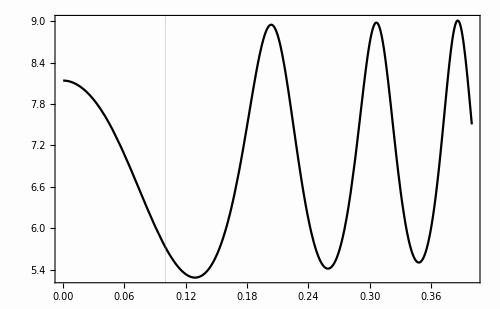

```mathematica
SetDirectory[NotebookDirectory[]];

radiusSimpler[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψS->GoldenAngle/.{M->1,ϵ->ϵValue}/.δ->DELTA;

Show[

Plot[%,{DELTA,0,δmax},PlotStyle->Black,PlotRange->All],

ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["r","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["radius of delta plot.png",%];
```

## Construction of r[t]

We compute the radius up to the order δ^1.

```mathematica
radiusT[t_]=M(6+2 eSol[δSol[t]]+δSol[t])/(1+eSol[δSol[t]]Cos[ψrSol[t]]);
```

```mathematica
radiusTtoplot[t_]=radiusSimpler[δSol[t]];
```

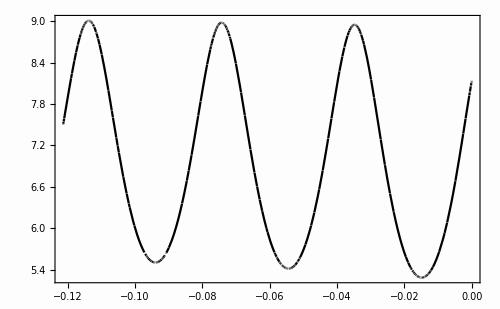

```mathematica
SetDirectory[NotebookDirectory[]];

radiusT[t]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψS->GoldenAngle/.{M->1,ϵ->ϵValue}/.tS->0/.t->TIME;

Show[

Plot[%//Re,{TIME,timeMax,0},PlotStyle->Black,PlotRange->All,PlotPoints->200],

ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\tilde{t}-\\tilde{t}_\\star","FontSize"->18],MaTeX["r","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["radius of t plot.png",%];
```

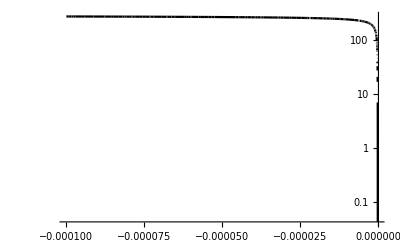

```mathematica
radiusT'[t]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψS->GoldenAngle/.{M->1,ϵ->ϵValue}/.tS->0/.t->TIME;
LogPlot[%//Re,{TIME,-0.0001,0},PlotStyle->Black,PlotRange->All,PlotPoints->300]
```

## Construction of r_a[δ]

The aim here is to show that the value of the apoapsis is constant at leading order in δ

```mathematica
ra[δ_]=M(6+2 eSol[δ]+δ)/(1-eSol[δ]);
```

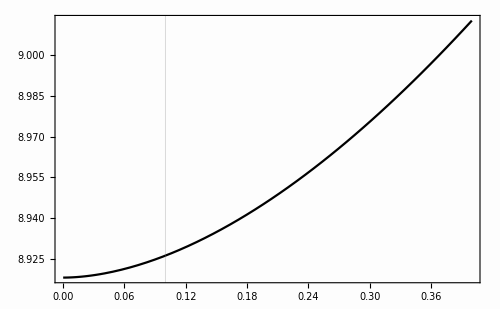

```mathematica
SetDirectory[NotebookDirectory[]];

ra[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψS->GoldenAngle/.{M->1,ϵ->ϵValue}/.δ->DELTA;

Show[

Plot[%,{DELTA,0,δmax},PlotStyle->Black,PlotRange->All],

ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["r_a","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["apoastron(DELTA) plot.png",%];
```

Asymptotic behaviour

```mathematica
raLeading=FullSimplify[Simplify[Series[ra[δ],{δ,0,1}]/.Floor[Arg[2 Log[δ]+(2 ℬ[eS])/eS]/(2 π)]->0/.Floor[1/2+Arg[2 Log[δ]+(2 ℬ[eS])/eS]/(2 π)]->1/.Floor[-Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->-1/.Floor[Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->0/.Floor[1/2+Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->1/.(-ⅈ π+1/2 (ⅈ π-Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]+Log[(2 (eS Log[δ]+ℬ[eS]))/eS]))->0/.-π+1/2 (π+ⅈ Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]-ⅈ Log[(2 (eS Log[δ]+ℬ[eS]))/eS])->0,1>eS>0]/.(ⅈ π+Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]-Log[(2 (eS Log[δ]+ℬ[eS]))/eS])->0/.Log[δ]->LOG,1>eS>0]/.-ⅈ π-Log[-eS LOG-ℬ[eS]]+Log[eS LOG+ℬ[eS]]->0
```

-(2 ((3+eS) M))/(-1+eS)+O[δ]^2

```mathematica
Simplify[Series[ra[δ],{δ,0,2}]/.Floor[Arg[2 Log[δ]+(2 ℬ[eS])/eS]/(2 π)]->0/.Floor[1/2+Arg[2 Log[δ]+(2 ℬ[eS])/eS]/(2 π)]->1/.Floor[-Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->-1/.Floor[Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->0/.Floor[1/2+Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->1/.(-ⅈ π+1/2 (ⅈ π-Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]+Log[(2 (eS Log[δ]+ℬ[eS]))/eS]))->0/.-π+1/2 (π+ⅈ Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]-ⅈ Log[(2 (eS Log[δ]+ℬ[eS]))/eS])->0,1>eS>0]/.(ⅈ π+Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]-Log[(2 (eS Log[δ]+ℬ[eS]))/eS])->0/.Log[δ]->LOG;
Series[%,{LOG,-∞,2}];
raSubLeading=Collect[Normal[%],{δ,LOG}]
```

-(2 (3+eS) M)/(-1+eS)+δ^2 (-(LOG M (-8 𝒢e[eS]-𝒢δ[eS]+eS 𝒢δ[eS]))/(2 (-1+eS)^2 eS 𝒜[eS])+(M (-eS^2 𝒜[eS]+eS^3 𝒜[eS]+64 eS ℱe[eS]+8 eS ℱδ[eS]-8 eS^2 ℱδ[eS]-32 eS 𝒢e[eS]-64 ℬ[eS] 𝒢e[eS]-4 eS 𝒢δ[eS]+4 eS^2 𝒢δ[eS]-8 ℬ[eS] 𝒢δ[eS]+8 eS ℬ[eS] 𝒢δ[eS]))/(16 (-1+eS)^2 eS^2 𝒜[eS])-(M (-8 eS^2 ℰe[eS]-eS^2 ℰδ[eS]+eS^3 ℰδ[eS]+8 eS ℬ[eS] ℱe[eS]+eS ℬ[eS] ℱδ[eS]-eS^2 ℬ[eS] ℱδ[eS]-8 ℬ[eS]^2 𝒢e[eS]-ℬ[eS]^2 𝒢δ[eS]+eS ℬ[eS]^2 𝒢δ[eS]))/(2 (-1+eS)^2 eS^3 LOG 𝒜[eS])-1/(4 (-1+eS)^2 eS^4 LOG^2 𝒜[eS])M (-8 eS^3 ℰe[eS]+16 eS^2 ℬ[eS] ℰe[eS]-eS^3 ℰδ[eS]+eS^4 ℰδ[eS]+2 eS^2 ℬ[eS] ℰδ[eS]-2 eS^3 ℬ[eS] ℰδ[eS]+8 eS^2 ℬ[eS] ℱe[eS]-16 eS ℬ[eS]^2 ℱe[eS]+eS^2 ℬ[eS] ℱδ[eS]-eS^3 ℬ[eS] ℱδ[eS]-2 eS ℬ[eS]^2 ℱδ[eS]+2 eS^2 ℬ[eS]^2 ℱδ[eS]-8 eS ℬ[eS]^2 𝒢e[eS]+16 ℬ[eS]^3 𝒢e[eS]-eS ℬ[eS]^2 𝒢δ[eS]+eS^2 ℬ[eS]^2 𝒢δ[eS]+2 ℬ[eS]^3 𝒢δ[eS]-2 eS ℬ[eS]^3 𝒢δ[eS]))

The O(δ) term of r_a is equal to 0.

We conclude that the apoapsis is constant up to the order δ^1.

## Construction of r_p[δ]

We want to see the way the value of the periastron evolves.

```mathematica
rp[δ_]=M(6+2 eSol[δ]+δ)/(1+eSol[δ]);
```

Asymptotic behaviour

```mathematica
Simplify[Series[rp[δ],{δ,0,2}]/.Floor[Arg[2 Log[δ]+(2 ℬ[eS])/eS]/(2 π)]->0/.Floor[1/2+Arg[2 Log[δ]+(2 ℬ[eS])/eS]/(2 π)]->1/.Floor[-Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->-1/.Floor[Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->0/.Floor[1/2+Arg[Log[δ]+ℬ[eS]/eS]/(2 π)]->1/.(-ⅈ π+1/2 (ⅈ π-Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]+Log[(2 (eS Log[δ]+ℬ[eS]))/eS]))->0/.-π+1/2 (π+ⅈ Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]-ⅈ Log[(2 (eS Log[δ]+ℬ[eS]))/eS])->0,1>eS>0]/.(ⅈ π+Log[-(2 (eS Log[δ]+ℬ[eS]))/eS]-Log[(2 (eS Log[δ]+ℬ[eS]))/eS])->0/.Log[δ]->LOG;
Series[Normal[%],{LOG,-∞,2}];
Collect[Normal[%],{δ,LOG}]
```

(2 (3+eS) M)/(1+eS)+((3+eS) M δ)/(2 (1+eS)^2)+δ^2 ((LOG M (-8 𝒢e[eS]-𝒢δ[eS]+eS 𝒢δ[eS]))/(4 eS (1+eS)^2 𝒜[eS])-(M (-7 eS^2 𝒜[eS]+4 eS^3 𝒜[eS]+3 eS^4 𝒜[eS]+64 eS ℱe[eS]+64 eS^2 ℱe[eS]+8 eS ℱδ[eS]-8 eS^3 ℱδ[eS]-32 eS 𝒢e[eS]-32 eS^2 𝒢e[eS]-64 ℬ[eS] 𝒢e[eS]-64 eS ℬ[eS] 𝒢e[eS]-4 eS 𝒢δ[eS]+4 eS^3 𝒢δ[eS]-8 ℬ[eS] 𝒢δ[eS]+8 eS^2 ℬ[eS] 𝒢δ[eS]))/(32 eS^2 (1+eS)^3 𝒜[eS])+(M (-8 eS^2 ℰe[eS]-eS^2 ℰδ[eS]+eS^3 ℰδ[eS]+8 eS ℬ[eS] ℱe[eS]+eS ℬ[eS] ℱδ[eS]-eS^2 ℬ[eS] ℱδ[eS]-8 ℬ[eS]^2 𝒢e[eS]-ℬ[eS]^2 𝒢δ[eS]+eS ℬ[eS]^2 𝒢δ[eS]))/(4 eS^3 (1+eS)^2 LOG 𝒜[eS])+1/(8 eS^4 (1+eS)^2 LOG^2 𝒜[eS])M (-8 eS^3 ℰe[eS]+16 eS^2 ℬ[eS] ℰe[eS]-eS^3 ℰδ[eS]+eS^4 ℰδ[eS]+2 eS^2 ℬ[eS] ℰδ[eS]-2 eS^3 ℬ[eS] ℰδ[eS]+8 eS^2 ℬ[eS] ℱe[eS]-16 eS ℬ[eS]^2 ℱe[eS]+eS^2 ℬ[eS] ℱδ[eS]-eS^3 ℬ[eS] ℱδ[eS]-2 eS ℬ[eS]^2 ℱδ[eS]+2 eS^2 ℬ[eS]^2 ℱδ[eS]-8 eS ℬ[eS]^2 𝒢e[eS]+16 ℬ[eS]^3 𝒢e[eS]-eS ℬ[eS]^2 𝒢δ[eS]+eS^2 ℬ[eS]^2 𝒢δ[eS]+2 ℬ[eS]^3 𝒢δ[eS]-2 eS ℬ[eS]^3 𝒢δ[eS]))

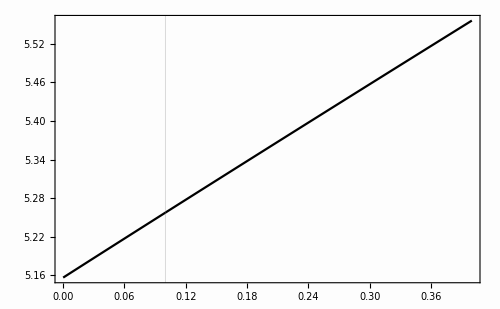

```mathematica
SetDirectory[NotebookDirectory[]];

rp[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψS->GoldenAngle/.{M->1,ϵ->ϵValue}/.δ->DELTA;

Show[

Plot[%,{DELTA,0,δmax},PlotStyle->Black,PlotRange->All],

ImageSize->500,
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["r_p","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["periastron(delta) plot.png",%];
```

Complete plot of r[δ] (nonlinear solution and leading order solution)

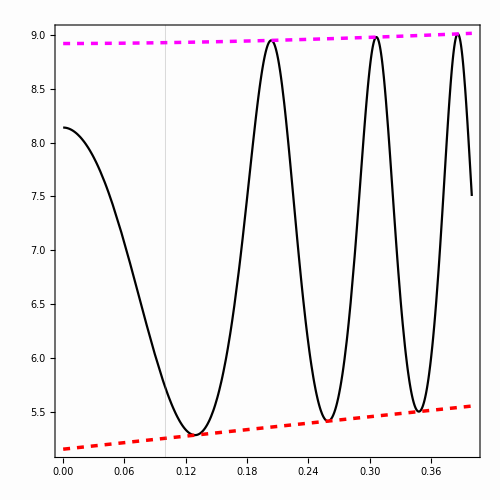

```mathematica
SetDirectory[NotebookDirectory[]];


{radiusSimpler[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψS->GoldenAngle/.{M->1,ϵ->ϵValue}/.δ->DELTA,

ra[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψS->GoldenAngle/.{M->1,ϵ->ϵValue}/.δ->DELTA,

rp[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.{e->es}/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.ψS->GoldenAngle/.{M->1,ϵ->ϵValue}/.δ->DELTA};

Show[
Plot[%,{DELTA,0,δmax},PlotStyle->{Black,{Directive[AbsoluteThickness[2.5],Dashed],Magenta},{Directive[AbsoluteThickness[2.5],Dashed],Red}},
PlotLegends->Placed[LineLegend[{MaTeX["r"],MaTeX["r_a"],MaTeX["r_p"]}],{0.25,0.75}]],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\delta","FontSize"->18],MaTeX["r","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["Nonlinear evolution of r.png",%];
```

## Construction of En[δ] (up to subleading order in δ)

We can express the expression of the energy as a function of δ up to the order δ^2

```mathematica
EnSol[δ_]=KerrGeoEnergy[0,6+2eSolSeries[δ]+δ,eSolSeries[δ],1];
```

```mathematica
Simplify[EnSol[δ],{1>eS>0,δ>0}]
```

(2 √2)/(√(9-eS^2))-((3 eS^3 Log[δ]^3 𝒜[eS]-6 eS^4 Log[δ]^3 𝒜[eS]+eS^5 Log[δ]^3 𝒜[eS]+2 eS^6 Log[δ]^3 𝒜[eS]+9 eS^2 Log[δ]^2 𝒜[eS] ℬ[eS]-18 eS^3 Log[δ]^2 𝒜[eS] ℬ[eS]+3 eS^4 Log[δ]^2 𝒜[eS] ℬ[eS]+6 eS^5 Log[δ]^2 𝒜[eS] ℬ[eS]+9 eS Log[δ] 𝒜[eS] ℬ[eS]^2-18 eS^2 Log[δ] 𝒜[eS] ℬ[eS]^2+3 eS^3 Log[δ] 𝒜[eS] ℬ[eS]^2+6 eS^4 Log[δ] 𝒜[eS] ℬ[eS]^2+3 𝒜[eS] ℬ[eS]^3-6 eS 𝒜[eS] ℬ[eS]^3+eS^2 𝒜[eS] ℬ[eS]^3+2 eS^3 𝒜[eS] ℬ[eS]^3+32 eS^3 ℰe[eS]+32 eS^4 ℰe[eS]+32 eS^3 Log[δ] ℰe[eS]+32 eS^4 Log[δ] ℰe[eS]+64 eS^3 Log[δ]^2 ℰe[eS]+64 eS^4 Log[δ]^2 ℰe[eS]+32 eS^2 ℬ[eS] ℰe[eS]+32 eS^3 ℬ[eS] ℰe[eS]+128 eS^2 Log[δ] ℬ[eS] ℰe[eS]+128 eS^3 Log[δ] ℬ[eS] ℰe[eS]+64 eS ℬ[eS]^2 ℰe[eS]+64 eS^2 ℬ[eS]^2 ℰe[eS]+4 eS^3 ℰδ[eS]-4 eS^5 ℰδ[eS]+4 eS^3 Log[δ] ℰδ[eS]-4 eS^5 Log[δ] ℰδ[eS]+8 eS^3 Log[δ]^2 ℰδ[eS]-8 eS^5 Log[δ]^2 ℰδ[eS]+4 eS^2 ℬ[eS] ℰδ[eS]-4 eS^4 ℬ[eS] ℰδ[eS]+16 eS^2 Log[δ] ℬ[eS] ℰδ[eS]-16 eS^4 Log[δ] ℬ[eS] ℰδ[eS]+8 eS ℬ[eS]^2 ℰδ[eS]-8 eS^3 ℬ[eS]^2 ℰδ[eS]+64 eS^3 Log[δ]^3 ℱe[eS]+64 eS^4 Log[δ]^3 ℱe[eS]-32 eS^2 ℬ[eS] ℱe[eS]-32 eS^3 ℬ[eS] ℱe[eS]-32 eS^2 Log[δ] ℬ[eS] ℱe[eS]-32 eS^3 Log[δ] ℬ[eS] ℱe[eS]+128 eS^2 Log[δ]^2 ℬ[eS] ℱe[eS]+128 eS^3 Log[δ]^2 ℬ[eS] ℱe[eS]-32 eS ℬ[eS]^2 ℱe[eS]-32 eS^2 ℬ[eS]^2 ℱe[eS]+64 eS Log[δ] ℬ[eS]^2 ℱe[eS]+64 eS^2 Log[δ] ℬ[eS]^2 ℱe[eS]+8 eS^3 Log[δ]^3 ℱδ[eS]-8 eS^5 Log[δ]^3 ℱδ[eS]-4 eS^2 ℬ[eS] ℱδ[eS]+4 eS^4 ℬ[eS] ℱδ[eS]-4 eS^2 Log[δ] ℬ[eS] ℱδ[eS]+4 eS^4 Log[δ] ℬ[eS] ℱδ[eS]+16 eS^2 Log[δ]^2 ℬ[eS] ℱδ[eS]-16 eS^4 Log[δ]^2 ℬ[eS] ℱδ[eS]-4 eS ℬ[eS]^2 ℱδ[eS]+4 eS^3 ℬ[eS]^2 ℱδ[eS]+8 eS Log[δ] ℬ[eS]^2 ℱδ[eS]-8 eS^3 Log[δ] ℬ[eS]^2 ℱδ[eS]-32 eS^3 Log[δ]^3 𝒢e[eS]-32 eS^4 Log[δ]^3 𝒢e[eS]+64 eS^3 Log[δ]^4 𝒢e[eS]+64 eS^4 Log[δ]^4 𝒢e[eS]-96 eS^2 Log[δ]^2 ℬ[eS] 𝒢e[eS]-96 eS^3 Log[δ]^2 ℬ[eS] 𝒢e[eS]+128 eS^2 Log[δ]^3 ℬ[eS] 𝒢e[eS]+128 eS^3 Log[δ]^3 ℬ[eS] 𝒢e[eS]+32 eS ℬ[eS]^2 𝒢e[eS]+32 eS^2 ℬ[eS]^2 𝒢e[eS]-64 eS Log[δ] ℬ[eS]^2 𝒢e[eS]-64 eS^2 Log[δ] ℬ[eS]^2 𝒢e[eS]+64 eS Log[δ]^2 ℬ[eS]^2 𝒢e[eS]+64 eS^2 Log[δ]^2 ℬ[eS]^2 𝒢e[eS]-4 eS^3 Log[δ]^3 𝒢δ[eS]+4 eS^5 Log[δ]^3 𝒢δ[eS]+8 eS^3 Log[δ]^4 𝒢δ[eS]-8 eS^5 Log[δ]^4 𝒢δ[eS]-12 eS^2 Log[δ]^2 ℬ[eS] 𝒢δ[eS]+12 eS^4 Log[δ]^2 ℬ[eS] 𝒢δ[eS]+16 eS^2 Log[δ]^3 ℬ[eS] 𝒢δ[eS]-16 eS^4 Log[δ]^3 ℬ[eS] 𝒢δ[eS]+4 eS ℬ[eS]^2 𝒢δ[eS]-4 eS^3 ℬ[eS]^2 𝒢δ[eS]-8 eS Log[δ] ℬ[eS]^2 𝒢δ[eS]+8 eS^3 Log[δ] ℬ[eS]^2 𝒢δ[eS]+8 eS Log[δ]^2 ℬ[eS]^2 𝒢δ[eS]-8 eS^3 Log[δ]^2 ℬ[eS]^2 𝒢δ[eS]) δ^2)/(32 (√2 (-3+eS) (1+eS) (3+eS) √(9-eS^2) 𝒜[eS] (eS Log[δ]+ℬ[eS])^3))+O[δ]^3

```mathematica
Simplify[Series[Normal[Series[EnSol[δ]/.Log[δ]->LOG,{δ,0,2}]],{LOG,-∞,3}],1>eS>0];
Collect[Normal[%],{δ,LOG}]
```

-(18 √2)/((-3+eS) (1+eS) (3+eS) √(9-eS^2))-(18 √2 eS)/((-3+eS) (1+eS) (3+eS) √(9-eS^2))+(2 √2 eS^2)/((-3+eS) (1+eS) (3+eS) √(9-eS^2))+(2 √2 eS^3)/((-3+eS) (1+eS) (3+eS) √(9-eS^2))+δ^2 (-3/(32 √2 (-3+eS) (1+eS) (3+eS) √(9-eS^2))+(3 eS)/(16 √2 (-3+eS) (1+eS) (3+eS) √(9-eS^2))-eS^2/(32 √2 (-3+eS) (1+eS) (3+eS) √(9-eS^2))-eS^3/(16 √2 (-3+eS) (1+eS) (3+eS) √(9-eS^2))+(LOG (-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS]))/(4 √2 (-3+eS) (3+eS) √(9-eS^2) 𝒜[eS])+(-16 eS ℱe[eS]+2 (-1+eS) eS ℱδ[eS]-(eS+2 ℬ[eS]) (-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS]))/(8 √2 (-3+eS) eS (3+eS) √(9-eS^2) 𝒜[eS])+(-8 eS^2 ℰe[eS]+(-1+eS) eS^2 ℰδ[eS]+ℬ[eS] (8 eS ℱe[eS]-(-1+eS) eS ℱδ[eS]-ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS])))/(4 √2 (-3+eS) eS^2 (3+eS) √(9-eS^2) LOG 𝒜[eS])+((eS-2 ℬ[eS]) (-8 eS^2 ℰe[eS]+(-1+eS) eS^2 ℰδ[eS]+ℬ[eS] (8 eS ℱe[eS]-(-1+eS) eS ℱδ[eS]-ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))))/(8 √2 (-3+eS) eS^3 (3+eS) √(9-eS^2) LOG^2 𝒜[eS])+((eS^2-2 eS ℬ[eS]+2 ℬ[eS]^2) (-8 eS^2 ℰe[eS]+(-1+eS) eS^2 ℰδ[eS]+ℬ[eS] (8 eS ℱe[eS]-(-1+eS) eS ℱδ[eS]-ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))))/(8 √2 (-3+eS) eS^4 (3+eS) √(9-eS^2) LOG^3 𝒜[eS]))

```mathematica
Simplify[(-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS])/(4 √2 (-3+eS) (3+eS) √(9-eS^2) 𝒜[eS]),1>eS>0]
```

(-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS])/(4 √2 (-3+eS) (3+eS) √(9-eS^2) 𝒜[eS])

```mathematica
EnSolFull[δ_]:=KerrGeoEnergy[0,6+2eSol[δ]+δ,eSol[δ],1];
```

## Construction of En[τ]

```mathematica
Enτ=Simplify[Simplify[Normal[EnSol[δ]]/.δ->δSolτ[τ]]/.Log[ⅇ^(1/2 (1+ProductLog[-1,(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]-(2 ℬ[eS])/eS))]->1/2 (1+ProductLog[-1,(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]-(2 ℬ[eS])/eS)/.ⅇ^(1+ProductLog[-1,(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]-(2 ℬ[eS])/eS)->(E z Exp[-(2 ℬ[eS])/eS])/ProductLog[-1,z]/.z->(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))/.ProductLog[-1,(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]->W[-1,YYY]/.τ->τS-(ⅇ^(1-(2 ℬ[eS])/eS) eS (3+eS) YYY)/(√2 √(9-eS^2) (-2-eS+eS Cos[ψrS]) 𝒜[eS])];
```

```mathematica
replacementYYY=YYY->(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS));
replacementW=W[-1,YYY]->L1-Log[-L1]+Log[-L1]/L1+((-2+Log[-L1]) Log[-L1])/(2 L1^2)+(Log[-L1] (6-9 Log[-L1]+2 Log[-L1]^2))/(6 L1^3);
```

```mathematica
(*L1 stands for Log[-YYY], which is a factor that goes to -∞*)
```

```mathematica
ExpansionEn1=Simplify[Series[Enτ/.replacementW,{L1,-∞,1}],1>eS>0];
ExpansionEn2=Simplify[Simplify[Normal[Simplify[ExpansionEn1/.replacementYYY,{1>eS>0,YYY<0}]]/.L1->Log[-YYY]/.replacementYYY/.τ->τS+Δτ]]/.Log[(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) Δτ (-2-eS+eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]->Log[-Δτ]+(-1+(2 ℬ[eS])/eS)+Log[-(√2  √(9-eS^2) (-2-eS+eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]/.Log[-Δτ]->LOG;
```

Final result of the expansion

```mathematica
EnergyExpanded[τ_]=Collect[Simplify[Normal[Series[ExpansionEn2,{LOG,-∞,1}]],1>eS>0],{Δτ,LOG}]/.LOG->Log[-Δτ]
```

(2 √2)/(√(9-eS^2))+Δτ (-((-2-eS+eS Cos[ψrS]) (-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS]))/(8 (-3+eS) eS (3+eS)^2)+((-2-eS+eS Cos[ψrS]) (eS (3-6 eS+eS^2+2 eS^3) 𝒜[eS]-8 (1+eS) (-8 eS ℱe[eS]+(-1+eS) eS ℱδ[eS]+2 ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))))/(32 (-3+eS) eS^2 (1+eS) (3+eS)^2 Log[-Δτ]))

```mathematica
(*Note that((-2-eS+eS Cos[ψS]) (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))/(8 (-3+eS) eS (3+eS)^2) only depends on the self-force and it corresponds to the self-force on the unstable circle of radius ((6+2eS)/(1+eS))M  *)
```

Conclusion : En[τ] = En[δ[τ]] = EnS + γ (τ-τS) + ω (τ-τS)/Log[-(τ-τS)].

Circular limit

```mathematica
Simplify[((-2-eS+eS Cos[ψS]) (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))/(8 (-3+eS) eS (3+eS)^2)/.𝒢e[eS]->Ge/.𝒢δ[eS]->Gδ/.e->eS,{1>eS>0}]/.eS->0/.Fϕ1[-2][0,0]->0/.Fϕ1[2][0,0]->0/.Fϕ1[-1][0,0]->0/.Fϕ1[1][0,0]->0
```

√(3/2) M^2 Fϕ1[0][0,0]

```mathematica
(*We check that ((-2-eS+eS Cos[ψS]) (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))/(8 (-3+eS) eS (3+eS)^2) has a nice limit for eS -> 0 and reproduces the result of the circular case, known in the litteratue.*)
```

## Construction of J[δ] (up to subleading order in δ)

We can express the expression of the angular momentum as a function of δ up to the order δ^2

```mathematica
JSol[δ_]=KerrGeoAngularMomentum[0,6+2eSolSeries[δ]+δ,eSolSeries[δ],1];
```

```mathematica
Simplify[JSol[δ],{1>eS>0,δ>0}]
```

(2 (3+eS))/(√(3+2 eS-eS^2))+1/(16 (3+2 eS-eS^2)^(3/2) 𝒜[eS] (eS Log[δ]+ℬ[eS])^3)(3 eS^3 Log[δ]^3 𝒜[eS]+eS^5 Log[δ]^3 𝒜[eS]+9 eS^2 Log[δ]^2 𝒜[eS] ℬ[eS]+3 eS^4 Log[δ]^2 𝒜[eS] ℬ[eS]+9 eS Log[δ] 𝒜[eS] ℬ[eS]^2+3 eS^3 Log[δ] 𝒜[eS] ℬ[eS]^2+3 𝒜[eS] ℬ[eS]^3+eS^2 𝒜[eS] ℬ[eS]^3+32 eS^3 ℰe[eS]+32 eS^3 Log[δ] ℰe[eS]+64 eS^3 Log[δ]^2 ℰe[eS]+32 eS^2 ℬ[eS] ℰe[eS]+128 eS^2 Log[δ] ℬ[eS] ℰe[eS]+64 eS ℬ[eS]^2 ℰe[eS]+4 eS^3 ℰδ[eS]-4 eS^4 ℰδ[eS]+4 eS^3 Log[δ] ℰδ[eS]-4 eS^4 Log[δ] ℰδ[eS]+8 eS^3 Log[δ]^2 ℰδ[eS]-8 eS^4 Log[δ]^2 ℰδ[eS]+4 eS^2 ℬ[eS] ℰδ[eS]-4 eS^3 ℬ[eS] ℰδ[eS]+16 eS^2 Log[δ] ℬ[eS] ℰδ[eS]-16 eS^3 Log[δ] ℬ[eS] ℰδ[eS]+8 eS ℬ[eS]^2 ℰδ[eS]-8 eS^2 ℬ[eS]^2 ℰδ[eS]+64 eS^3 Log[δ]^3 ℱe[eS]-32 eS^2 ℬ[eS] ℱe[eS]-32 eS^2 Log[δ] ℬ[eS] ℱe[eS]+128 eS^2 Log[δ]^2 ℬ[eS] ℱe[eS]-32 eS ℬ[eS]^2 ℱe[eS]+64 eS Log[δ] ℬ[eS]^2 ℱe[eS]+8 eS^3 Log[δ]^3 ℱδ[eS]-8 eS^4 Log[δ]^3 ℱδ[eS]-4 eS^2 ℬ[eS] ℱδ[eS]+4 eS^3 ℬ[eS] ℱδ[eS]-4 eS^2 Log[δ] ℬ[eS] ℱδ[eS]+4 eS^3 Log[δ] ℬ[eS] ℱδ[eS]+16 eS^2 Log[δ]^2 ℬ[eS] ℱδ[eS]-16 eS^3 Log[δ]^2 ℬ[eS] ℱδ[eS]-4 eS ℬ[eS]^2 ℱδ[eS]+4 eS^2 ℬ[eS]^2 ℱδ[eS]+8 eS Log[δ] ℬ[eS]^2 ℱδ[eS]-8 eS^2 Log[δ] ℬ[eS]^2 ℱδ[eS]-32 eS^3 Log[δ]^3 𝒢e[eS]+64 eS^3 Log[δ]^4 𝒢e[eS]-96 eS^2 Log[δ]^2 ℬ[eS] 𝒢e[eS]+128 eS^2 Log[δ]^3 ℬ[eS] 𝒢e[eS]+32 eS ℬ[eS]^2 𝒢e[eS]-64 eS Log[δ] ℬ[eS]^2 𝒢e[eS]+64 eS Log[δ]^2 ℬ[eS]^2 𝒢e[eS]-4 eS^3 Log[δ]^3 𝒢δ[eS]+4 eS^4 Log[δ]^3 𝒢δ[eS]+8 eS^3 Log[δ]^4 𝒢δ[eS]-8 eS^4 Log[δ]^4 𝒢δ[eS]-12 eS^2 Log[δ]^2 ℬ[eS] 𝒢δ[eS]+12 eS^3 Log[δ]^2 ℬ[eS] 𝒢δ[eS]+16 eS^2 Log[δ]^3 ℬ[eS] 𝒢δ[eS]-16 eS^3 Log[δ]^3 ℬ[eS] 𝒢δ[eS]+4 eS ℬ[eS]^2 𝒢δ[eS]-4 eS^2 ℬ[eS]^2 𝒢δ[eS]-8 eS Log[δ] ℬ[eS]^2 𝒢δ[eS]+8 eS^2 Log[δ] ℬ[eS]^2 𝒢δ[eS]+8 eS Log[δ]^2 ℬ[eS]^2 𝒢δ[eS]-8 eS^2 Log[δ]^2 ℬ[eS]^2 𝒢δ[eS]) δ^2+O[δ]^3

```mathematica
Simplify[Series[Normal[Series[JSol[δ]/.Log[δ]->LOG,{δ,0,2}]],{LOG,-∞,3}],1>eS>0];
Collect[Normal[%],{δ,LOG}]
```

18/((3+2 eS-eS^2)^(3/2))+(18 eS)/((3+2 eS-eS^2)^(3/2))-(2 eS^2)/((3+2 eS-eS^2)^(3/2))-(2 eS^3)/((3+2 eS-eS^2)^(3/2))+δ^2 (3/(16 (3+2 eS-eS^2)^(3/2))+eS^2/(16 (3+2 eS-eS^2)^(3/2))+(LOG (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))/(2 (3+2 eS-eS^2)^(3/2) 𝒜[eS])-(-16 eS ℱe[eS]+2 (-1+eS) eS ℱδ[eS]-(eS+2 ℬ[eS]) (-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS]))/(4 eS (3+2 eS-eS^2)^(3/2) 𝒜[eS])-(-8 eS^2 ℰe[eS]+(-1+eS) eS^2 ℰδ[eS]+ℬ[eS] (8 eS ℱe[eS]-(-1+eS) eS ℱδ[eS]-ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS])))/(2 eS^2 (3+2 eS-eS^2)^(3/2) LOG 𝒜[eS])-((eS-2 ℬ[eS]) (-8 eS^2 ℰe[eS]+(-1+eS) eS^2 ℰδ[eS]+ℬ[eS] (8 eS ℱe[eS]-(-1+eS) eS ℱδ[eS]-ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))))/(4 eS^3 (3+2 eS-eS^2)^(3/2) LOG^2 𝒜[eS])-((eS^2-2 eS ℬ[eS]+2 ℬ[eS]^2) (-8 eS^2 ℰe[eS]+(-1+eS) eS^2 ℰδ[eS]+ℬ[eS] (8 eS ℱe[eS]-(-1+eS) eS ℱδ[eS]-ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))))/(4 eS^4 (3+2 eS-eS^2)^(3/2) LOG^3 𝒜[eS]))

```mathematica
Simplify[(8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS])/(2 (3+2 eS-eS^2)^(3/2) 𝒜[eS]),1>eS>0]
```

(8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS])/(2 (3+2 eS-eS^2)^(3/2) 𝒜[eS])

```mathematica
Simplify[(8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS])/(2 (3+2 eS-eS^2)^(3/2) 𝒜[eS])/((-8 𝒢e[eS]+(-1+eS) 𝒢δ[eS])/(4 √2 (-3+eS) (3+eS) √(9-eS^2) 𝒜[eS])),{1>eS>0}]
```

2 √2 ((3+eS)/(1+eS))^(3/2)

```mathematica
JSolFull[δ_]:=KerrGeoAngularMomentum[0,6+2eSol[δ]+δ,eSol[δ],1];
```

## Construction of J[τ]

```mathematica
Jτ=Simplify[Simplify[Normal[JSol[δ]]/.δ->δSolτ[τ]]/.Log[ⅇ^(1/2 (1+ProductLog[-1,(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]-(2 ℬ[eS])/eS))]->1/2 (1+ProductLog[-1,(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]-(2 ℬ[eS])/eS)/.ⅇ^(1+ProductLog[-1,(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]-(2 ℬ[eS])/eS)->(E z Exp[-(2 ℬ[eS])/eS])/ProductLog[-1,z]/.z->(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))/.ProductLog[-1,(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]->W[-1,YYY]/.τ->τS-(ⅇ^(1-(2 ℬ[eS])/eS) eS (3+eS) YYY)/(√2 √(9-eS^2) (-2-eS+eS Cos[ψrS]) 𝒜[eS])];
```

```mathematica
replacementYYY=YYY->(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) (τ-τS) (2+eS-eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS));
replacementW=W[-1,YYY]->L1-Log[-L1]+Log[-L1]/L1+((-2+Log[-L1]) Log[-L1])/(2 L1^2)+(Log[-L1] (6-9 Log[-L1]+2 Log[-L1]^2))/(6 L1^3);
```

```mathematica
(*L1 stands for Log[-YYY], which is a factor that goes to -∞*)
```

```mathematica
ExpansionJ1=Simplify[Series[Jτ/.replacementW,{L1,-∞,1}],1>eS>0];
ExpansionJ2=Simplify[Simplify[Normal[Simplify[ExpansionJ1/.replacementYYY,{1>eS>0,YYY<0}]]/.L1->Log[-YYY]/.replacementYYY/.τ->τS+Δτ]]/.Log[(√2 ⅇ^(-1+(2 ℬ[eS])/eS) √(9-eS^2) Δτ (-2-eS+eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]->Log[-Δτ]+(-1+(2 ℬ[eS])/eS)+Log[-(√2  √(9-eS^2) (-2-eS+eS Cos[ψrS]) 𝒜[eS])/(eS (3+eS))]/.Log[-Δτ]->LOG;
```

Final result of the expansion

```mathematica
MomentumExpanded[τ_]=Collect[Simplify[Normal[Series[ExpansionJ2,{LOG,-∞,1}]],1>eS>0],{Δτ,LOG}]/.LOG->Log[-Δτ]
```

-(2 (-9-9 eS+eS^2+eS^3))/((3+2 eS-eS^2)^(3/2))+Δτ ((√(9-eS^2) (2+eS-eS Cos[ψrS]) (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))/(2 √2 eS (3+eS) (3+2 eS-eS^2)^(3/2))+(√(9-eS^2) (2+eS-eS Cos[ψrS]) (eS (3+eS^2) 𝒜[eS]-8 (-8 eS ℱe[eS]+(-1+eS) eS ℱδ[eS]+2 ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))))/(8 √2 eS^2 (3+eS) (3+2 eS-eS^2)^(3/2) Log[-Δτ]))

Conclusion : J[τ] = J[δ[τ]] = JS + γ (τ-τS) + ω (τ-τS)/Log[-(τ-τS)].

```mathematica
Simplify[(√(9-eS^2) (2+eS-eS Cos[ψrS]) (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))/(2 √2 eS (3+eS) (3+2 eS-eS^2)^(3/2))/.𝒢e[eS]->Ge/.𝒢δ[eS]->Gδ/.e->eS,{1>eS>0}]/.eS->0/.Fϕ1[-2][0,0]->0/.Fϕ1[2][0,0]->0/.Fϕ1[-1][0,0]->0/.Fϕ1[1][0,0]->0
```

18 M^2 Fϕ1[0][0,0]

```mathematica
(*We check that (√(9-eS^2) (2+eS-eS Cos[ψrS]) (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))/(2 √2 eS (3+eS) (3+2 eS-eS^2)^(3/2)) has a nice limit for eS -> 0 and reproduces the result of the circular case, known in the litteratue.*)
```

## Construction of dE/dJ

Now, we compute the ratio dE/dJ. With this, we can show that dE/dt = ΩϕS dJ/dt+ O(1/Log[δ])
Actually, dEdJ is a fraction of polynomials of Log[δ] up the 5th degrees.

```mathematica
dEdJSeries=Collect[Normal[Simplify[(EnSol'[δ]/.Log[δ]->LOG)/(JSol'[δ]/.Log[δ]->LOG),{1>eS>0,δ>0}]],{δ,LOG}]
```

(√(1+eS) ((3-6 eS+eS^2+2 eS^3) 𝒜[eS] (eS LOG+ℬ[eS])^4-2 eS (1+eS) (-8 (eS^3 (-3+4 LOG^3)+12 eS^2 LOG^2 ℬ[eS]+12 eS LOG ℬ[eS]^2+4 ℬ[eS]^3) ℰe[eS]+(-1+eS) (eS^3 (-3+4 LOG^3)+12 eS^2 LOG^2 ℬ[eS]+12 eS LOG ℬ[eS]^2+4 ℬ[eS]^3) ℰδ[eS]-32 eS^3 LOG^4 ℱe[eS]-24 eS^2 ℬ[eS] ℱe[eS]-96 eS^2 LOG^3 ℬ[eS] ℱe[eS]-96 eS LOG^2 ℬ[eS]^2 ℱe[eS]-32 LOG ℬ[eS]^3 ℱe[eS]-4 eS^3 LOG^4 ℱδ[eS]+4 eS^4 LOG^4 ℱδ[eS]-3 eS^2 ℬ[eS] ℱδ[eS]+3 eS^3 ℬ[eS] ℱδ[eS]-12 eS^2 LOG^3 ℬ[eS] ℱδ[eS]+12 eS^3 LOG^3 ℬ[eS] ℱδ[eS]-12 eS LOG^2 ℬ[eS]^2 ℱδ[eS]+12 eS^2 LOG^2 ℬ[eS]^2 ℱδ[eS]-4 LOG ℬ[eS]^3 ℱδ[eS]+4 eS LOG ℬ[eS]^3 ℱδ[eS]-32 eS^3 LOG^5 𝒢e[eS]-96 eS^2 LOG^4 ℬ[eS] 𝒢e[eS]+24 eS ℬ[eS]^2 𝒢e[eS]-96 eS LOG^3 ℬ[eS]^2 𝒢e[eS]-32 LOG^2 ℬ[eS]^3 𝒢e[eS]-4 eS^3 LOG^5 𝒢δ[eS]+4 eS^4 LOG^5 𝒢δ[eS]-12 eS^2 LOG^4 ℬ[eS] 𝒢δ[eS]+12 eS^3 LOG^4 ℬ[eS] 𝒢δ[eS]+3 eS ℬ[eS]^2 𝒢δ[eS]-3 eS^2 ℬ[eS]^2 𝒢δ[eS]-12 eS LOG^3 ℬ[eS]^2 𝒢δ[eS]+12 eS^2 LOG^3 ℬ[eS]^2 𝒢δ[eS]-4 LOG^2 ℬ[eS]^3 𝒢δ[eS]+4 eS LOG^2 ℬ[eS]^3 𝒢δ[eS])))/(2 √2 (3+eS)^(3/2) ((3+eS^2) 𝒜[eS] (eS LOG+ℬ[eS])^4+2 eS (8 (eS^3 (-3+4 LOG^3)+12 eS^2 LOG^2 ℬ[eS]+12 eS LOG ℬ[eS]^2+4 ℬ[eS]^3) ℰe[eS]-(-1+eS) (eS^3 (-3+4 LOG^3)+12 eS^2 LOG^2 ℬ[eS]+12 eS LOG ℬ[eS]^2+4 ℬ[eS]^3) ℰδ[eS]+32 eS^3 LOG^4 ℱe[eS]+24 eS^2 ℬ[eS] ℱe[eS]+96 eS^2 LOG^3 ℬ[eS] ℱe[eS]+96 eS LOG^2 ℬ[eS]^2 ℱe[eS]+32 LOG ℬ[eS]^3 ℱe[eS]+4 eS^3 LOG^4 ℱδ[eS]-4 eS^4 LOG^4 ℱδ[eS]+3 eS^2 ℬ[eS] ℱδ[eS]-3 eS^3 ℬ[eS] ℱδ[eS]+12 eS^2 LOG^3 ℬ[eS] ℱδ[eS]-12 eS^3 LOG^3 ℬ[eS] ℱδ[eS]+12 eS LOG^2 ℬ[eS]^2 ℱδ[eS]-12 eS^2 LOG^2 ℬ[eS]^2 ℱδ[eS]+4 LOG ℬ[eS]^3 ℱδ[eS]-4 eS LOG ℬ[eS]^3 ℱδ[eS]+32 eS^3 LOG^5 𝒢e[eS]+96 eS^2 LOG^4 ℬ[eS] 𝒢e[eS]-24 eS ℬ[eS]^2 𝒢e[eS]+96 eS LOG^3 ℬ[eS]^2 𝒢e[eS]+32 LOG^2 ℬ[eS]^3 𝒢e[eS]+4 eS^3 LOG^5 𝒢δ[eS]-4 eS^4 LOG^5 𝒢δ[eS]+12 eS^2 LOG^4 ℬ[eS] 𝒢δ[eS]-12 eS^3 LOG^4 ℬ[eS] 𝒢δ[eS]-3 eS ℬ[eS]^2 𝒢δ[eS]+3 eS^2 ℬ[eS]^2 𝒢δ[eS]+12 eS LOG^3 ℬ[eS]^2 𝒢δ[eS]-12 eS^2 LOG^3 ℬ[eS]^2 𝒢δ[eS]+4 LOG^2 ℬ[eS]^3 𝒢δ[eS]-4 eS LOG^2 ℬ[eS]^3 𝒢δ[eS])))

```mathematica
Simplify[Series[dEdJSeries,{LOG,-∞,2}],{1>eS>0}]
```

((1+eS)/(3+eS))^(3/2)/(2 √2)+((-3+eS) eS √((1+eS)/(3+eS)) 𝒜[eS])/(16 √2 (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]) LOG)-((-3+eS) √((1+eS)/(3+eS)) 𝒜[eS] (eS (3+eS^2) 𝒜[eS]-8 (-8 eS ℱe[eS]+(-1+eS) eS ℱδ[eS]+ℬ[eS] (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS]))))/(128 (√2 (8 𝒢e[eS]+𝒢δ[eS]-eS 𝒢δ[eS])^2) LOG^2)+O[1/LOG]^3

## 8) Plots of the motion in phase space

## Trajectory in the plane (e,p)

```mathematica
pSol[δ_]=6+2 eSol[δ]+δ;
```

```mathematica
eSolprime[δ_]=(𝒜[eS]/(δ(ℬ[eS]+ eS Log[δ]))+(ℰδ[eS] +ℱδ[eS] Log[δ]+𝒢δ[eS] Log[δ]^2)/(ℬ[eS]+ eS Log[δ])^2)dedδ//Normal//Simplify; (*This is de/dt*)
pSolprime[δ_]=(𝒜[eS]/(δ(ℬ[eS]+ eS Log[δ]))+(ℰδ[eS] +ℱδ[eS] Log[δ]+𝒢δ[eS] Log[δ]^2)/(ℬ[eS]+ eS Log[δ])^2)+ 2 eSolprime[δ]//Normal;(*This is (dp/dt)*)
```

```mathematica
Simplify[eccprime[δ]/psolprime[δ],1>eS>0]//Simplify ;(*Just a simple remarque: reformulation of the critical function*)
Series[%,{δ,0,0}]
```

eccprime[0]/psolprime[0]+O[δ]^1

```mathematica
vector[δ_]=Simplify[{pSolprime[δ],eSolprime[δ]},1>eS>0];
```

```mathematica
Arrowδ[δ_]:=Graphics[
{Arrowheads[SizeArrowHead],
Arrow[
{{pSol[δ],eSol[δ]},{pSol[δ]+factor vector[δ][[1]],eSol[δ]+factor vector[δ][[2]]} }/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.eS->es]}
];
```

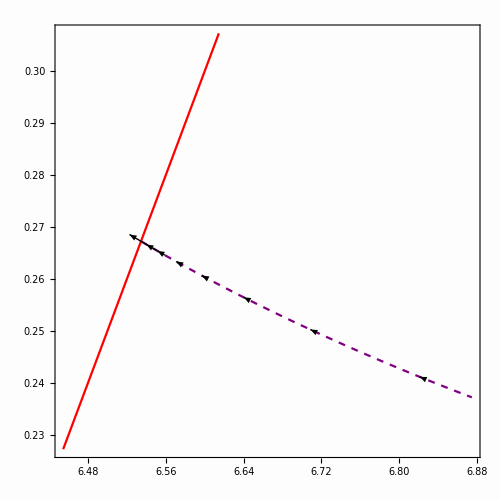

```mathematica
SetDirectory[NotebookDirectory[]];

SizeArrowHead=0.018;
factor=0.00055;

{pSol[δ],eSol[δ]}/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.eS->es/.δ->DELTA;

res=Show[
ParametricPlot[%,{DELTA,0,δmax},AspectRatio->1,PlotStyle->{Purple,Dashed}],

ParametricPlot[{6+2ES,ES},{ES,es-0.04,es+0.04},AspectRatio->1,AxesLabel->{"p","e"},PlotStyle->Red],

Arrowδ[0.01],
Arrowδ[0.02],
Arrowδ[0.03],
Arrowδ[0.05],
Arrowδ[0.08],
Arrowδ[0.13],
Arrowδ[0.21],
Arrowδ[0.34],

ImageSize->500,
PlotRange->All,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["p","FontSize"->18],MaTeX["e","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["Plot p-e.png",%];
```

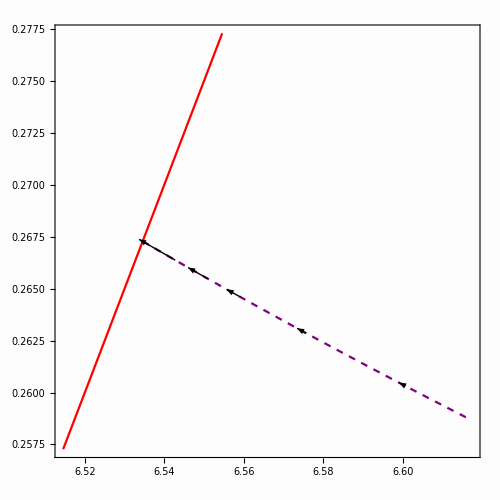

```mathematica
SetDirectory[NotebookDirectory[]];
SizeArrowHead=0.025;
factor=0.00025;

{pSol[δ],eSol[δ]}/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.eS->es/.δ->DELTA;

res=Show[
ParametricPlot[%,{DELTA,0,0.1},AspectRatio->1,PlotStyle->{Purple,Dashed}],

ParametricPlot[{6+2ES,ES},{ES,es-0.01,es+0.01},AspectRatio->1,AxesLabel->{"p","e"},PlotStyle->Red],



Arrowδ[0.01],
Arrowδ[0.02],
Arrowδ[0.03],
Arrowδ[0.05],
Arrowδ[0.08],

ImageSize->500,
PlotRange->All,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["p","FontSize"->18],MaTeX["e","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}]
Export["Plot p-e closer.png",%];
```

```mathematica
(*Table[Fibonacci[n],{n,20}]
{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}*)
```

## Trajectory in the plane (En,J)

```mathematica
eccNum[δ_]:=eSol[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.eS->es//Re;
```

```mathematica
Energy[δ_]=EnSolFull[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.eS->es//Re;
Momentum[δ_]=JSolFull[δ]/.replacement1/.eS->es/.{Λ->L,Τ->T,Λ2->L2,Τ2->T2,Κ->KNum}/.M->1/.{Fr1[0]->Fr[0],Fr1[1]->Fr[1],Fr1[-1]->Fr[-1],Fϕ1[0]->Fϕ[0],Fϕ1[1]->Fϕ[1],Fϕ1[-1]->Fϕ[-1],Fr1[2]->Fr[2],Fr1[-2]->Fr[-2],Fϕ1[2]->Fϕ[2],Fϕ1[-2]->Fϕ[-2]}/.Κ->KNum/.eS->es//Re;
```

```mathematica
EnSep[e_]:=KerrGeoEnergy[0,6+2e,e,1];
LSep[e_]:=KerrGeoAngularMomentum[0,6+2e,e,1];
```

```mathematica
e00=Block[{δ=0.001`30,e=eccNum[0.001`30]},TeukolskyPointParticleMode[-2,2,2,0,0,KerrGeoOrbit[0,6+2e+δ,e,1]]["Fluxes"]];
e02=Block[{δ=0.2`30,e=eccNum[0.2`30]},TeukolskyPointParticleMode[-2,2,2,0,0,KerrGeoOrbit[0,6+2e+δ,e,1]]["Fluxes"]];
e03=Block[{δ=0.3`30,e=eccNum[0.3`30]},TeukolskyPointParticleMode[-2,2,2,0,0,KerrGeoOrbit[0,6+2e+δ,e,1]]["Fluxes"]];
e05=Block[{δ=0.5`30,e=eccNum[0.5`30]},TeukolskyPointParticleMode[-2,2,2,0,0,KerrGeoOrbit[0,6+2e+δ,e,1]]["Fluxes"]];
e08=Block[{δ=0.8`30,e=eccNum[0.8`30]},TeukolskyPointParticleMode[-2,2,2,0,0,KerrGeoOrbit[0,6+2e+δ,e,1]]["Fluxes"]];
e13=Block[{δ=1.3`30,e=eccNum[1.3`30]},TeukolskyPointParticleMode[-2,2,2,0,0,KerrGeoOrbit[0,6+2e+δ,e,1]]["Fluxes"]];
e21=Block[{δ=2.1`30,e=eccNum[2.1`30]},TeukolskyPointParticleMode[-2,2,2,0,0,KerrGeoOrbit[0,6+2e+δ,e,1]]["Fluxes"]];
e34=Block[{δ=3.4`30,e=eccNum[3.4`30]},TeukolskyPointParticleMode[-2,2,2,0,0,KerrGeoOrbit[0,6+2e+δ,e,1]]["Fluxes"]];
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in Teukolsky`ConvolveSource`Private`qr in the region {{0.,3.14159}}. NIntegrate obtained -584.048+225.642 ⅈ and 0.896713 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in Teukolsky`ConvolveSource`Private`qr in the region {{0.,3.14159}}. NIntegrate obtained -602.344-258.815 ⅈ and 0.190649 for the integral and error estimates.

```mathematica
vector[0.001]={e00[["Energy"]][["ℐ"]]+e00[["Energy"]][["ℋ"]],e00[["AngularMomentum"]][["ℐ"]]+e00[["AngularMomentum"]][["ℋ"]]};
vector[0.2]={e02[["Energy"]][["ℐ"]]+e02[["Energy"]][["ℋ"]],e02[["AngularMomentum"]][["ℐ"]]+e02[["AngularMomentum"]][["ℋ"]]};
vector[0.3]={e03[["Energy"]][["ℐ"]]+e03[["Energy"]][["ℋ"]],e03[["AngularMomentum"]][["ℐ"]]+e03[["AngularMomentum"]][["ℋ"]]};
vector[0.5]={e05[["Energy"]][["ℐ"]]+e05[["Energy"]][["ℋ"]],e05[["AngularMomentum"]][["ℐ"]]+e05[["AngularMomentum"]][["ℋ"]]};
vector[0.8]={e08[["Energy"]][["ℐ"]]+e08[["Energy"]][["ℋ"]],e08[["AngularMomentum"]][["ℐ"]]+e08[["AngularMomentum"]][["ℋ"]]};
vector[1.3]={e13[["Energy"]][["ℐ"]]+e13[["Energy"]][["ℋ"]],e13[["AngularMomentum"]][["ℐ"]]+e13[["AngularMomentum"]][["ℋ"]]};
vector[2.1]={e21[["Energy"]][["ℐ"]]+e21[["Energy"]][["ℋ"]],e21[["AngularMomentum"]][["ℐ"]]+e21[["AngularMomentum"]][["ℋ"]]};
vector[3.4]={e34[["Energy"]][["ℐ"]]+e34[["Energy"]][["ℋ"]],e34[["AngularMomentum"]][["ℐ"]]+e34[["AngularMomentum"]][["ℋ"]]};
```

```mathematica
Arrowδ[δ_]:=Graphics[{Arrowheads[0.03],Arrow[{{Momentum[δ],Energy[δ]},{Momentum[δ]-VectorDisplayEnhancementFactor vector[δ][[2]],Energy[δ]-VectorDisplayEnhancementFactor vector[δ][[1]]}}]}];
```

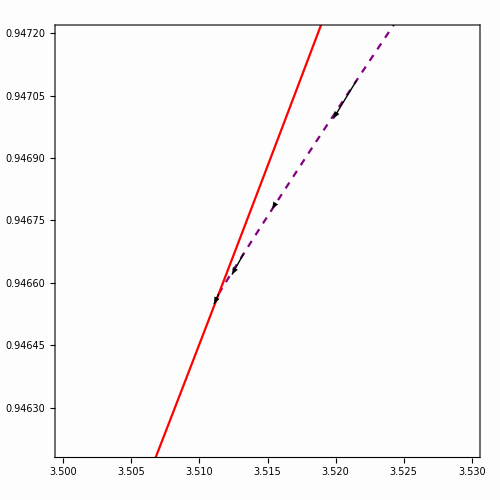

```mathematica
SetDirectory[NotebookDirectory[]];
VectorDisplayEnhancementFactor=12;
plotTeuk2=Show[
ParametricPlot[{Momentum[δ],Energy[δ]},{δ,0,0.8},PlotStyle->{Purple,Dashed},AspectRatio->1],

ParametricPlot[{LSep[ES],EnSep[ES]},{ES,0.15,0.35},AxesLabel->{"L","E"},PlotStyle->Red],

Arrowδ[0.001],
Arrowδ[0.2],
Arrowδ[0.3],
Arrowδ[0.5],
Arrowδ[0.8],
Arrowδ[1.3],

ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["\\text{Angular momentum}","FontSize"->18],MaTeX["\\text{Energy}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None},
PlotRange->{{3.50,3.53},{0.9462,0.9472}}
]
Export["Plot E-L.png",%];
```

## 9) Elements on the W Lambert function (real branches)

Here are elements on the Lambert W function. We check several identities and derive the series expansion close to the separatrix.

We focus on the real branches of the W functions only. That is we focus on the branches k = 0 and k = -1.

```mathematica
$Assumptions=True;
```

```mathematica
W0[z_]:=ProductLog[0,z];
Wm1[z_]:=ProductLog[-1,z];
```

## Behaviour of the W functions

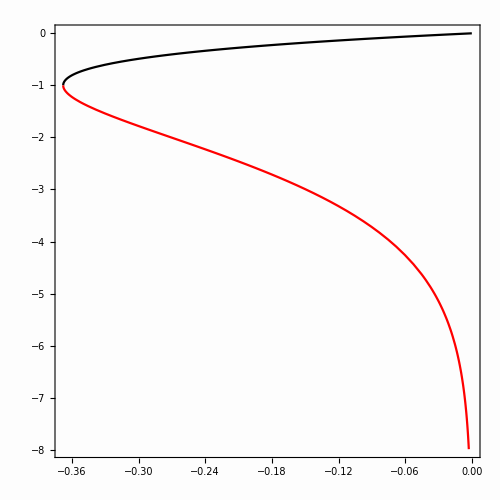

```mathematica
SetDirectory[NotebookDirectory[]];

Show[

Plot[{W0[x],Wm1[x]},{x,-1/E,0},PlotStyle->{Black,Red},PlotLegends->Placed[LineLegend[{MaTeX["W_0"],MaTeX["W_{-1}"]}],{0.8,0.2}],AspectRatio->1],

PlotRange->All,
ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["z","FontSize"->18],MaTeX["W_k","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}
]
Export["Plot W functions.png",%];
```

In black: W0[x]
In red: Wm1[x]; second real branches of the W function.

## Identities

```mathematica
W0[-1/E]
Wm1[-1/E]
```

-1

-1

```mathematica
W0[0]
Wm1[0]
```

0

-∞

```mathematica
W0[E]
Wm1[E]
```

1

ProductLog[-1,ⅇ]

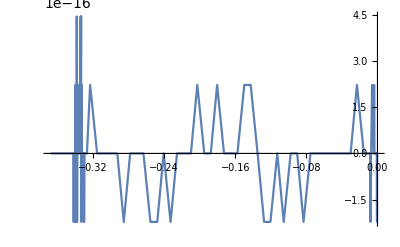

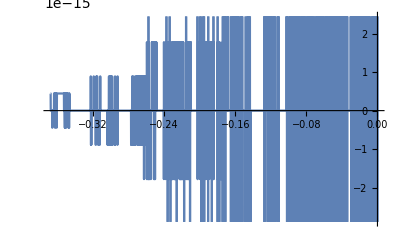

```mathematica
Plot[Exp[-W0[x]]-W0[x]/x,{x,-1/E,0}]
Plot[Exp[-Wm1[x]]-Wm1[x]/x,{x,-1/E,0}]
```

## Series expansion and evaluation of the accuracy of this series expansion

```mathematica
Series[Wm1[x],{x,0,0}]
```

1/(2 (2 π+ⅈ Log[x])^2)(-16 ⅈ π^3+24 π^2 Log[x]+12 ⅈ π Log[x]^2-2 Log[x]^3+2 Log[-ⅈ (2 π+ⅈ Log[x])]+4 ⅈ π Log[-ⅈ (2 π+ⅈ Log[x])]-8 π^2 Log[-ⅈ (2 π+ⅈ Log[x])]-2 Log[x] Log[-ⅈ (2 π+ⅈ Log[x])]-8 ⅈ π Log[x] Log[-ⅈ (2 π+ⅈ Log[x])]+2 Log[x]^2 Log[-ⅈ (2 π+ⅈ Log[x])]-Log[-ⅈ (2 π+ⅈ Log[x])]^2)+O[x]^1

This is the Equation  (4.19)  of  https : // www . uwo . ca/apmaths/faculty/jeffrey/pdfs/W - adv - cm . pdf

```mathematica
SeriesW1[x_]:=L1-L2+L2/L1+L2(-2+L2)/2/L1^2+L2(6-9L2+2L2^2)/6/L1^3+L2(-12+36L2-22L2^2+3L2^3)/12/L1^4/.{L1-> Log[-x],L2-> Log[-Log[-x]]};
SeriesW1LEAD[x_]:=Log[-x]- 0Log[-Log[-x]];
```

```mathematica
{Wm1[-0.01],SeriesW1[-0.01],SeriesW1LEAD[-0.01]}
{Wm1[-0.0001],SeriesW1[-0.0001],SeriesW1LEAD[-0.0001]}
N[{Wm1[-0.0000001`100],SeriesW1[-0.0000001`100],SeriesW1LEAD[-0.0000001`100]}]
N[{Wm1[-1/10^100],SeriesW1[-1/10^100],SeriesW1LEAD[(-1/10^100)]}]
```

{-6.47278,-6.4723,-4.60517}

{-11.6671,-11.6671,-9.21034}

{-19.066,-19.066,-16.1181}

{-235.721,-235.721,-230.259}

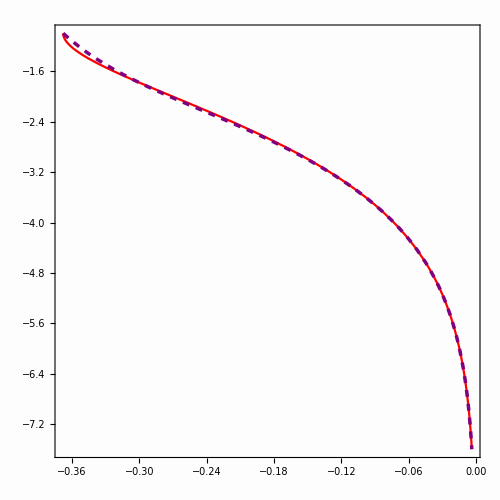

```mathematica
SetDirectory[NotebookDirectory[]];

Show[

Plot[{Wm1[x],SeriesW1[x]},{x,-1/E,0},PlotStyle->{Red,{Directive[AbsoluteThickness[2.5],Dashed],Purple}},PlotLegends->Placed[LineLegend[{MaTeX["W_{-1}"],MaTeX["\\text{Approx of }W_{-1}" ]}],{0.7,0.2}],AspectRatio->1],

PlotRange->All,
ImageSize->500,
AspectRatio->1,
Frame->True,
FrameStyle->Directive[Thickness[0.0015],Black],
FrameTicks->Automatic,Background->Lighter[LightGray,0.95],
FrameLabel->{MaTeX["z","FontSize"->18],MaTeX["W_{-1}","FontSize"->18]},
FrameTicksStyle->Directive[FontSize->12,FontFamily->"Arial"],
GridLines->{{0.1},None}
]
Export["Plot Wm1 vs series.png",%];
```

We see that the convergence of the series towards the exact value is very slow.

```mathematica
TaylorW0[x_,CutOffn_]:=Sum[(-n)^(n-1)/n! x^n,{n,1,CutOffn}]
{W0[-0.01],TaylorW0[-0.01,16]}
```

{-0.0101015,-0.0101015}